# XXZ bulk with ZZ edge coupling

L total spins: edges A=1 and B=L, bulk M={2,...,L-1}. No magnetic fields are added. This notebook is self-contained. Evaluate its initialization cells once; the two static scans, state dynamics and channel dynamics then run independently. All model parameters are editable within their own run. g must be nonzero; Delta may be zero. These .m files use separate named contexts. Evaluate the Begin cell first: it saves the caller search path and restricts symbol lookup to System` while this file context is active. Evaluate the final cell to restore the path. Evaluate all required definition cells before a chosen run; run cells are executable. Get evaluates every run.

```mathematica
Begin["XXZZZ`"]; XXZZZ`savedContextPath=$ContextPath; $ContextPath={"System`"};
```

# 1. Statics: complete sector eigenpairs, entropies and IPR

### 1.1 Definitions shared by all four chapters

Initialization cells contain definitions only. They do not start a scan, diagonalize a model, choose an initial state, plot, or export. Their benchmark conventions are S=sigma/2, hbar=1, bit 0=up, natural-log entropy, edge basis {00,01,10,11}. Both end bonds replace the usual XXZ end bonds.

H = J Sum[j=2,...,L-2](Sjx S(j+1)x + Sjy S(j+1)y + Delta Sjz S(j+1)z) + g (S1z S2z + S(L-1)z SLz). J and g have energy units. In the exchange case the spin-flip matrix element is g/2.

ZZ resolves sA, sB and mBulk first. Reflection R is compatible when sA=sB; RF is compatible when sA=-sB and mBulk=0. Symmetry partners retain separate data and share a static panel. Actual conditional-bulk charges are checked and added when compatible, including the two-site bulk Casimir at Delta=+/-1 with equal conditional fields. Each eigenvector in this basis has zero edges-versus-bulk entropy. At Delta=0 the Hamiltonian is free fermionic (conditional bulk for ZZ); the benchmark spin/spatial classification stays valid, with additional conserved mode occupations and possible degeneracies. It is not a classification of every integrability charge. No degenerate energy vectors are silently mixed or pooled across the listed sectors.

#### Utilities, spin operators and Hamiltonian guards

Stop the current cell if an input or validation fails .

```mathematica
check[test_,message_] := If[!TrueQ[test],Print[Style[message,Red ]];Abort[]];
realQ[x_] := NumericQ[x] && NumberQ[N[x ]] && TrueQ[Im[N[x ]]==0];
id[n_] := SparseArray[Band[{1,1}]->1,{n,n}];
maxAbs[a_] := If[Head[a]===SparseArray,
 Max[0,Sequence@@Abs[a["NonzeroValues"]]],Max[0,Sequence@@Abs[Flatten[a ]]]];
herm[a_] := (a+ConjugateTranspose[a])/2;
ketRho[v_] := Outer[Times,v,Conjugate[v ]];
```

Embed a one-spin or nearest-neighbour operator .

```mathematica
siteOp[a_,k_,l_] := KroneckerProduct[id[2^(k-1)],SparseArray[a],id[2^(l-k)]];
bondOp[a_,b_,k_,l_] := KroneckerProduct[
 id[2^(k-1)],SparseArray[a],SparseArray[b],id[2^(l-k-1)]];
```

Reject Hamiltonians that the real, magnetization-block solver cannot represent .

```mathematica
u1Check[h_,l_Integer,tol_] := Module[{a=SparseArray[h],nd,off,scale,leak},
 check[Dimensions[a]=={2^l,2^l},"Hamiltonian dimensions do not match L."];
 nd=Total /@ IntegerDigits[Range[0,2^l-1],2,l];
 off=Select[Most[ArrayRules[a]],nd[[#[[1,1]]]]!=nd[[#[[1,2]]]]&];
 scale=Max[1.,Norm[a,Infinity]];leak=If[off==={},0.,Max[Abs[Last /@ off]]];
 check[leak<=tol scale,
  "H mixes total-Sz sectors. This solver would drop matrix elements. Use a solver for the surviving symmetries or full ED."];
 <|"MaxOffBlockElement"->leak,"Scale"->scale,"RelativeLeakage"->leak/scale,"Passed"->True|>
];
realSectorCheck[h_,l_Integer,tol_] := Module[{a=SparseArray[h],u,scale},
 u=u1Check[a,l,tol];scale=Max[1.,Norm[a,Infinity]];
 check[maxAbs[a-ConjugateTranspose[a]]<=tol scale,"H must be Hermitian before block diagonalization."];
 check[maxAbs[Im[a]]<=tol scale,
  "The legacy fixSign solver requires a real Hamiltonian. Complex Hermitian models need phase-preserving eigenvectors."];
 u
];
```

#### Partial traces, entropies and two-qubit entanglement

Coefficient matrix for a chosen set of sites; rho=A . A† .

```mathematica
partitionFactor[fac_,sites_List,l_Integer] := Module[{r=Dimensions[fac][[2]],rest},
 rest=Complement[Range[l],sites];
 ArrayReshape[Transpose[ArrayReshape[fac,Join[ConstantArray[2,l],{r}]],
  Ordering[Join[sites,rest,{l+1}]]],{2^Length[sites],2^Length[rest] r}]
];
reducedState[fac_,sites_List,l_Integer] := With[{a=partitionFactor[fac,sites,l]},
 a . ConjugateTranspose[a ]];
reducedKet[v_,sites_List,l_Integer] := reducedState[Transpose[{v}],sites,l];
edgeRho[v_,l_Integer] := reducedKet[v,{1,l},l];
```

Single-edge reductions, in edge basis {00,01,10,11} .

```mathematica
traceB[r_] := {{r[[1,1]]+r[[2,2]],r[[1,3]]+r[[2,4]]},
 {r[[3,1]]+r[[4,2]],r[[3,3]]+r[[4,4]]}};
traceA[r_] := {{r[[1,1]]+r[[3,3]],r[[1,2]]+r[[3,4]]},
 {r[[2,1]]+r[[4,3]],r[[2,2]]+r[[4,4]]}};
```

Von Neumann entropy, natural logarithms .

```mathematica
entropy[r_] := Module[{e=Select[Re[Eigenvalues[N[herm[r ]]]],#>0&]},
 If[e==={},0.,-Total[e Log[e ]]]];

(* Pure-state entropy for sites 1,...,floor(L/2). *)
halfEntropy[v_,l_] := Module[{p},
 p=Select[SingularValueList[ArrayReshape[v,{2^Floor[l/2],2^Ceiling[l/2]}]]^2,#>0&];
 If[p==={},0.,-Total[p Log[p ]]]];

(* Pure-state entanglement of both edges together versus the middle. *)
edgeEntropy[v_,l_] := entropy[edgeRho[v,l ]];
```

Negativity between spin 1 and spin L .

```mathematica
ptB[r_] := ArrayReshape[Transpose[ArrayReshape[r,{2,2,2,2}],{1,4,3,2}],{4,4}];
negativity[r_] := Total[Clip[-Re[Eigenvalues[herm[ptB[r ]]]],{0,Infinity}]];

(* Concurrence from an exact reduced-state factor; stable at rank deficiency. *)
concurrence[a_] := Module[{q,r,f,s},
 {q,r}=QRDecomposition[ConjugateTranspose[a ]]; f=ConjugateTranspose[r];
 s=PadRight[Reverse[Sort[SingularValueList[
  Transpose[f] . KroneckerProduct[PauliMatrix[2],PauliMatrix[2]] . f,Tolerance->0]]],4];
 Max[0.,First[s]-Total[Rest[s ]]]
];
```

#### Pure and mixed state constructors

Tensor product of normalized local spinors .

```mathematica
productKet[locals_List] := Module[{v},
 check[Length[locals]>0 && AllTrue[locals,
  VectorQ[#,NumericQ] && Length[#]==2 && Norm[#]>0&],"Invalid local spinor."];
 v=Fold[Flatten[KroneckerProduct[#1,N[#2/Norm[#2 ]]]]&,{1.},locals]; v/Norm[v]
];

(* first=0 starts with up; first=1 starts with down. *)
neel[n_Integer,first_:0] := productKet[Table[UnitVector[2,1+Mod[k-1+first,2]],{k,n}]];
(* phi is the azimuth of the first spin in this vector. *)
helix[n_Integer,q_,theta_:Pi/2,phi_:0] := productKet[
 Table[{Cos[theta/2],Exp[I(phi+(k-1)q)] Sin[theta/2]},{k,n}]];
```

Accept a vector or a positive, trace-one density matrix .

```mathematica
stateFactor[input_,dim_,tol_] := Module[{x=N[Normal[input ]],e,v,keep},
 If[VectorQ[x,NumericQ],check[Length[x]==dim && Norm[x]>0,"Invalid state vector."];
  Return[Transpose[{x/Norm[x]}]]];
 check[MatrixQ[x,NumericQ] && Dimensions[x]=={dim,dim},"Invalid density-matrix dimensions."];
 check[Norm[x-ConjugateTranspose[x],"Frobenius"]<=tol && Abs[Tr[x]-1]<=tol,
  "Density matrix must be Hermitian with trace one."];
 {e,v}=Eigensystem[herm[x ]];check[Min[Re[e ]]>=-tol,"Density matrix is not positive."];
 e=Clip[Re[e],{0,Infinity}];e/=Total[e];keep=Select[Range[dim],e[[# ]]>0&];
 Transpose[Sqrt[e[[keep ]]] v[[keep ]]]
];
(* Reorder (edge 1,edge L,middle) to physical sites 1,...,L. *)
joinStates[ef_,mf_,l_] := Module[{a=KroneckerProduct[ef,mf]},
 ArrayReshape[Transpose[ArrayReshape[a,{2,2,2^(l-2),Dimensions[a][[2]]}],
  {1,3,2,4}],{2^l,Dimensions[a][[2]]}]
];
```

#### Symmetry operators and validated diagonalization

Charges allowed by the effective longitudinal fields .

```mathematica
charges[p_] := Module[{l=p["L"],d=2^p["L"],r,f,fields,out=<||>,st,sx,sy,sz},
 fields=ConstantArray[p["h"],l];fields[[1]]+=p["bLeft"];fields[[-1]]+=p["bRight"];
 r=SparseArray[Table[{1+FromDigits[Reverse[IntegerDigits[k,2,l ]],2],k+1}->1,
  {k,0,d-1}],{d,d}];
 f=SparseArray[Table[{d-k,k+1}->1,{k,0,d-1}],{d,d}];
 If[And@@MapThread[TrueQ[#1==#2]&,{fields,Reverse[fields]}],AssociateTo[out,"R"->r ]];
 If[And@@(TrueQ[#==0]& /@ fields),AssociateTo[out,"F"->f ]];
 If[And@@MapThread[TrueQ[#1 == -#2]&,{fields,Reverse[fields]}] &&
  !(KeyExistsQ[out,"R"] && KeyExistsQ[out,"F"]),AssociateTo[out,"RF"->r . f]];
 If[(TrueQ[p["Delta"]==1] || TrueQ[p["Delta"] == -1]) && And@@(TrueQ[#==First[fields ]]& /@ fields),
  st=If[TrueQ[p["Delta"]==1],ConstantArray[1,l],Table[(-1)^(k-1),{k,l}]];
  sx=Total[Table[st[[k ]] siteOp[PauliMatrix[1]/2,k,l],{k,l}]];
  sy=Total[Table[st[[k ]] siteOp[PauliMatrix[2]/2,k,l],{k,l}]];
  sz=Total[Table[siteOp[PauliMatrix[3]/2,k,l],{k,l}]];
  AssociateTo[out,If[TrueQ[p["Delta"]==1],"S2","StaggeredS2"]->(sx . sx+sy . sy+sz . sz)]];
 out
];
```

Split a charge eigenspace; no energy eigenvectors are mixed here .

```mathematica
splitCharge[s_,q_,name_,tol_] := Module[{b=s["Basis"],e,v,order,groups,label},
 {e,v}=Eigensystem[N[herm[ConjugateTranspose[b] . q . b]]];
 order=Ordering[Re[e ]];e=Re[e[[order ]]];v=v[[order ]];
 groups=Split[Range[Length[e ]],Abs[e[[#1 ]]-e[[#2 ]]]<tol&];
 Table[label=If[MemberQ[{"S2","StaggeredS2"},name],
   Round[(-1+Sqrt[1+4 Mean[e[[g ]]]])/2,1/2],Round[Mean[e[[g ]]]]];
  <|"Basis"->b . Transpose[Orthogonalize[v[[g ]]]],"Labels"->Append[s["Labels"],
   Switch[name,"S2","S","StaggeredS2","StaggeredS",_,name]->label]|>,{g,groups}]
];
(* The Hamiltonian is real symmetric; retain real packed vectors. *)
fixSign[v_] := Module[{w=Re[N[v ]],k},
 k=First[Ordering[Abs[w],-1]];Developer`ToPackedArray[If[w[[k ]]<0,-w,w ]]
];
```

Raw eigenpairs in one resolved sector; preserve arbitrarily small gaps .

```mathematica
diagonalizeBlock[s_,hm_,ids_,tol_] := Module[{b=s["Basis"],h,e,v,order,rows,gaps,res,orth,leak,scale},
 h=herm[ConjugateTranspose[b] . hm . b];{e,v}=Eigensystem[N[h ]];
 order=Ordering[Re[e ]];e=Developer`ToPackedArray[Re[e[[order ]]]];
 rows=fixSign /@ Transpose[b . Transpose[v[[order ]]]];
 rows=Developer`ToPackedArray[rows];scale=Max[1.,Norm[hm,Infinity ]];
 res=Max[MapThread[Norm[hm . #2-#1 #2]&,{e,rows}]];
 orth=maxAbs[rows . ConjugateTranspose[rows]-IdentityMatrix[Length[rows ]]];
 leak=maxAbs[hm . b-b . h];
 check[res<100 tol scale && orth<100 tol && leak<100 tol scale,"Sector validation failed."];
 gaps=Select[Differences[e],#>0&];
 <|"Labels"->s["Labels"],"Dimension"->Length[e],"Indices"->ids,
  "Eigenvalues"->e,"Vectors"->rows,"Residual"->res,"OrthogonalityError"->orth,
  "MinPositiveGap"->If[gaps==={},Missing["NoGap"],Min[gaps ]]|>
];
```

#### Eigenvector reconstruction and eigenstate entropies

Full vector from the chosen sector and its energy-order index .

```mathematica
eigenket[ed_,sector_Integer,level_Integer] := With[{s=ed["Sectors"][[sector ]]},
 Normal[SparseArray[Thread[s["Indices"]->s["Vectors"][[level ]]],{2^ed["Parameters"]["L"]}]]];
sectorTable[ed_] := MapIndexed[<|"Sector"->First[#2],"Labels"->#1["Labels"],
 "Dimension"->#1["Dimension"],"Emin"->First[#1["Eigenvalues"]],
 "Emax"->Last[#1["Eigenvalues"]],"MinPositiveGap"->#1["MinPositiveGap"],
 "Residual"->#1["Residual"]|>&,ed["Sectors"]];
```

One ground-state vector; ties follow sector order, then energy order .

```mathematica
groundKet[ed_] := Module[{pairs,c},
 pairs=Flatten[Table[{ed["Sectors"][[k ]]["Eigenvalues"][[r ]],k,r},
  {k,Length[ed["Sectors"]]},{r,ed["Sectors"][[k ]]["Dimension"]}],1];
 c=First[SortBy[pairs,First ]];eigenket[ed,c[[2]],c[[3]]]
];
(* Add both pure-eigenstate entropies to an ED result. *)
addEntropies[ed_] := Module[{out=ed,l=ed["Parameters"]["L"],s,v},
 out["Sectors"]=Table[s=ed["Sectors"][[k ]];
  v=Table[eigenket[ed,k,r],{r,s["Dimension"]}];
  Join[s,<|"HalfEntropy"->(halfEntropy[#,l]& /@ v),
   "EdgesEntropy"->(edgeEntropy[#,l]& /@ v)|>],{k,Length[ed["Sectors"]]}];out
];
```

#### Compatible subspaces from the benchmark

```mathematica
zzEdgeSpaces[p_,tol_] := Module[{l=p["L"],bits,q,ids,m,a,b,names,spaces,out={}},
 bits=Table[IntegerDigits[k,2,l],{k,0,2^l-1}];q=KeyTake[charges[p],{"R","F"}];
 AssociateTo[q,"RF"->q["R"] . q["F"]];
 Do[ids=Select[Range[2^l],Total[bits[[#]]]==nDown &&
    bits[[#,1]]==bitA && bits[[#,-1]]==bitB&];If[ids==={},Continue[]];
  m=l/2-nDown;a=1/2-bitA;b=1/2-bitB;
  names=Which[a==b,{"R"},m==0,{"RF"},True,{}];
  spaces={<|"Basis"->IdentityMatrix[Length[ids]],
    "Labels"-><|"m"->m,"sA"->a,"sB"->b,"mBulk"->m-a-b|>|>};
  Do[spaces=Flatten[splitCharge[#,N[Normal[q[name][[ids,ids]]]],name,tol]& /@ spaces,1],
   {name,names}];out=Join[out,Join[#,<|"Indices"->ids|>]& /@ spaces],
  {nDown,0,l},{bitA,0,1},{bitB,0,1}];out
];
```

Reuse splitCharge, including its spin-Casimir label conversion .

```mathematica
edgeSplit[s_,q_,name_,tol_] := Module[{alias,label,out},
 alias=Switch[name,"BulkS2"|"EdgeS2","S2","StaggeredBulkS2","StaggeredS2",_,name];
 label=Switch[name,"BulkS2","SBulk","EdgeS2","SEdge",
  "StaggeredBulkS2","StaggeredSBulk",_,name];
 out=splitCharge[s,q,alias,tol];
 If[alias=!=name,out=Map[Function[t,Join[t,<|"Labels"->Append[
   KeyDrop[t["Labels"],{If[alias=="S2","S","StaggeredS"]}],
   label->t["Labels"][If[alias=="S2","S","StaggeredS"]]]|>]],out]];
 out
];
(* A charge is split only when it preserves the CURRENT subspace. *)
edgeRefine[spaces_,q_,tol_] := Module[{out=spaces,next,b,a},
 Do[next={};
  Do[b=s["Basis"];a=herm[ConjugateTranspose[b] . q[name] . b];
   next=Join[next,If[maxAbs[q[name] . b-b . a]<tol Max[1.,Norm[q[name],Infinity]],
     edgeSplit[s,q[name],name,tol],{s}]],{s,out}];out=next,{name,Keys[q]}];out
];
```

In each ZZ block, reuse charges for its ACTUAL effective boundary fields .

```mathematica
zzBulkCharges[g_,p_,labels_] := Module[{pb,q,names,alias},
 pb=Join[p,<|"L"->p["L"]-2,"h"->0,
   "bLeft"->g labels["sA"],"bRight"->g labels["sB"]|>];
 q=charges[pb];
 (* These bulk parities already have the full-chain parent label. *)
 If[KeyExistsQ[labels,"R"],q=KeyDrop[q,{"R"}]];
 If[KeyExistsQ[labels,"RF"],q=KeyDrop[q,{"RF"}]];
 names=SortBy[Keys[q],If[MemberQ[{"S2","StaggeredS2"},#],0,1]&];
 Association[Table[alias=Switch[name,"R","RBulk","F","FBulk","RF","RFBulk",
    "S2","BulkS2","StaggeredS2","StaggeredBulkS2"];
  alias->KroneckerProduct[id[2],q[name],id[2]],{name,names}]]
];
```

#### Field-free model, full sectors and static scans

```mathematica
regimeModel[p_Association] := Module[{l=Lookup[p,"L",Missing[]]},
 check[IntegerQ[l] && l>=4,"Use integer total length L>=4."];
 check[ContainsAll[Keys[p],{"J","Delta","g"}] && AllTrue[Lookup[p,{"J","Delta","g"}],realQ],
  "Specify finite real J, Delta and g."];
 check[p["J"]!=0 && p["g"]!=0,"J and g must be nonzero; g=0 is outside these notebooks."];
 check[Complement[Keys[p],{"L","J","Delta","g"}]==={},
  "Model parameters are only L, J, Delta and g. No magnetic-field parameter is accepted."];
 KeyTake[p,{"L","J","Delta","g"}]
];
geometryParameters[p_] := Join[KeyTake[p,{"L","J","Delta"}],<|"h"->0,"bLeft"->0,"bRight"->0|>];
regimeParts[p_] := Module[{l=p["L"],x,y,z,xy,zz,b},
 {x,y,z}=Table[PauliMatrix[k]/2,{k,3}];
 b=p["J"] Total[Table[bondOp[x,x,k,l]+bondOp[y,y,k,l]+p["Delta"] bondOp[z,z,k,l],{k,2,l-2}]];
 xy=Total[Table[bondOp[x,x,k,l]+bondOp[y,y,k,l],{k,{1,l-1}}]];
 zz=Total[Table[bondOp[z,z,k,l],{k,{1,l-1}}]];
 <|"Bulk"->SparseArray[b],"Interaction"->SparseArray[zz]|>
];
regimeHamiltonian[p_Association] := Module[{q=regimeModel[p],b},
 b=regimeParts[q];SparseArray[b["Bulk"]+q["g"] b["Interaction"]]
];
bulkHamiltonian[p_Association] := Module[{n=p["L"]-2,x,y,z},
 {x,y,z}=Table[PauliMatrix[k]/2,{k,3}];
 SparseArray[p["J"] Total[Table[bondOp[x,x,k,n]+bondOp[y,y,k,n]+p["Delta"] bondOp[z,z,k,n],{k,n-1}]]]
];
parameterNote[p_] := Which[TrueQ[p["Delta"]==0],
 "Delta=0: free-fermion Hamiltonian (conditional free-fermion bulk for ZZ). Additional mode occupations are conserved; spin/spatial sectors need not have nondegenerate energies.",
 TrueQ[Abs[p["Delta"]]==1/2],
 "Delta=+/-1/2: special bulk cross-magnetization degeneracies can affect weak-g level statistics.",True,"Generic anisotropy within the stated spin/spatial symmetry classification."];
```

```mathematica
regimeParentSpaces[l_Integer,tol_] := regimeParentSpaces[l,tol] =
 zzEdgeSpaces[<|"L"->l,"J"->1,"Delta"->0,"h"->0,"bLeft"->0,"bRight"->0|>,tol];
regimeSetup[p_Association,tol_:10^-10] := Module[
 {pp=regimeModel[p],geo,parts,h,parents,spaces={},ids,other,hm,qq,extra,children,groups,all,b,basisError=0.,leak=0.,scale},
 geo=geometryParameters[pp];parts=regimeParts[pp];
 h=SparseArray[parts["Bulk"]+pp["g"] parts["Interaction"]];
 realSectorCheck[h,pp["L"],tol];
 parents=regimeParentSpaces[pp["L"],tol];
 Do[ids=parent["Indices"];
  children={<|"Basis"->parent["Basis"],"Labels"->parent["Labels"]|>};
  other=Complement[Range[2^pp["L"]],ids];hm=N[Normal[h[[ids,ids]]]];
  qq=zzBulkCharges[pp["g"],geo,parent["Labels"]];
  qq=KeySelect[qq,maxAbs[qq[#][[other,ids]]]<tol Max[1.,Norm[qq[#],Infinity]]&];
  extra=Association[KeyValueMap[#1->N[Normal[#2[[ids,ids]]]]&,qq]];
  extra=KeySelect[extra,maxAbs[hm . extra[#]-extra[#] . hm]<tol Max[1.,Norm[hm,Infinity]] Max[1.,Norm[extra[#],Infinity]]&];
  children=edgeRefine[children,extra,tol];
  spaces=Join[spaces,Join[#,<|"Indices"->ids,"ParentLabels"->parent["Labels"]|>]& /@ children],{parent,parents}];
 groups=GatherBy[spaces,#["Indices"]&];all=Flatten[First[#]["Indices"]& /@ groups];
 check[Sort[all]===Range[2^pp["L"]],"Computational blocks do not partition the full space."];
 Do[ids=First[group]["Indices"];other=Complement[Range[2^pp["L"]],ids];
  b=Transpose[Join@@(Transpose[#["Basis"]]& /@ group)];
  check[Dimensions[b]=={Length[ids],Length[ids]},"Incomplete symmetry basis."];
  basisError=Max[basisError,maxAbs[ConjugateTranspose[b] . b-id[Length[ids]]]];
  Do[scale=Max[1.,Norm[part,Infinity]];
   leak=Max[leak,maxAbs[part[[other,ids]]]/scale];
   hm=N[Normal[part[[ids,ids]]]];
   Do[b=s["Basis"];leak=Max[leak,maxAbs[hm . b-b . (ConjugateTranspose[b] . hm . b)]/scale],{s,group}],
   {part,Values[parts]}],{group,groups}];
 check[Max[basisError,leak]<100 tol,"Sector completeness/invariance audit failed."];
 <|"Parameters"->pp,"Hamiltonian"->h,"Spaces"->spaces,
  "Audit"-><|"Passed"->True,"DimensionSum"->Total[Dimensions[#["Basis"]][[2]]& /@ spaces],
   "BasisError"->basisError,"RelativeLeakage"->leak|>,"ParameterNote"->parameterNote[pp]|>
];
sectorKey[a_Association] := ToString[Normal[KeySort[a]],InputForm];
regimeED[p_Association,tol_:10^-10] := Module[{setup=regimeSetup[p,tol],out},
 out=Map[Function[s,Join[diagonalizeBlock[s,N[Normal[setup["Hamiltonian"][[s["Indices"],s["Indices"]]]]],s["Indices"],tol],
  <|"ParentLabels"->s["ParentLabels"]|>]],setup["Spaces"]];
 check[Total[Lookup[out,"Dimension"]]==2^p["L"],"Incomplete eigensystem."];
 <|"Parameters"->setup["Parameters"],"Hamiltonian"->setup["Hamiltonian"],"Sectors"->out,
  "DimensionSum"->Total[Lookup[out,"Dimension"]],"Audit"->setup["Audit"],"ParameterNote"->setup["ParameterNote"]|>
];
```

Symmetry orbits retain every returned child label . No spectra are pooled .

```mathematica
staticTransformLabels[a_Association,op_String] := Module[{b=a},
 If[MemberQ[{"F","RF"},op],Do[If[KeyExistsQ[b,k],b[k]=-b[k]],{k,{"m","mBulk","sA","sB"}}]];
 If[MemberQ[{"R","RF"},op] && KeyExistsQ[b,"sA"],b=Join[b,<|"sA"->b["sB"],"sB"->b["sA"]|>]];b
];
staticOperations[a_] := If[KeyExistsQ[a,"sA"],{"I","F","R","RF"},{"I","F"}];
staticGroupKey[a_] := First[Sort[sectorKey[staticTransformLabels[a,#]]& /@ staticOperations[a]]];
staticIndexMap[ids_,l_,op_] := Module[{v=ids},
 If[MemberQ[{"F","RF"},op],v=2^l+1-v];
 If[MemberQ[{"R","RF"},op],v=(1+FromDigits[Reverse[IntegerDigits[#-1,2,l]],2]& /@ v)];v
];
staticPairED[ed_,tol_] := Module[{out=ed,ss=ed["Sectors"],l=ed["Parameters"]["L"],groups,src,dst,ops,op,mapped,pos,rows,h,res,span,err,scale},
 groups=GatherBy[Range[Length[ss]],staticGroupKey[ss[[#]]["Labels"]]&];
 Do[src=ss[[First[group]]];
  ss[[First[group]]]=Join[src,<|"SymmetrySource"->sectorKey[src["Labels"]],"SymmetryOperation"->"I","PairingError"->0.|>];
  Do[dst=ss[[j]];ops=Select[staticOperations[src["Labels"]],sectorKey[staticTransformLabels[src["Labels"],#]]===sectorKey[dst["Labels"]]&];
   check[ops=!={},"No symmetry operator for the requested sector partner."];op=First[ops];
   mapped=staticIndexMap[src["Indices"],l,op];
   check[Sort[mapped]===Sort[dst["Indices"]] && src["Dimension"]==dst["Dimension"],"Symmetry partner dimensions/indices disagree."];
   pos=Lookup[AssociationThread[mapped,Range[Length[mapped]]],dst["Indices"]];rows=src["Vectors"][[All,pos]];
   (* Validate the mapped basis against the ACTUAL returned child eigenspace. *)
   span=maxAbs[rows-(rows . ConjugateTranspose[dst["Vectors"]]) . dst["Vectors"]];
   h=N[Normal[ed["Hamiltonian"][[dst["Indices"],dst["Indices"]]]]];scale=Max[1.,Norm[h,Infinity]];
   res=Max[MapThread[Norm[h . #2-#1 #2]&,{dst["Eigenvalues"],rows}]];
   err=maxAbs[src["Eigenvalues"]-dst["Eigenvalues"]];
   check[span<100 tol && Max[res,err]<100 tol scale,"Symmetry-paired child-sector validation failed."];
   ss[[j]]=Join[dst,<|"Vectors"->Developer`ToPackedArray[rows],"Residual"->res,"SymmetrySource"->sectorKey[src["Labels"]],"SymmetryOperation"->op,"PairingError"->Max[span,res/scale,err/scale]|>],{j,Rest[group]}],{group,groups}];
 out["Sectors"]=ss;out
];
staticEquivalenceCheck[ss_,l_,tol_] := Module[{groups,src,op,half,err},
 groups=GatherBy[ss,staticGroupKey[#["Labels"]]&];
 Do[src=First[group];Do[op=s["SymmetryOperation"];
  half=EvenQ[l] || !MemberQ[{"R","RF"},op];
  err=Max[maxAbs[s["IPR"]-src["IPR"]],maxAbs[s["EdgesEntropy"]-src["EdgesEntropy"]],If[half,maxAbs[s["HalfEntropy"]-src["HalfEntropy"]],0.]];
  check[err<100 tol,"Symmetry-paired entropy/IPR check failed."],{s,group}],{group,groups}];True
];
staticSectorSlug[a_] := StringRiffle[KeyValueMap[#1<>StringReplace[ToString[#2,InputForm],{"-"->"minus","/"->"over"," "->"","."->"p"}]&,KeySort[If[KeyExistsQ[a,"sA"],KeyDrop[a,{"m"}],a]]],"_"];
staticGroupSlug[labels_] := Module[{s=StringRiffle[staticSectorSlug /@ labels,"__"]},If[StringLength[s]<=190,s,StringTake[s,155]<>"_"<>IntegerString[Hash[s,"SHA256"],16,16]]];
```

```mathematica
staticPoint[p_Association,tol_:10^-10] := Module[{ed=addEntropies[staticPairED[regimeED[p,tol],tol]],out},
 out=Map[Function[s,Join[s,<|"IPR"->(Total[Abs[#]^4]& /@ s["Vectors"])|>]],ed["Sectors"]];
 check[AllTrue[out,Min[#["IPR"]]>=2.^(-p["L"])-100 tol && Max[#["IPR"]]<=1+100 tol &&
  Min[#["HalfEntropy"]]>=-100 tol && Max[#["HalfEntropy"]]<=Floor[p["L"]/2] Log[2]+100 tol &&
  Min[#["EdgesEntropy"]]>=-100 tol && Max[#["EdgesEntropy"]]<=Log[4]+100 tol&],"Eigenstate bounds failed."];
 check[maxAbs[Lookup[out,"EdgesEntropy"]]<100 tol,"ZZ fixed-edge eigenstate lost its product structure."];
 staticEquivalenceCheck[out,p["L"],tol];
 Join[KeyDrop[ed,{"Hamiltonian","Sectors"}],<|"Sectors"->out|>]
];
staticScan[base_Association,axis_String,grid_List,tol_:10^-10] := Module[{models,points},
 check[MemberQ[{"g","Delta"},axis] && Length[grid]>=1 && AllTrue[grid,realQ] &&
  (Length[grid]==1 || And@@Thread[Differences[N[grid]]>0]),"Use an increasing real scan grid for g or Delta."];
 models=regimeModel[Join[base,<|axis->#|>]]& /@ grid;
 points=Map[staticPoint[#,tol]&,models];
 <|"Axis"->axis,"Grid"->grid,"BaseModel"->base,"EDTolerance"->tol,"Points"->points,
  "SectorKeys"->DeleteDuplicates[Flatten[(sectorKey[#["Labels"]]& /@ #["Sectors"])& /@ points]]|>
];
```

Static eigenvectors in partner sectors are generated by F, R or RF and checked against the independently computed child eigenspace and Hamiltonian. All raw eigenvalues and labels are retained. Opposite parities are never merged. Odd-L antiparallel half-chain entropies have two distinct F-equivalence families. Recompute static scans after updating these definitions; old independently diagonalized degenerate eigenbases must not be used to claim entropy/IPR equality.

#### Occupied-sector engine and exact phase evolution

Single-time evolution, useful for checks and direct access .

```mathematica
evolve[t_,engine_] := Module[{a},
 a=ConstantArray[0.+0.I,{engine["Dimension"],engine["Columns"]}];
 Do[a[[s["Indices"],All ]]+=s["V"] . (Exp[-I s["E"] t] s["C"]),{s,engine["Sectors"]}];a
];
(* Batch matrix products over time; a[[All,All,k]] is the kth factor. *)
evolveBatch[times_List,engine_] := Module[{a,ph},
 a=ConstantArray[0.+0.I,{engine["Dimension"],engine["Columns"],Length[times]}];
 Do[ph=Exp[-I Outer[Times,s["E"],N[times ]]];
  Do[a[[s["Indices"],c,All ]]+=s["V"] . (ph s["C"][[All,c ]]),{c,engine["Columns"]}],
  {s,engine["Sectors"]}];a
];
```

```mathematica
occupiedEngine[p_Association,fac_,tol_:10^-10,projectionCut_:0] := Module[
 {setup=regimeSetup[p,tol],weight,norm2,weights={},blocks={},discarded=0.,s,ids,b,cf,ed,c,eng,err},
 check[MatrixQ[fac,NumericQ] && Length[fac]==2^p["L"] && Dimensions[fac][[2]]>=1,"Initial factor has invalid dimensions."];
 check[realQ[projectionCut] && projectionCut>=0,"Projection cutoff must be nonnegative."];
 norm2=Norm[fac,"Frobenius"]^2;check[norm2>0,"The factor has zero norm."];
 Do[ids=s["Indices"];b=s["Basis"];cf=ConjugateTranspose[b] . fac[[ids,All]];
  weight=Norm[cf,"Frobenius"]^2/norm2;
  AppendTo[weights,<|"Labels"->s["Labels"],"Dimension"->Dimensions[b][[2]],"Weight"->weight,
   "Diagonalized"->TrueQ[weight>projectionCut]|>];
  If[weight>projectionCut,
   ed=diagonalizeBlock[s,N[Normal[setup["Hamiltonian"][[ids,ids]]]],ids,tol];
   c=Conjugate[ed["Vectors"]] . fac[[ids,All]];
   AppendTo[blocks,<|"Labels"->s["Labels"],"Indices"->ids,"E"->ed["Eigenvalues"],
    "V"->Transpose[ed["Vectors"]],"C"->c,"Weight"->weight,"Residual"->ed["Residual"]|>],
   discarded+=weight],{s,setup["Spaces"]}];
 check[Abs[Total[Lookup[weights,"Weight"]]-1]<100 tol,"Sector projection weights do not sum to one."];
 check[Length[blocks]>0 && discarded<=tol^2,"Discarded sector weight exceeds EDTolerance^2; reduce ProjectionCutoff."];
 eng=<|"Parameters"->setup["Parameters"],"L"->p["L"],"Dimension"->Length[fac],
  "Columns"->Dimensions[fac][[2]],"Sectors"->blocks,"SectorWeights"->weights,
  "DiscardedWeight"->discarded,"InputNormSquared"->norm2,"SetupAudit"->setup["Audit"]|>;
 err=Norm[evolve[0,eng]-fac,"Frobenius"]/Sqrt[norm2];
 check[err<100 tol,"Initial-factor reconstruction failed."];
 Append[eng,"ReconstructionError"->err]
];
evolveDot[t_,engine_] := Module[{a=ConstantArray[0.+0.I,{engine["Dimension"],engine["Columns"]}]},
 Do[a[[s["Indices"],All]]+=s["V"] . ((-I s["E"] Exp[-I s["E"] t]) s["C"]),{s,engine["Sectors"]}];a
];
```

#### Time grids

Linear or logarithmic sampling, including t=0. Linear dt is nominal: the last step may be shorter .

```mathematica
timeGrid[cfg_] := Module[{t},
 check[realQ[cfg["tMax"]] && cfg["tMax"]>0,"tMax must be positive."];
 Switch[cfg["Grid"],"Linear",
  check[realQ[cfg["dt"]] && cfg["dt"]>0,"dt must be positive."];
  t=N[cfg["dt"] Range[0,Floor[cfg["tMax"]/cfg["dt"]]]];
  If[Abs[Last[t]-cfg["tMax"]]<10^-12 Max[1.,cfg["tMax"]],
   t[[-1]]=N[cfg["tMax"]],AppendTo[t,N[cfg["tMax"]]]];t,
 "Log",check[0<cfg["tMinPositive"]<cfg["tMax"] && IntegerQ[cfg["LogPoints"]] &&
   cfg["LogPoints"]>=2,"Invalid logarithmic grid."];
  t=Join[{0.},Exp[Subdivide[Log[N[cfg["tMinPositive"]]],Log[N[cfg["tMax"]]],cfg["LogPoints"]-1]]];
  t[[-1]]=N[cfg["tMax"]];t,
 _,check[False,"Grid must be Linear or Log."]]
];
```

#### Plot and export helpers

Numeric labels use decimals rather than fractions .

```mathematica
(* Six significant digits; formatting never changes stored numerical values . *)
```

```mathematica
texNumber[x_?NumericQ] := If[TrueQ[x==0],"0",ToString[NumberForm[N[x],6,
 NumberPadding->{"",""},ExponentFunction->(If[-4<#<6,Null,#]&),
 NumberFormat->(If[#3=="",StringReplace[#1,RegularExpression["\\.$"]->""],StringReplace[#1,RegularExpression["\\.$"]->""]<>"\\times 10^{"<>#3<>"}"]&)],OutputForm]];
samplingCaption[ts_List,cfg_:<||>] := Module[{dt=N[Differences[ts]],eps,uniform,note,grid=Lookup[cfg,"Grid",Automatic],pos,ld},
 If[ts==={},Return["\\text{no time samples}"]];
 eps=64 $MachineEpsilon Max[1.,Max[Abs[N[ts]]]];
 uniform=Length[dt]<2 || Max[dt]-Min[dt]<=eps;
 note="t\\in["<>texNumber[First[ts]]<>","<>texNumber[Last[ts]]<>"];\\quad N_t="<>ToString[Length[ts]];
 If[dt=!={},note=note<>If[uniform,";\\quad \\delta t="<>texNumber[Mean[dt]],";\\quad \\delta t\\in["<>texNumber[Min[dt]]<>","<>texNumber[Max[dt]]<>"]"]];
 (* Infer log sampling only if no saved grid specification is supplied. *)
 pos=Select[N[ts],#>0&];ld=Differences[Log[pos]];
 If[grid==="Log" || (grid===Automatic && !uniform && Length[ld]>=2 && Max[ld]-Min[ld]<10^-10 Max[1.,Max[Abs[ld]]]),note=note<>";\\quad \\text{logarithmic sampling}"];
 note
];
trajectoryCaption[p_,records_] := regimeCaption[Lookup[p,"Model",p],samplingCaption[Lookup[records,"Time"],Lookup[p,"TimeSettings",<||>]]];
(* Clean computed records without touching times, undefined symbols or raw spectra. *)
recordChopTolerance=10^-12;
Clear[chopRecordsInPlace];SetAttributes[chopRecordsInPlace,HoldFirst];
chopRecordsInPlace[s_Symbol,tol_:10^-12] := Module[{ov=OwnValues[s],held},
 If[ov==={},Return[Missing["NotComputed"]]];held=Extract[ov,{1,2},HoldComplete];
 If[!MatchQ[held,HoldComplete[{___Association}]],Return[Missing["InvalidRecords"]]];
 s=Map[Function[rec,Association[KeyValueMap[Function[{key,value},key->If[key==="Time",value,Chop[value,tol]]],rec]]],ReleaseHold[held]];True
];

ticks[lo_?NumericQ,hi_?NumericQ] := Module[{a=lo,b=hi},
 If[a==b,a-=1;b+=1];
 ({#,tex[texNumber[#],14],{.012,0}}& /@ FindDivisions[{a,b},5])];
logTicks[lo_?NumericQ,hi_?NumericQ] :=
 ({N[# Log[10]],tex["10^{"<>ToString[#]<>"}",14],{.012,0}}& /@
  Range[Floor[lo/Log[10]],Ceiling[hi/Log[10]]]);
sectorLabel[a_] := StringRiffle[KeyValueMap[
 Switch[#1,"R","r","F","f","RF","rf","StaggeredS","S_{\\rm stag}",_,#1]<>
  "="<>texNumber[#2]&,a],",\\quad "];
(* A common dimension for equivalent sectors; otherwise use legend order. *)
dimLabel[dims_List] := If[SameQ@@dims,
 "d_{\\mathrm{sector}}="<>ToString[First[dims]],
 StringRiffle[MapIndexed["d_{"<>ToString[First[#2]]<>"}="<>ToString[#1]&,dims],",\\quad "]];
```

```mathematica
curveStyles[n_] := Table[Switch[k,
 1,Directive[Blue,AbsoluteThickness[2]],
 2,Directive[Orange,AbsoluteThickness[2],Dashed],
 _,Directive[ColorData[97][k],AbsoluteThickness[2],Dashing[{.012,.004,.003,.004}]]],{k,n}];
(* Filled and larger open markers keep overlapping sectors visible. *)
pointMarkers[n_] := Table[{Switch[k,1,"●",2,"□",_,"◇"],
 Switch[k,1,12,2,18,_,22]},{k,n}];
```

Build tick lists before export; logarithmic plots use log(t) coordinates .

```mathematica
framePlot[data_,xlabel_,ylabel_,styles_,legends_,joined_:True,log_:False,markers_:Automatic,topLabel_:""] :=
 Module[{curves=Map[{#[[1]],Chop[#[[2]],plotChop]}&,data,{2}],points,xr,yr,xt,yt},
  If[log,curves=Map[{Log[#[[1]]],#[[2]]}&,curves,{2}]];
  points=Flatten[curves,1];xr=MinMax[points[[All,1]]];yr=MinMax[points[[All,2]]];
  xt=If[log,logTicks@@xr,ticks@@xr];yt=ticks@@yr;
  ListLinePlot[curves,Joined->joined,InterpolationOrder->1,
   PlotStyle->styles,PlotMarkers->If[joined,None,markers],
   Frame->True,Axes->False,PlotRange->All,RotateLabel->True,
   FrameLabel->{{tex[ylabel,19],None},{tex[xlabel,20],None}},
   FrameTicks->{{yt,None},{xt,None}},
   PlotLabel->If[topLabel=="",None,tex[topLabel,15]],
   FrameStyle->Directive[Black,AbsoluteThickness[1.5]],
   ImagePadding->{{140,40},{100,50}},PlotRangePadding->Scaled[.04],
   PlotLegends->If[legends==={},None,
    Placed[If[joined,LineLegend[styles,tex[#,15]& /@ legends,LegendLayout->"Column"],
     PointLegend[styles,tex[#,15]& /@ legends,
      LegendMarkers->If[ListQ[markers],First /@ markers,Automatic],LegendMarkerSize->12,
      LegendLayout->"Column"]],Right ]],
   ImageSize->1100,AspectRatio->.52,Background->White]
 ];
plotPanel[title_,cap_,g_] := Column[{tex[title,22],cap,g},
 Alignment->Center,Spacings->.6];
savePNG[file_,panel_] := check[StringQ[Quiet[Check[
 Export[file,panel,"PNG",ImageResolution->150],$Failed ]]],"PNG export failed: "<>file];
```

```mathematica
baseFolder[] := Module[{d},
 d=If[StringQ[$InputFileName] && StringLength[$InputFileName]>0,
  DirectoryName[ExpandFileName[$InputFileName ]],Quiet[Check[NotebookDirectory[],Directory[]]]];
 If[StringQ[d],d,Directory[]]];
safeToken[x_] := Module[{s},
 s=StringReplace[ToString[N[x],InputForm],RegularExpression["`[0-9.]*"]->""];
 s=StringReplace[s,RegularExpression["\\.$"]->""];
 StringReplace[s,{"*^"->"e","."->"p","-"->"m","+"->""}]];
(* Numbered reruns prevent overwriting; no timestamps or random strings. *)
newFolder[root_,tag_] := Module[{d,k=1},
 d=FileNameJoin[{root,tag}];
 While[DirectoryQ[d],k++;d=FileNameJoin[{root,tag<>"_run"<>ToString[k]}]];
 CreateDirectory[d,CreateIntermediateDirectories->True];d
];
```

```mathematica
observableLabels=<|
"EntropyA"->"S(\\rho_A)\\;(\\mathrm{nats})",
"EntropyB"->"S(\\rho_B)\\;(\\mathrm{nats})",
"EntropyAB"->"S(\\rho_{AB})\\;(\\mathrm{nats})",
"MutualInfo"->"I(A:B)\\;(\\mathrm{nats})",
"Concurrence"->"C(\\rho_{AB})",
"Negativity"->"\\mathcal N(\\rho_{AB})",
"Purity"->"\\operatorname{Tr}\\rho_{AB}^2",
"PurityA"->"\\operatorname{Tr}\\rho_A^2",
"PurityB"->"\\operatorname{Tr}\\rho_B^2",
"FullOverlap"->"\\operatorname{Tr}[\\rho(0)\\rho(t)]/\\operatorname{Tr}\\rho(0)^2",
"InitialOverlap"->"\\operatorname{Tr}[\\rho_{AB}(0)\\rho_{AB}(t)]",
"MagnetizationA"->"\\langle\\sigma_1^z\\rangle",
"MagnetizationB"->"\\langle\\sigma_L^z\\rangle",
"CurrentLeft"->"j_{1\\to2}=-\\langle i[H,S_1^z]\\rangle",
"CurrentRight"->"j_{L-1\\to L}=\\langle i[H,S_L^z]\\rangle",
"TraceError"->"|\\operatorname{Tr}\\rho_{AB}-1|",
"HermiticityError"->"\\|\\rho_{AB}-\\rho_{AB}^{\\dagger}\\|_F",
"MinEigenvalue"->"\\lambda_{\\min}(\\rho_{AB})",
"MinChoiEigenvalue"->"\\lambda_{\\min}(C_t)",
"TPError"->"\\|\\operatorname{Tr}_{\\rm out}C_t-I_4\\|_{\\max}",
"ChoiTraceError"->"|\\operatorname{Tr}C_t-4|",
"KrausRank"->"\\operatorname{rank}_{\\epsilon}(C_t)",
"MapEntropy"->"S(C_t/4)\\;(\\mathrm{nats})",
"ChoiPTMinimum"->"\\lambda_{\\min}[(C_t/4)^{T_{\\rm out}}]",
"ChoiNegativity"->"\\mathcal N(C_t/4)",
"MinSingularValue"->"\\sigma_{\\min}(S_t)",
"MinimumRate"->"\\min_k\\gamma_k(t)",
"RHPInstantaneous"->"\\frac12\\sum_k\\max(0,-\\gamma_k)",
"RHPFiniteStep"->"\\|C[\\Phi_{t,t-\\delta t}]\\|_1/4-1",
"RHPFiniteStepRate"->"(\\|C[\\Phi_{t,t-\\delta t}]\\|_1/4-1)/\\delta t",
"UnitalityError"->"\\|\\Phi_t(I_4/4)-I_4/4\\|_{\\max}",
"MixedInputEntropy"->"S[\\Phi_t(I_4/4)]",
"U1CovarianceError"->"\\epsilon_{U(1)}(S_t)",
"ReflectionCovarianceError"->"\\|[S_t,\\mathcal R]\\|_{\\max}",
"FlipCovarianceError"->"\\|[S_t,\\mathcal F]\\|_{\\max}",
"RFCovarianceError"->"\\|[S_t,\\mathcal R\\mathcal F]\\|_{\\max}",
"TimeReversalError"->"\\|S_{-t}-S_t^*\\|_{\\max}",
"DoubleQuantumReal"->"\\operatorname{Re}\\lambda_{00,11}",
"DoubleQuantumImag"->"\\operatorname{Im}\\lambda_{00,11}",
"DoubleQuantumAbs"->"|\\lambda_{00,11}|",
"BLPDistance"->"\\frac12\\|\\Phi_t(\\rho_1-\\rho_2)\\|_1",
"BLPAccumulated"->"\\sum_{\\delta D>0}\\delta D",
"SignalAtoB"->"\\|M_{A\\to B}(t)\\|_2",
"RetentionA"->"\\|M_{A\\to A}(t)\\|_2",
"Nonmultiplicativity"->"\\Sigma_{AB}-\\Sigma_A\\Sigma_B",
"L1Normalized"->"C_{\\ell_1}(\\rho_{AB})/3",
"LinearEntropy"->"1-\\operatorname{Tr}\\rho_{AB}^2",
"NormalizedEntropy"->"S(\\rho_{AB})/\\ln4",
"OmegaTF"->"\\Omega_{T_F}[\\Phi_t]",
"OmegaR"->"\\Omega_R[\\Phi_t]",
"ResponseMinimum"->"\\lambda_{\\min}(\\mathcal R_t)",
"ResponseMaximum"->"\\lambda_{\\max}(\\mathcal R_t)",
"FreeMaxDistance"->"\\|\\Phi_t(f_1)-f_1\\|_{\\max}",
"FreeTraceDistance"->"\\|\\Phi_t(f_1)-f_1\\|_1",
"PreservingMaxDistance"->"\\|\\mathcal R_t-4f_1\\|_{\\max}",
"PreservingTraceDistance"->"\\|\\mathcal R_t-4f_1\\|_1",
"ResponseTraceMinus4"->"\\operatorname{Tr}\\mathcal R_t-4",
"MinimumVectorF1Overlap"->"|\\langle f_1|v_{\\min}\\rangle|^2",
"MaximumVectorF1Overlap"->"|\\langle f_1|v_{\\max}\\rangle|^2",
"LocalAX"->"\\langle\\sigma_{1}^{x}\\rangle",
"LocalAY"->"\\langle\\sigma_{1}^{y}\\rangle",
"LocalAZ"->"\\langle\\sigma_{1}^{z}\\rangle",
"LocalBX"->"\\langle\\sigma_{L}^{x}\\rangle",
"LocalBY"->"\\langle\\sigma_{L}^{y}\\rangle",
"LocalBZ"->"\\langle\\sigma_{L}^{z}\\rangle",
"CorrelationXX"->"\\langle\\sigma_1^{x}\\sigma_L^{x}\\rangle",
"ConnectedXX"->"\\langle\\sigma_1^{x}\\sigma_L^{x}\\rangle_c",
"CorrelationXY"->"\\langle\\sigma_1^{x}\\sigma_L^{y}\\rangle",
"ConnectedXY"->"\\langle\\sigma_1^{x}\\sigma_L^{y}\\rangle_c",
"CorrelationXZ"->"\\langle\\sigma_1^{x}\\sigma_L^{z}\\rangle",
"ConnectedXZ"->"\\langle\\sigma_1^{x}\\sigma_L^{z}\\rangle_c",
"CorrelationYX"->"\\langle\\sigma_1^{y}\\sigma_L^{x}\\rangle",
"ConnectedYX"->"\\langle\\sigma_1^{y}\\sigma_L^{x}\\rangle_c",
"CorrelationYY"->"\\langle\\sigma_1^{y}\\sigma_L^{y}\\rangle",
"ConnectedYY"->"\\langle\\sigma_1^{y}\\sigma_L^{y}\\rangle_c",
"CorrelationYZ"->"\\langle\\sigma_1^{y}\\sigma_L^{z}\\rangle",
"ConnectedYZ"->"\\langle\\sigma_1^{y}\\sigma_L^{z}\\rangle_c",
"CorrelationZX"->"\\langle\\sigma_1^{z}\\sigma_L^{x}\\rangle",
"ConnectedZX"->"\\langle\\sigma_1^{z}\\sigma_L^{x}\\rangle_c",
"CorrelationZY"->"\\langle\\sigma_1^{z}\\sigma_L^{y}\\rangle",
"ConnectedZY"->"\\langle\\sigma_1^{z}\\sigma_L^{y}\\rangle_c",
"CorrelationZZ"->"\\langle\\sigma_1^{z}\\sigma_L^{z}\\rangle",
"ConnectedZZ"->"\\langle\\sigma_1^{z}\\sigma_L^{z}\\rangle_c",
"SigmaAB"->"\\Sigma(\\rho_{AB})",
"TextureFAB"->"T_F(\\rho_{AB})",
"RugosityAB"->"R(\\rho_{AB})",
"SigmaA"->"\\Sigma(\\rho_{A})",
"TextureFA"->"T_F(\\rho_{A})",
"RugosityA"->"R(\\rho_{A})",
"SigmaB"->"\\Sigma(\\rho_{B})",
"TextureFB"->"T_F(\\rho_{B})",
"RugosityB"->"R(\\rho_{B})",
"OmegaRoute1"->"\\Omega_{T_F}^{(1)}(t)",
"OmegaRoute2"->"\\Omega_{T_F}^{(2)}(t)",
"OmegaRoute3"->"\\Omega_{T_F}^{(3)}(t)",
"ChoiEigenvalues1"->"\\lambda_{1}(C_t)",
"ChoiEigenvalues2"->"\\lambda_{2}(C_t)",
"ChoiEigenvalues3"->"\\lambda_{3}(C_t)",
"ChoiEigenvalues4"->"\\lambda_{4}(C_t)",
"ChoiEigenvalues5"->"\\lambda_{5}(C_t)",
"ChoiEigenvalues6"->"\\lambda_{6}(C_t)",
"ChoiEigenvalues7"->"\\lambda_{7}(C_t)",
"ChoiEigenvalues8"->"\\lambda_{8}(C_t)",
"ChoiEigenvalues9"->"\\lambda_{9}(C_t)",
"ChoiEigenvalues10"->"\\lambda_{10}(C_t)",
"ChoiEigenvalues11"->"\\lambda_{11}(C_t)",
"ChoiEigenvalues12"->"\\lambda_{12}(C_t)",
"ChoiEigenvalues13"->"\\lambda_{13}(C_t)",
"ChoiEigenvalues14"->"\\lambda_{14}(C_t)",
"ChoiEigenvalues15"->"\\lambda_{15}(C_t)",
"ChoiEigenvalues16"->"\\lambda_{16}(C_t)",
"CanonicalRates1"->"\\gamma_{1}(t)",
"CanonicalRates2"->"\\gamma_{2}(t)",
"CanonicalRates3"->"\\gamma_{3}(t)",
"CanonicalRates4"->"\\gamma_{4}(t)",
"CanonicalRates5"->"\\gamma_{5}(t)",
"CanonicalRates6"->"\\gamma_{6}(t)",
"CanonicalRates7"->"\\gamma_{7}(t)",
"CanonicalRates8"->"\\gamma_{8}(t)",
"CanonicalRates9"->"\\gamma_{9}(t)",
"CanonicalRates10"->"\\gamma_{10}(t)",
"CanonicalRates11"->"\\gamma_{11}(t)",
"CanonicalRates12"->"\\gamma_{12}(t)",
"CanonicalRates13"->"\\gamma_{13}(t)",
"CanonicalRates14"->"\\gamma_{14}(t)",
"CanonicalRates15"->"\\gamma_{15}(t)"|>;
observableTitles=<|
"EntropyA"->"\\text{Entropy of edge A}",
"EntropyB"->"\\text{Entropy of edge B}",
"EntropyAB"->"\\text{Entropy of both edges}",
"MutualInfo"->"\\text{Edge mutual information}",
"Concurrence"->"\\text{Edge concurrence}",
"Negativity"->"\\text{Edge negativity}",
"Purity"->"\\text{Edge-pair purity}",
"PurityA"->"\\text{Purity of edge A}",
"PurityB"->"\\text{Purity of edge B}",
"FullOverlap"->"\\text{Normalized full-state overlap}",
"InitialOverlap"->"\\text{Initial reduced-edge overlap}",
"MagnetizationA"->"\\text{Edge A magnetization}",
"MagnetizationB"->"\\text{Edge B magnetization}",
"CurrentLeft"->"\\text{Left boundary spin current}",
"CurrentRight"->"\\text{Right boundary spin current}",
"TraceError"->"\\text{Reduced-state trace error}",
"HermiticityError"->"\\text{Reduced-state Hermiticity error}",
"MinEigenvalue"->"\\text{Minimum reduced-state eigenvalue}",
"MinChoiEigenvalue"->"\\text{Minimum Choi eigenvalue}",
"TPError"->"\\text{Trace preservation error}",
"ChoiTraceError"->"\\text{Choi trace error}",
"KrausRank"->"\\text{Numerical Kraus rank}",
"MapEntropy"->"\\text{Map entropy}",
"ChoiPTMinimum"->"\\text{Minimum partially transposed Choi eigenvalue}",
"ChoiNegativity"->"\\text{Reference-output negativity}",
"MinSingularValue"->"\\text{Minimum transfer singular value}",
"MinimumRate"->"\\text{Minimum canonical rate}",
"RHPInstantaneous"->"\\text{Instantaneous RHP witness}",
"RHPFiniteStep"->"\\text{Finite-step RHP witness}",
"RHPFiniteStepRate"->"\\text{Finite-step RHP rate}",
"UnitalityError"->"\\text{Unitality error}",
"MixedInputEntropy"->"\\text{Entropy of the mixed input output}",
"U1CovarianceError"->"\\text{U(1) covariance violation}",
"ReflectionCovarianceError"->"\\text{Reflection covariance violation}",
"FlipCovarianceError"->"\\text{Spin-flip covariance violation}",
"RFCovarianceError"->"\\text{Reflection and spin-flip covariance violation}",
"TimeReversalError"->"\\text{Time-reversal consistency error}",
"DoubleQuantumReal"->"\\text{Double-quantum response, real part}",
"DoubleQuantumImag"->"\\text{Double-quantum response, imaginary part}",
"DoubleQuantumAbs"->"\\text{Double-quantum response magnitude}",
"BLPDistance"->"\\text{Trace distance of the selected pair}",
"BLPAccumulated"->"\\text{Accumulated selected-pair backflow}",
"SignalAtoB"->"\\text{Signalling from A to B}",
"RetentionA"->"\\text{Information retained at A}",
"Nonmultiplicativity"->"\\text{Grand-sum nonmultiplicativity}",
"L1Normalized"->"\\text{Normalized l1 coherence}",
"LinearEntropy"->"\\text{Linear entropy}",
"NormalizedEntropy"->"\\text{Normalized edge entropy}",
"OmegaTF"->"\\text{Fidelity texturizing power}",
"OmegaR"->"\\text{Rugosity texturizing power}",
"ResponseMinimum"->"\\text{Minimum attainable output grand sum}",
"ResponseMaximum"->"\\text{Maximum attainable output grand sum}",
"FreeMaxDistance"->"\\text{Free-channel distance, max norm}",
"FreeTraceDistance"->"\\text{Free-channel distance, trace norm}",
"PreservingMaxDistance"->"\\text{Texture preservation distance, max norm}",
"PreservingTraceDistance"->"\\text{Texture preservation distance, trace norm}",
"ResponseTraceMinus4"->"\\text{Mean-basis texture response}",
"MinimumVectorF1Overlap"->"\\text{Minimum-response vector overlap}",
"MaximumVectorF1Overlap"->"\\text{Maximum-response vector overlap}",
"LocalAX"->"\\text{Local expectation, edge A}",
"LocalAY"->"\\text{Local expectation, edge A}",
"LocalAZ"->"\\text{Local expectation, edge A}",
"LocalBX"->"\\text{Local expectation, edge B}",
"LocalBY"->"\\text{Local expectation, edge B}",
"LocalBZ"->"\\text{Local expectation, edge B}",
"CorrelationXX"->"\\text{Edge correlation xx}",
"ConnectedXX"->"\\text{Connected edge correlation xx}",
"CorrelationXY"->"\\text{Edge correlation xy}",
"ConnectedXY"->"\\text{Connected edge correlation xy}",
"CorrelationXZ"->"\\text{Edge correlation xz}",
"ConnectedXZ"->"\\text{Connected edge correlation xz}",
"CorrelationYX"->"\\text{Edge correlation yx}",
"ConnectedYX"->"\\text{Connected edge correlation yx}",
"CorrelationYY"->"\\text{Edge correlation yy}",
"ConnectedYY"->"\\text{Connected edge correlation yy}",
"CorrelationYZ"->"\\text{Edge correlation yz}",
"ConnectedYZ"->"\\text{Connected edge correlation yz}",
"CorrelationZX"->"\\text{Edge correlation zx}",
"ConnectedZX"->"\\text{Connected edge correlation zx}",
"CorrelationZY"->"\\text{Edge correlation zy}",
"ConnectedZY"->"\\text{Connected edge correlation zy}",
"CorrelationZZ"->"\\text{Edge correlation zz}",
"ConnectedZZ"->"\\text{Connected edge correlation zz}",
"SigmaAB"->"\\text{Grand sum of AB}",
"TextureFAB"->"\\text{Fidelity texture of AB}",
"RugosityAB"->"\\text{Rugosity of AB}",
"SigmaA"->"\\text{Grand sum of A}",
"TextureFA"->"\\text{Fidelity texture of A}",
"RugosityA"->"\\text{Rugosity of A}",
"SigmaB"->"\\text{Grand sum of B}",
"TextureFB"->"\\text{Fidelity texture of B}",
"RugosityB"->"\\text{Rugosity of B}",
"OmegaRoute1"->"\\text{Texturizing power route 1}",
"OmegaRoute2"->"\\text{Texturizing power route 2}",
"OmegaRoute3"->"\\text{Texturizing power route 3}",
"ChoiEigenvalues1"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues2"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues3"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues4"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues5"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues6"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues7"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues8"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues9"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues10"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues11"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues12"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues13"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues14"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues15"->"\\text{ChoiEigenvalues}",
"ChoiEigenvalues16"->"\\text{ChoiEigenvalues}",
"CanonicalRates1"->"\\text{CanonicalRates}",
"CanonicalRates2"->"\\text{CanonicalRates}",
"CanonicalRates3"->"\\text{CanonicalRates}",
"CanonicalRates4"->"\\text{CanonicalRates}",
"CanonicalRates5"->"\\text{CanonicalRates}",
"CanonicalRates6"->"\\text{CanonicalRates}",
"CanonicalRates7"->"\\text{CanonicalRates}",
"CanonicalRates8"->"\\text{CanonicalRates}",
"CanonicalRates9"->"\\text{CanonicalRates}",
"CanonicalRates10"->"\\text{CanonicalRates}",
"CanonicalRates11"->"\\text{CanonicalRates}",
"CanonicalRates12"->"\\text{CanonicalRates}",
"CanonicalRates13"->"\\text{CanonicalRates}",
"CanonicalRates14"->"\\text{CanonicalRates}",
"CanonicalRates15"->"\\text{CanonicalRates}"|>;
observableLabel[key_] := Lookup[observableLabels,key,"\\text{"<>key<>"}"];
observableTitle[key_] := Lookup[observableTitles,key,"\\text{"<>key<>"}"];
```

```mathematica
texReady=Automatic;
tex[s_String,size_:16] := Module[{g},
 If[texReady===Automatic,texReady=Quiet[Check[Needs["MaTeX`"];True,False]]];
 If[TrueQ[texReady],g=Quiet[Check[MaTeX`MaTeX[s,FontSize->size],$Failed]];
  If[MatchQ[g,_Graphics],Return[g]];texReady=False];
 Style[s,Black,FontFamily->"Times",FontSize->size]
];
resultRoot[] := FileNameJoin[{baseFolder[],"xxz_edge_regimes_results"}];
regimeCaption[p_,extra_:""] := Column[tex[#,13]& /@ DeleteCases[{
 "\\mathrm{ZZ}:\\quad L="<>texNumber[p["L"]]<>";\\quad J="<>texNumber[p["J"]]<>
 ";\\quad g="<>texNumber[p["g"]]<>";\\quad \\Delta="<>texNumber[p["Delta"]],
 "M=\\{2,\\ldots,L-1\\},\\quad AB=\\{1,L\\},\\quad S^a=\\sigma^a/2,\\quad \\hbar=1",extra},""],Alignment->Center];

sectorTex[a_] := sectorLabel[Association[KeyValueMap[Switch[#1,
 "sA","s_A","sB","s_B","mBulk","m_M","SBulk","S_M","StaggeredSBulk","S_{M,\\rm stag}",_,#1]->#2&,a]]];
exportBundle[root_,tag_,plots_Association,data_] := Module[{dir=newFolder[root,tag]},
 KeyValueMap[savePNG[FileNameJoin[{dir,#1<>".png"}],#2]&,plots];
 check[StringQ[Export[FileNameJoin[{dir,"results.wxf"}],data,"WXF"]],"Numerical data export failed."];dir
];
```

Compact Windows-safe basenames; the CSV/WXF retains the full plot keys .

```mathematica
staticExportIndex[plots_Association] := Module[{ids={},parts,tail,point,id,n},
 Table[parts=StringSplit[key,RegularExpression["_sectors?_"],2];
  tail=If[Length[parts]==2,Last[parts],key];
  point=StringJoin[StringCases[tail,RegularExpression["_point_[0-9]+$"]]];
  id=StringReplace[tail,RegularExpression["_point_[0-9]+$"]->""];
  If[!MemberQ[ids,id],AppendTo[ids,id]];n=First[FirstPosition[ids,id]];
  <|"File"->First[parts]<>If[StringContainsQ[key,"_sectors_"],"_sectors_","_sector_"]<>
    IntegerString[n,10,3]<>point<>".png","PlotKey"->key|>,{key,Keys[plots]}]
];
staticExportBundle[root_,tag_,plots_Association,data_] := Module[{dir=newFolder[root,tag],index,file},
 index=staticExportIndex[plots];
 check[StringQ[Export[FileNameJoin[{dir,"ExportIndex_all_sectors.csv"}],
   Prepend[Lookup[index,{"File","PlotKey"}],{"File","PlotKey"}],"CSV"]],"Static export index failed."];
 Do[savePNG[FileNameJoin[{dir,row["File"]}],plots[row["PlotKey"]]],{row,index}];
 file=If[KeyExistsQ[data,"Sector"],"SpectralDiagnostics_sector_001.wxf","StaticScan_all_sectors.wxf"];
 check[StringQ[Export[FileNameJoin[{dir,file}],Join[data,<|"ExportIndex"->index|>],"WXF"]],"Static numerical data export failed."];dir
];
```

```mathematica
staticCaption[run_] := Module[{p=run["BaseModel"],axis=run["Axis"],fixed},
 fixed=If[axis=="g","Delta","g"];
 Column[tex[#,13]& /@ {
 "\\mathrm{ZZ}:\\quad L="<>texNumber[p["L"]]<>";\\quad J="<>texNumber[p["J"]],
 If[fixed=="Delta","\\Delta","g"]<>"="<>texNumber[p[fixed]]<>";\\quad "<>
 If[axis=="Delta","\\Delta","g"]<>"\\in["<>texNumber[First[run["Grid"]]]<>","<>texNumber[Last[run["Grid"]]]<>"]; N="<>ToString[Length[run["Grid"]]],
 If[Length[run["Grid"]]>1,"\\delta "<>If[axis=="Delta","\\Delta","g"]<>"\\in["<>texNumber[Min[Differences[run["Grid"]]]]<>","<>texNumber[Max[Differences[run["Grid"]]]]<> "]", "\\text{one sampled parameter value}"]},Alignment->Center]
];
(* One panel per symmetry orbit, with individual curves and dimensions. *)
staticPlots[run_,chop_:10^-10,markerSize_:3,selection_:All] := Module[
 {specs={{"Eigenvalues","E_n","\\text{Spectrum}"},{"HalfEntropy","S(\\rho_{1:\\lfloor L/2\\rfloor})","\\text{Half-chain entanglement}"},
 {"EdgesEntropy","S_{AB:M}(|E_n\\rangle)","\\text{Edges versus bulk entanglement}"},{"IPR","\\mathrm{IPR}_{\\rm comp}","\\text{Computational-basis IPR}"}},out=<||>,all,groups,rows,members,labels,curves,axis,legends,styles,markers,g,cap,history,dimText,family,note,key},
 axis=If[run["Axis"]=="Delta","\\Delta","g"];
 all=Flatten[MapThread[Function[{pt,x},(<|"x"->x,"Sector"->#|>& /@ pt["Sectors"])],{run["Points"],run["Grid"]}],1];
 check[AllTrue[all,KeyExistsQ[#["Sector"],"SymmetrySource"]&],"Recompute the static scan with symmetry-paired eigenvectors before plotting."];
 groups=GatherBy[all,staticGroupKey[#["Sector"]["Labels"]]&];
 Do[rows=group;members=GatherBy[rows,sectorKey[#["Sector"]["Labels"]]&];labels=#[[1]]["Sector"]["Labels"]& /@ members;
  If[selection=!=All && Intersection[sectorKey /@ labels,selection]==={},Continue[]];
  styles=curveStyles[Length[members]];
  markers=Table[{Switch[k,1,"●",2,"□",3,"◇",_,"○"],markerSize (1+(k-1)/3)},{k,Length[members]}];
  Do[legends=Table[
    history=({#["x"],#["Sector"]["Dimension"]}& /@ members[[k]]);
    dimText=If[Length[DeleteDuplicates[Last /@ history]]==1 && Length[history]==Length[run["Grid"]],
      "d="<>ToString[history[[1,2]]],
      "("<>axis<> ",d)=\\{"<>StringRiffle[("("<>texNumber[#[[1]]]<> ","<>ToString[#[[2]]]<> ")"& /@ history),","]<>"\\}"];
    family=If[spec[[1]]==="HalfEntropy" && OddQ[run["BaseModel"]["L"]] && KeyExistsQ[labels[[k]],"sA"] && labels[[k]]["sA"]!=labels[[k]]["sB"],
      If[labels[[k]]["sA"] labels[[k]]["mBulk"]>0,";\\ G_1",";\\ G_2"],""];
    sectorTex[labels[[k]]]<>";\\quad "<>dimText<>family,{k,Length[members]}];
   curves=Table[Flatten[Table[Transpose[{ConstantArray[row["x"],row["Sector"]["Dimension"]],row["Sector"][spec[[1]]]}],{row,member}],1],{member,members}];
   note="\\text{"<>ToString[Length[members]]<>" sector"<>If[Length[members]==1,"","s"]<>" in this group; dimensions are per sector}";
   If[spec[[1]]==="HalfEntropy" && OddQ[run["BaseModel"]["L"]] && Length[members]==4,note=note<>";\\quad G_1\\not\\equiv G_2\\ \\text{in general}"];
   g=Block[{plotChop=chop},framePlot[curves,axis,spec[[2]],styles,legends,False,False,markers,note]];
   cap=Column[Join[{staticCaption[run]},(tex[#,11]& /@ legends)],Alignment->Center];
   key=spec[[1]]<>"_sectors_"<>staticGroupSlug[labels];
   AssociateTo[out,key->plotPanel[spec[[3]],cap,g]],{spec,specs}],{group,groups}];out
];
```

```mathematica
recordPlot[records_,keys_List,ylabel_,title_,p_,log_:False] := Module[{curves,styles,g},
 curves=Table[Select[({#["Time"],#[key]}& /@ records),NumericQ[Last[#]] && (!log || First[#]>0)&],{key,keys}];
 If[AllTrue[curves,#==={}&],Return[Column[{tex[title,20],tex["\\text{No valid samples under the selected tolerances.}",14]}]]];
 styles=Table[Directive[ColorData[97][k],AbsoluteThickness[2]],{k,Length[keys]}];
 g=Block[{plotChop=0},framePlot[curves,"t",ylabel,styles,
  (observableLabel /@ keys),False,log,Table[{"●",3},{Length[keys]}]]];
 plotPanel[title,trajectoryCaption[p,records],g]
];
statePlots[records_,p_,log_:False] := Module[{out=<||>,scalars,curves,styles,g,fn,pairs=Subsets[Range[4],{2}],basis={"00","01","10","11"}},
 scalars=Select[Keys[First[records]],# != "Time" && NumericQ[First[records][#]]&];
 Do[AssociateTo[out,key->recordPlot[records,{key},observableLabel[key],observableTitle[key],p,log]],{key,scalars}];
 curves=Table[Select[({#["Time"],Re[#["RhoAB"][[k,k]]]}& /@ records),!log || First[#]>0&],{k,4}];
 g=Block[{plotChop=0},framePlot[curves,"t","\\rho_{AB;ss}",curveStyles[4],("\\rho_{"<>#<>","<>#<>"}(t)"& /@ basis),False,log,Table[{"●",3},{4}]]];
 AssociateTo[out,"EdgePopulations"->plotPanel["\\text{Edge populations}",trajectoryCaption[p,records],g]];
 Do[fn=Switch[part,"Re",Re,"Im",Im,"Abs",Abs];
  curves=Table[Select[({#["Time"],fn[#["RhoAB"][[pair[[1]],pair[[2]]]]]}& /@ records),!log || First[#]>0&],{pair,pairs}];
  g=Block[{plotChop=0},framePlot[curves,"t","\\operatorname{"<>part<>"}\\rho_{AB;ij}",curveStyles[6],
   (If[part=="Abs","|\\rho_{","\\operatorname{"<>part<>"}\\rho_{"]<>basis[[#[[1]]]]<>","<>basis[[#[[2]]]]<>If[part=="Abs","}|","}"]& /@ pairs),False,log,Table[{"●",3},{6}]]];
  AssociateTo[out,"EdgeCoherences_"<>part->plotPanel["\\text{Edge coherences}",trajectoryCaption[p,records],g]];
  curves=Table[Select[({#["Time"],fn[#[key][[1,2]]]}& /@ records),!log || First[#]>0&],{key,{"RhoA","RhoB"}}];
  g=Block[{plotChop=0},framePlot[curves,"t","\\operatorname{"<>part<>"}\\rho_{Q;01}",curveStyles[2],(If[part=="Abs","|\\rho_{","\\operatorname{"<>part<>"}\\rho_{"]<>#<>";01}"<>If[part=="Abs","|",""]& /@ {"A","B"}),False,log,Table[{"●",3},{2}]]];
  AssociateTo[out,"LocalCoherences_"<>part->plotPanel["\\text{Single-edge coherences}",trajectoryCaption[p,records],g]],{part,{"Re","Im","Abs"}}];
 curves=Table[Select[({#["Time"],#["EigenvaluesAB"][[k]]}& /@ records),!log || First[#]>0&],{k,4}];
 g=Block[{plotChop=0},framePlot[curves,"t","\\lambda_k(\\rho_{AB})",curveStyles[4],Table["\\lambda_"<>ToString[k]<>"(\\rho_{AB})",{k,4}],False,log,Table[{"●",3},{4}]]];
 AssociateTo[out,"EdgeDensityEigenvalues"->plotPanel["\\text{Edge density spectrum}",trajectoryCaption[p,records],g]];out
];
```

```mathematica
mapPlots[records_,p_,log_:False] := Module[{out=<||>,keys,aug,names},
 keys={"MinChoiEigenvalue","TPError","ChoiTraceError","KrausRank","MapEntropy","ChoiPTMinimum","ChoiNegativity",
  "MinSingularValue","MinimumRate","RHPInstantaneous","RHPFiniteStep","RHPFiniteStepRate",
  "UnitalityError","MixedInputEntropy","U1CovarianceError","ReflectionCovarianceError","FlipCovarianceError","RFCovarianceError",
  "TimeReversalError","DoubleQuantumReal","DoubleQuantumImag","DoubleQuantumAbs","BLPDistance","BLPAccumulated","SignalAtoB","RetentionA"};
 Do[AssociateTo[out,key->recordPlot[records,{key},observableLabel[key],observableTitle[key],p,log]],{key,keys}];
 Do[names=Table[spec[[1]]<>ToString[k],{k,spec[[2]]}];
  aug=Map[Function[r,Join[r,Association[MapThread[Rule,{names,r[spec[[1]]]}]]]],records];
  AssociateTo[out,spec[[1]]->recordPlot[aug,names,spec[[3]],spec[[4]],p,log]],
  {spec,{{"ChoiEigenvalues",16,"\\lambda_k(C_t)","\\text{Choi eigenvalues}"},{"CanonicalRates",15,"\\gamma_k(t)","\\text{Canonical rates}"}}}];out
];
```

#### Optional selected-sector DOS and gap diagnostics

Raw levels only: no Chop, unfolding, or removal of degenerate levels .

```mathematica
exGapRatios[energies_List,window_:{1/4,3/4},tol_:10^-10] := Module[
 {e=Sort[N[energies]],d,lo,hi,w,gaps,cut,pairs,ratios,unresolved,status},
 check[AllTrue[e,realQ] && Length[window]==2 && 0<=window[[1]]<window[[2]]<=1 &&
  realQ[tol] && tol>0,"Invalid energy list, rank window, or gap tolerance."];
 d=Length[e];lo=Max[1,Floor[window[[1]] d]+1];hi=Min[d,Ceiling[window[[2]] d]];
 w=If[d>0 && hi>=lo,e[[lo;;hi]],{}];gaps=Differences[w];
 cut=tol Max[1.,maxAbs[e]];pairs=Partition[gaps,2,1];
 ratios=Map[If[Min[#]<=cut,Missing["UnresolvedGapPair"],Min[#]/Max[#]]&,pairs];
 unresolved=Count[ratios,_Missing];
 status=Which[Length[w]<3,"TooFewLevels",unresolved>0,"UnresolvedGaps",True,"OK"];
 <|"SectorDimension"->d,"WindowRanks"->{lo,hi},"WindowLevels"->Length[w],
  "GapPairs"->Length[pairs],"UnresolvedGapPairs"->unresolved,
  "UnresolvedGaps"->Count[gaps,x_/;x<=cut],"GapResolution"->cut,
  "Ratios"->ratios,"MeanR"->If[status=="OK",Mean[ratios],Missing[status]],
  "IIDSEM"->If[status=="OK" && Length[ratios]>=2,StandardDeviation[ratios]/Sqrt[Length[ratios]],Missing["Unavailable"]],
  "MeanSpacing"->If[Length[gaps]>0,Mean[gaps],Missing["NoGaps"]],"Status"->status|>
];
```

```mathematica
selectedStaticSector[point_,labels_Association] := Module[{ss},
 ss=Select[point["Sectors"],Function[s,And@@KeyValueMap[Lookup[s["Labels"],#1,Missing[]]==#2&,labels]]];
 check[Length[ss]==1,"Sector selector must identify exactly one resolved sector at each point; include every required refinement label."];
 First[ss]
];
sectorDOS[e0_List,window_:{1/4,3/4},bins_:30] := Module[{e=Sort[e0],d,lo,hi,pad,edges,counts,heights,cdf},
 check[Length[e]>=1 && AllTrue[e,realQ] && IntegerQ[bins] && bins>=1 &&
  Length[window]==2 && 0<=window[[1]]<window[[2]]<=1,"Invalid DOS settings."];
 d=Length[e];lo=Max[1,Floor[window[[1]] d]+1];hi=Min[d,Ceiling[window[[2]] d]];
 pad=10^-8 Max[1.,Abs[First[e]],Abs[Last[e]],Last[e]-First[e]];
 edges=Subdivide[First[e]-pad,Last[e]+pad,bins];
 counts=Last[HistogramList[e,{edges},"Count"]];heights=counts/(d Differences[edges]);
 cdf=Flatten[Table[{{e[[k]],(k-1)/d},{e[[k]],k/d}},{k,d}],1];
 <|"Energies"->e,"Dimension"->d,"BinEdges"->edges,"BinCounts"->counts,"Density"->heights,
  "CDF"->cdf,"RankWindow"->window,"WindowRanks"->{lo,hi},"WindowEnergies"->e[[{lo,hi}]],
  "DensityIntegral"->Total[heights Differences[edges]]|>
];
dosPanels[dos_,p_,labels_] := Module[{edges=dos["BinEdges"],rho=dos["Density"],hist,cdf,g1,g2},
 hist=Flatten[Table[{{edges[[k]],rho[[k]]},{edges[[k+1]],rho[[k]]}},{k,Length[rho]}],1];
 g1=Block[{plotChop=0},framePlot[{hist},"E","\\rho(E)",{Blue},{},True,False,Automatic,sectorTex[labels]<>";\\quad d_{\\rm sector}="<>ToString[dos["Dimension"]]]];
 g2=Block[{plotChop=0},framePlot[{dos["CDF"]},"E","F(E)",{Blue},{},True,False,Automatic,sectorTex[labels]<>";\\quad d_{\\rm sector}="<>ToString[dos["Dimension"]]]];
 g1=Show[g1,GridLines->{dos["WindowEnergies"],None},GridLinesStyle->Directive[Orange,Dashed]];
 g2=Show[g2,GridLines->{dos["WindowEnergies"],N[dos["RankWindow"]]},GridLinesStyle->Directive[Orange,Dashed]];
 <|"DOS"->plotPanel["\\text{Normalized sector density of states}",regimeCaption[p],g1],
  "CDF"->plotPanel["\\text{Empirical cumulative density}",regimeCaption[p],g2]|>
];
gapDiagnostic[e_List,window_:{1/4,3/4},tol_:10^-10,blockLength_:10,minimumDimension_:500,minimumRatios_:100] := Module[{r,vals,resolved,blocks,sem},
 check[IntegerQ[blockLength] && blockLength>=2,"BlockLength must be at least two."];
 r=exGapRatios[e,window,tol];vals=r["Ratios"];resolved=Select[vals,NumericQ];
 r=Join[r,<|"ResolvedRatioCount"->Length[resolved],"RatioEntryCount"->Length[vals]|>];
 If[Length[e]<minimumDimension || Length[resolved]<minimumRatios,
  Return[Join[r,<|"Status"->"InsufficientStatistics","MeanR"->Missing["InsufficientStatistics"],
   "BlockSEM"->Missing["InsufficientStatistics"],"BlockLength"->blockLength,"CompleteBlocks"->0,"FractionRBelow005"->Missing["InsufficientStatistics"],
   "MinimumDimension"->minimumDimension,"MinimumRatios"->minimumRatios|>]]];
 blocks=If[r["Status"]=="OK",Mean /@ Partition[vals,blockLength],{}];
 sem=If[Length[blocks]>=2,StandardDeviation[blocks]/Sqrt[Length[blocks]],Missing["TooFewBlocks"]];
 Join[r,<|"BlockLength"->blockLength,"CompleteBlocks"->Length[blocks],"BlockSEM"->sem,
  "FractionRBelow005"->If[r["Status"]=="OK",Count[vals,x_/;x<.05]/Length[vals],Missing[r["Status"]]]|>]
];
gapScan[run_,labels_,window_,tol_,blockLength_,minimumDimension_:500,minimumRatios_:100] := Table[
 With[{pt=run["Points"][[k]],s=selectedStaticSector[run["Points"][[k]],labels]},
  Join[<|"Parameter"->run["Grid"][[k]],"Model"->pt["Parameters"],"Labels"->s["Labels"]|>,
   gapDiagnostic[s["Eigenvalues"],window,tol,blockLength,minimumDimension,minimumRatios]]],{k,Length[run["Grid"]]}];
gapPanel[rows_,run_,log_:False] := Module[{valid,points,g},
 valid=Select[rows,NumericQ[#["MeanR"]]&];
 If[valid==={},Return[Column[{tex["\\text{No eligible mean: inspect dimensions, sample counts and unresolved gaps.}",18]}]]];
 check[!log || AllTrue[Lookup[valid,"Parameter"],#>0&],"A logarithmic horizontal axis requires positive samples."];
 points=({If[log,Log[#["Parameter"]],#["Parameter"]],If[NumericQ[#["BlockSEM"]],Around[#["MeanR"],#["BlockSEM"]],#["MeanR"]]}& /@ valid);
 g=ListPlot[points,Joined->False,PlotStyle->Blue,PlotMarkers->{Automatic,3},IntervalMarkers->"Bars",
  Frame->True,Axes->False,PlotRange->All,
  FrameLabel->{tex[If[run["Axis"]=="g","g","\\Delta"],19],tex["\\langle\\widetilde r\\rangle",19]},
  FrameTicks->{{ticks,None},{If[log,logTicks,ticks],None}},ImageSize->1100,Background->White];
 plotPanel["\\text{Selected-sector adjacent-gap ratios}",regimeCaption[First[rows]["Model"],sectorTex[First[rows]["Labels"]]],g]
];
```

### 1.2 Fixed Delta: editable g scan

```mathematica
statGModel=<|"L"->8,"J"->1,"Delta"->5.,"g"->0.1|>;
statGGrid=N[Subdivide[0.01,0.2,200]];
statGEDTolerance=10^-10;
statGPlotSettings=<|"PlotChop"->10^-10,"MarkerSize"->3,"SectorKeys"->All|>;
(* SectorKeys->{sectorKey[labels],...} limits plots/exports; all eigenpairs remain computed. *)
statGOutputRoot=resultRoot[];
statGRunLabel="ZZ_static_g";
```

All other scans and dynamics may be skipped. Use any increasing real grid; zero g is rejected. At every point all 2^L eigenstates are retained as sector vectors with their computational index lists. Ranks are energy order at that point, not overlap-tracked branches.

### 1.3 Compute complete eigenpairs and the three eigenstate observables

```mathematica
{statGSeconds,statGRun}=AbsoluteTiming[staticScan[statGModel,"g",statGGrid,statGEDTolerance]];
Print["Seconds: ",statGSeconds,"; parameter points: ",Length[statGRun["Points"]]];
Print[Dataset[sectorTable[First[statGRun["Points"]]]]];
```

For a full ket use eigenket[statGRun["Points"][[point]],sector,level], or replace statGRun by statDeltaRun. Eigenvalues are never chopped. Both bipartitions and IPR use the same retained eigenvectors.

### 1.4 Plot spectrum, both entropies and IPR in symmetry-group panels

```mathematica
statGPlots=staticPlots[statGRun,statGPlotSettings["PlotChop"],statGPlotSettings["MarkerSize"],statGPlotSettings["SectorKeys"]];
Print[First[Values[statGPlots]]];
```

### 1.5 Export this scan

```mathematica
statGDirectory=staticExportBundle[statGOutputRoot,statGRunLabel,statGPlots,
 Join[statGRun,<|"Seconds"->statGSeconds,"PlotSettings"->statGPlotSettings|>]];
Print[statGDirectory];
```

### 1.6 Fixed g: editable Delta scan

```mathematica
statDeltaModel=<|"L"->8,"J"->1,"Delta"->0.5,"g"->0.1|>;
statDeltaGrid=N[Subdivide[-2,2,200]];
statDeltaEDTolerance=10^-10;
statDeltaPlotSettings=<|"PlotChop"->10^-10,"MarkerSize"->3,"SectorKeys"->All|>;
(* SectorKeys->{sectorKey[labels],...} limits plots/exports; all eigenpairs remain computed. *)
statDeltaOutputRoot=resultRoot[];
statDeltaRunLabel="ZZ_static_Delta";
```

All other scans and dynamics may be skipped. Use any increasing real grid; zero g is rejected. At every point all 2^L eigenstates are retained as sector vectors with their computational index lists. Ranks are energy order at that point, not overlap-tracked branches.

### 1.7 Compute complete eigenpairs and the three eigenstate observables

```mathematica
{statDeltaSeconds,statDeltaRun}=AbsoluteTiming[staticScan[statDeltaModel,"Delta",statDeltaGrid,statDeltaEDTolerance]];
Print["Seconds: ",statDeltaSeconds,"; parameter points: ",Length[statDeltaRun["Points"]]];
Print[Dataset[sectorTable[First[statDeltaRun["Points"]]]]];
```

For a full ket use eigenket[statGRun["Points"][[point]],sector,level], or replace statGRun by statDeltaRun. Eigenvalues are never chopped. Both bipartitions and IPR use the same retained eigenvectors.

### 1.8 Plot spectrum, both entropies and IPR in symmetry-group panels

```mathematica
statDeltaPlots=staticPlots[statDeltaRun,statDeltaPlotSettings["PlotChop"],statDeltaPlotSettings["MarkerSize"],statDeltaPlotSettings["SectorKeys"]];
Print[First[Values[statDeltaPlots]]];
```

### 1.9 Export this scan

```mathematica
statDeltaDirectory=staticExportBundle[statDeltaOutputRoot,statDeltaRunLabel,statDeltaPlots,
 Join[statDeltaRun,<|"Seconds"->statDeltaSeconds,"PlotSettings"->statDeltaPlotSettings|>]];
Print[statDeltaDirectory];
```

ZZ integrability: every fixed-edge block is an open XXZ bulk with diagonal boundary fields g sA and g sB, hence integrable for every g and Delta. These gap ratios are an integrable control, not a Poisson-to-GOE crossover probe. Finite-size effects, additional conserved charges and degeneracies can prevent a Poisson-like histogram; integrability alone does not guarantee a particular finite-size mean.

### 1.10 Optional DOS inspection before choosing a gap-ratio rank window

This postprocessing section uses one completed static scan of your choice. It never merges distinct symmetry sectors. Inspect normalized DOS and empirical CDF first, then edit diagRankWindow and rerun the diagnostic cells. The orange lines show the actual rank-window energy boundaries; a rank fraction is not an energy fraction. This section does not affect either dynamics chapter.

```mathematica
diagRun=statGRun; (* Or statDeltaRun. *)
 diagSector=<|"m"->1,"sA"->1/2,"sB"->1/2,"mBulk"->0,"R"->1|>;
 diagRankWindow={0.30,0.70};diagBins=30;
 diagGapResolution=10^-10;diagBlockLength=10;
 diagMinimumDimension=500;diagMinimumRatios=100;
 diagLogHorizontalAxis=False;
 diagSampleIndices=DeleteDuplicates[{1,Ceiling[Length[diagRun["Points"]]/2],Length[diagRun["Points"]]}];
 diagOutputRoot=resultRoot[];diagRunLabel="ZZ_spectral_diagnostics";
```

```mathematica
diagDOS=Table[With[{p=diagRun["Points"][[k]],s=selectedStaticSector[diagRun["Points"][[k]],diagSector]},
 <|"PointIndex"->k,"Model"->p["Parameters"],"Labels"->s["Labels"],"DOS"->sectorDOS[s["Eigenvalues"],diagRankWindow,diagBins]|>],{k,diagSampleIndices}];
 diagDOSPlots=Association[Flatten[Table[KeyValueMap[(#1<>"_sector_"<>staticSectorSlug[row["Labels"]]<>"_point_"<>ToString[row["PointIndex"]])->#2&,
 dosPanels[row["DOS"],row["Model"],row["Labels"]]],{row,diagDOS}],1]];
Print[First[Values[diagDOSPlots]]];
```

The L=8 static defaults are small demonstrations: their default ZZ/exchange windows contain only 4/11 ratios. The gap mean is withheld below diagMinimumDimension=500 or diagMinimumRatios=100. DOS remains available. For quantitative work select a sufficiently large resolved sector and recompute its spectrum; inspect the actual dimension and error estimate. Reducing these thresholds deliberately is a demonstration, not evidence of a crossover.

### 1.11 Optional gap-ratio calculation and export after DOS inspection

```mathematica
check[AllTrue[diagDOS,#["DOS"]["RankWindow"]===diagRankWindow&],
 "RankWindow changed: rerun the DOS data/plot cell to refresh the displayed boundaries first."];
diagGapRows=gapScan[diagRun,diagSector,diagRankWindow,diagGapResolution,diagBlockLength,diagMinimumDimension,diagMinimumRatios];
Print[Dataset[KeyTake[#, {"Parameter","SectorDimension","WindowRanks","Status","MeanR","BlockSEM"}]& /@ diagGapRows]];
```

No levels are removed or unfolded. Any unresolved gap pair makes that mean Missing. IID and contiguous-block standard errors are descriptive estimates, not calibrated independent-sample confidence intervals. Delta=0 has extra integrable charges and degeneracies; Delta=+/-1/2 is a special bulk-degeneracy control. A mean alone is not a chaos diagnosis.

```mathematica
diagGapPlot=gapPanel[diagGapRows,diagRun,diagLogHorizontalAxis];
 diagGapPlot;
```

```mathematica
diagDirectory=staticExportBundle[diagOutputRoot,diagRunLabel,Join[diagDOSPlots,<|("MeanGapRatio_sector_"<>staticSectorSlug[First[diagGapRows]["Labels"]])->diagGapPlot|>],
 <|"Axis"->diagRun["Axis"],"Grid"->diagRun["Grid"],"Sector"->diagSector,"RankWindow"->diagRankWindow,
 "DOS"->diagDOS,"GapRows"->diagGapRows,"GapResolution"->diagGapResolution,"BlockLength"->diagBlockLength,"MinimumDimension"->diagMinimumDimension,"MinimumRatios"->diagMinimumRatios|>];
 Print[diagDirectory];
```

# 1B. Boundary sensitivity

```mathematica
(* Requires definitions only. Chi is a candidate predictor, not an entanglement witness.
 ZL=Sz on the first bulk site, ZR=Sz on the last. The conditional fields are g(sA,sB).
 Degeneracies anywhere in the selected bulk magnetization space make ordinary eigenvector chi Missing.
 Do not discard opposite reflection/spin-flip sectors from the transition sum. *)
```

### 1B.1 Isolated-bulk eigenstates and longitudinal boundary response: definitions

No g enters H0. A complete fixed-mu space is retained, including all parities.

```mathematica
bulkEigenCatalog[p_Association,mu_,tol_:10^-10] := Module[
 {n=p["L"]-2,ids,h,q,spaces,ss,states={},v,k=0,other,bp},
 check[IntegerQ[n] && n>=2 && IntegerQ[n/2-mu] && Abs[mu]<=n/2,"Invalid bulk magnetization."];
 ids=Select[Range[2^n],Total[IntegerDigits[#-1,2,n]]==n/2-mu&];
 h=N[Normal[bulkHamiltonian[p][[ids,ids]]]];
 bp=<|"L"->n,"J"->p["J"],"Delta"->p["Delta"],"h"->0,"bLeft"->0,"bRight"->0|>;
 q=charges[bp];other=Complement[Range[2^n],ids];
 q=KeySelect[q,maxAbs[q[#][[other,ids]]]<tol&];
 q=Association[KeyValueMap[#1->N[Normal[#2[[ids,ids]]]]&,q]];
 spaces=edgeRefine[{<|"Basis"->IdentityMatrix[Length[ids]],"Labels"-><|"mBulk"->mu|>|>},q,tol];
 ss=diagonalizeBlock[#,h,ids,tol]& /@ spaces;
 Do[Do[k++;AppendTo[states,<|"ID"->k,"Labels"->s["Labels"],"Level"->j,"Dimension"->s["Dimension"],
   "Energy"->s["Eigenvalues"][[j]],"Vector"->s["Vectors"][[j]]|>],{j,s["Dimension"]}],{s,ss}];
 check[Length[states]==Length[ids],"Incomplete isolated-bulk basis."];
 <|"Model"->KeyTake[p,{"L","J","Delta"}],"Mu"->mu,"Indices"->ids,"Hamiltonian"->h,"States"->states,"Tolerance"->tol|>
];
bulkEigenKet[cat_,id_Integer] := Module[{s},
 check[1<=id<=Length[cat["States"]],"Bulk eigenstate ID out of range."];s=cat["States"][[id]];
 Normal[SparseArray[Thread[cat["Indices"]->s["Vector"]],{2^(cat["Model"]["L"]-2)}]]
];
bulkEigenSpec[cat_,id_Integer] := <|"Type"->"Eigenvector","Model"->cat["Model"],"State"->bulkEigenKet[cat,id],
 "Selection"->KeyDrop[cat["States"][[id]],{"Vector"}],"Mu"->cat["Mu"]|>;
bulkSelectedKet[p_,spec_,tol_] := Module[{cat,ss,ket,e,h},
 If[spec["Type"]==="Eigenvector",
  check[And@@MapThread[TrueQ[#1==#2]&, {Lookup[spec["Model"],{"L","J","Delta"}],Lookup[p,{"L","J","Delta"}]}],"Saved eigenvector belongs to a different L,J,Delta. Rebuild it for this bulk."];
  ket=spec["State"],
  cat=bulkEigenCatalog[p,spec["Mu"],tol];
  ss=Select[cat["States"],Function[s,And@@KeyValueMap[Lookup[s["Labels"],#1,Missing[]]==#2&,spec["Sector"]] && s["Level"]==spec["Level"]]];
  check[Length[ss]==1,"Sector/level must select exactly one bulk eigenstate; include any extra spin label at Delta=+/-1."];
  ket=bulkEigenKet[cat,First[ss]["ID"]]];
 check[VectorQ[ket,NumericQ] && Length[ket]==2^(p["L"]-2) && Abs[Norm[ket]-1]<100 tol,"Invalid bulk eigenket."];
 h=bulkHamiltonian[p];e=Conjugate[ket] . (h . ket);
 check[Norm[h . ket-e ket]<100 tol Max[1.,Norm[h,Infinity]],"Bulk input is not an eigenvector of the current H0."];ket
];
boundaryResponse[cat_,gapTol_:10^-10] := Module[{n=cat["Model"]["L"]-2,ids=cat["Indices"],v,e,zl,zr,a,b,d,keep,near,chi,rows},
 v=Lookup[cat["States"],"Vector"];e=Lookup[cat["States"],"Energy"];
 zl=N[Normal[siteOp[PauliMatrix[3]/2,1,n][[ids,ids]]]];
 zr=N[Normal[siteOp[PauliMatrix[3]/2,n,n][[ids,ids]]]];
 a=Conjugate[v] . zl . Transpose[v];b=Conjugate[v] . zr . Transpose[v];
 rows=Table[d=e-e[[j]];near=Select[DeleteCases[Range[Length[e]],j],Abs[d[[#]]]<=gapTol Max[1.,maxAbs[e]]&];
  keep=Complement[Range[Length[e]],Append[near,j]];
  chi=If[near==={},{{Total[Abs[a[[keep,j]]]^2/d[[keep]]^2],Total[Re[Conjugate[a[[keep,j]]] b[[keep,j]]]/d[[keep]]^2]},
   {Total[Re[Conjugate[a[[keep,j]]] b[[keep,j]]]/d[[keep]]^2],Total[Abs[b[[keep,j]]]^2/d[[keep]]^2]}},Missing["DegenerateOrUnresolved"]];
  Join[KeyDrop[cat["States"][[j]],{"Vector"}],<|"DegeneratePartners"->near,"ChiTensor"->chi,
   "ChiPlus"->If[MatrixQ[chi],Total[Abs[(a+b)[[keep,j]]]^2/d[[keep]]^2],chi],"ChiMinus"->If[MatrixQ[chi],Total[Abs[(a-b)[[keep,j]]]^2/d[[keep]]^2],chi],
   "VariancePlus"->Total[Abs[(a+b)[[All,j]]]^2]-Abs[(a+b)[[j,j]]]^2,
   "VarianceMinus"->Total[Abs[(a-b)[[All,j]]]^2]-Abs[(a-b)[[j,j]]]^2|>],{j,Length[e]}];
 <|"Catalog"->cat,"Rows"->rows,"ZLeft"->a,"ZRight"->b,"GapTolerance"->gapTol|>
];
boundaryPeaks[run_,id_Integer] := Module[{e=Lookup[run["Rows"],"Energy"],a=run["ZLeft"][[All,id]],b=run["ZRight"][[All,id]]},
 Table[<|"TargetID"->j,"Labels"->run["Rows"][[j]]["Labels"],"Omega"->e[[j]]-e[[id]],
 "WeightPlus"->Abs[a[[j]]+b[[j]]]^2,"WeightMinus"->Abs[a[[j]]-b[[j]]]^2|>,{j,DeleteCases[Range[Length[e]],id]}]
];
boundaryFidelityCheck[run_,id_Integer,gValues_List] := Module[{cat=run["Catalog"],v,e,op,ev,vec,ov,k,chi},
 check[run["Rows"][[id]]["DegeneratePartners"]==={},"Nondegenerate state required for fidelity check."];
 v=cat["States"][[id]]["Vector"];e=Lookup[cat["States"],"Energy"];
 Flatten[Table[op=run["ZLeft"]+sgn run["ZRight"];chi=run["Rows"][[id]][If[sgn==1,"ChiPlus","ChiMinus"]];
  Table[{ev,vec}=Eigensystem[DiagonalMatrix[e]+g op/2];ov=Abs[vec[[All,id]]]^2;k=First[Ordering[ov,-1]];
   <|"g"->g,"Sign"->sgn,"Infidelity"->1-ov[[k]],"Prediction"->g^2 chi/4,"MatchedOverlap"->ov[[k]]|>,{g,gValues}],{sgn,{1,-1}}],1]
];
```

### 1B.2 Free parameters and all eigenstates of one bulk magnetization

```mathematica
susModel=<|"L"->10,"J"->1,"Delta"->0.1|>;
susMu=0; susEDTolerance=10^-10; susGapTolerance=10^-10;
susRankKey="ChiPlus"; (* Or ChiMinus. *)
susEnergyWindow=All; (* Or {Emin,Emax} for an energy-matched comparison. *)
susCheckG={0.001,0.003,0.01,0.1};
susOutputRoot=resultRoot[];
check[Length[DownValues[bulkEigenCatalog]]>0 && Length[DownValues[boundaryResponse]]>0,
 "Evaluate section 1B.1 definitions in the XXZZZ context before section 1B.2."];
susCatalog=bulkEigenCatalog[susModel,susMu,susEDTolerance];
susResponse=boundaryResponse[susCatalog,susGapTolerance];
susRows=susResponse["Rows"];
susRanked=SortBy[Select[susRows,NumericQ[#[susRankKey]] &&
 (susEnergyWindow===All || susEnergyWindow[[1]]<=#["Energy"]<=susEnergyWindow[[2]])&],#[susRankKey]&];
Print[Dataset[KeyDrop[#, {"ChiTensor"}]& /@ susRows]];
Print["Ranked nondegenerate states (least to most sensitive): ",Lookup[susRanked,"ID"]];
```

Ranked nondegenerate states (least to most sensitive): {55,63,3,18,1,20,48,61,57,70,14,7,52,16,5,66,13,29,44,65,24,8,53,36,67,45,6,23,15,30,51,35,54,37,4,22,17,31,64,43,41,60,69,47,10,26,39,58,11,27,49,33,62,42,2,21,50,34,19,32,56,38,12,28,25,9,59,40,68,46}

### 1B.3 Choose an exact eigenvector and inspect its transition peaks

```mathematica
susSelectedID=If[susRanked==={},1,Last[susRanked]["ID"]]; (* Replace by any displayed ID. *)
susSelectedBulk=bulkEigenSpec[susCatalog,susSelectedID];
susPeaks=boundaryPeaks[susResponse,susSelectedID];
susFidelity=If[susRows[[susSelectedID]]["DegeneratePartners"]==={},
 boundaryFidelityCheck[susResponse,susSelectedID,susCheckG],Missing["DegenerateOrUnresolved"]];
Print[Dataset[susFidelity]];
```

```mathematica
susSelectedID = 46;

susSelectedBulk = bulkEigenSpec[susCatalog, susSelectedID];
susPeaks = boundaryPeaks[susResponse, susSelectedID];
susFidelity=If[susRows[[susSelectedID]]["DegeneratePartners"]==={},
 boundaryFidelityCheck[susResponse,susSelectedID,susCheckG],Missing["DegenerateOrUnresolved"]];
Print[Dataset[susFidelity]];
```

### 1B.4 MaTeX figures and numerical export

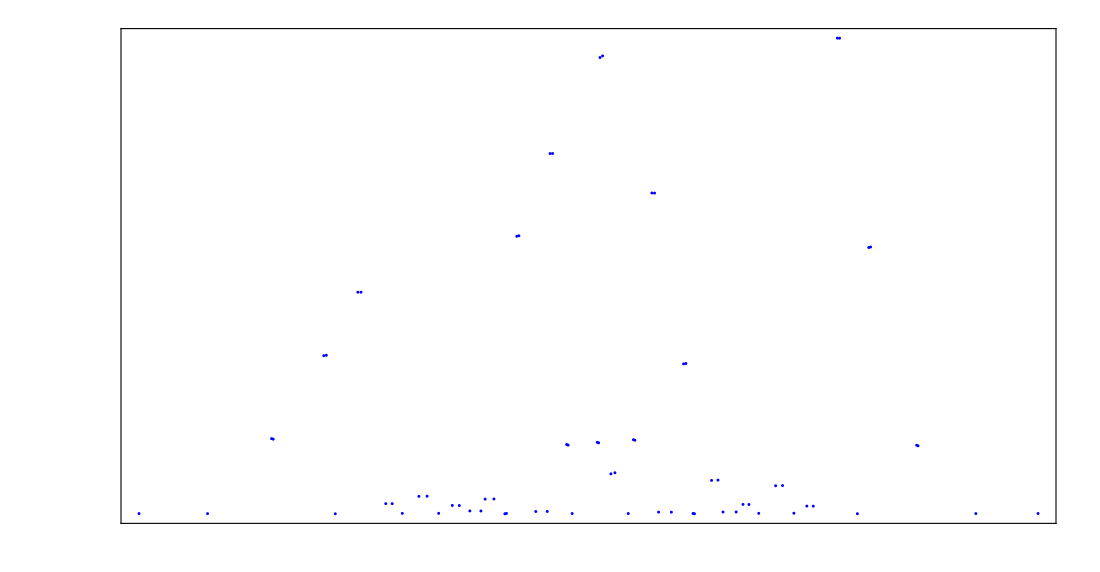
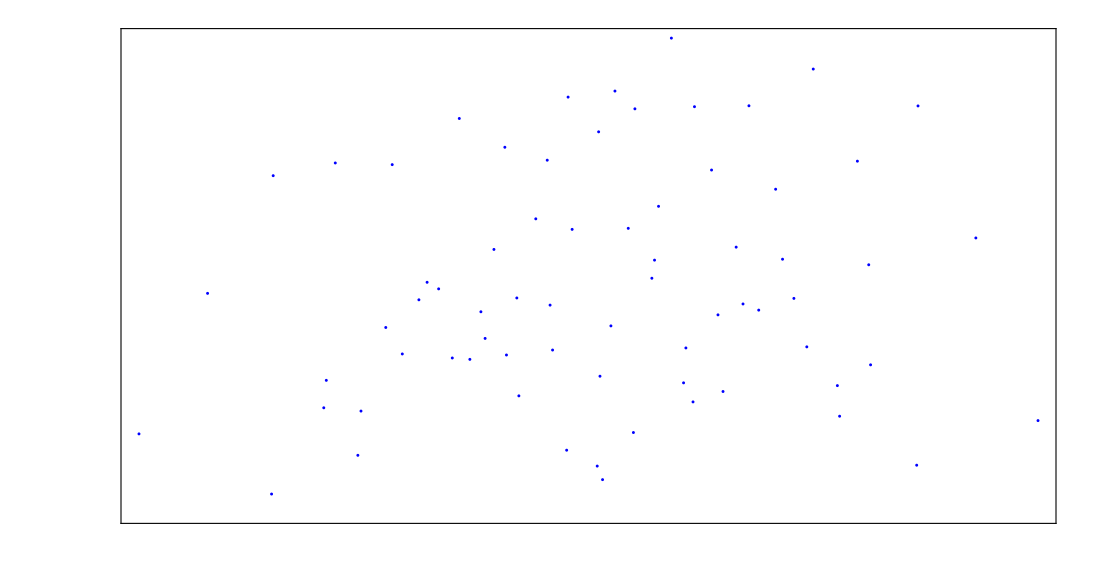
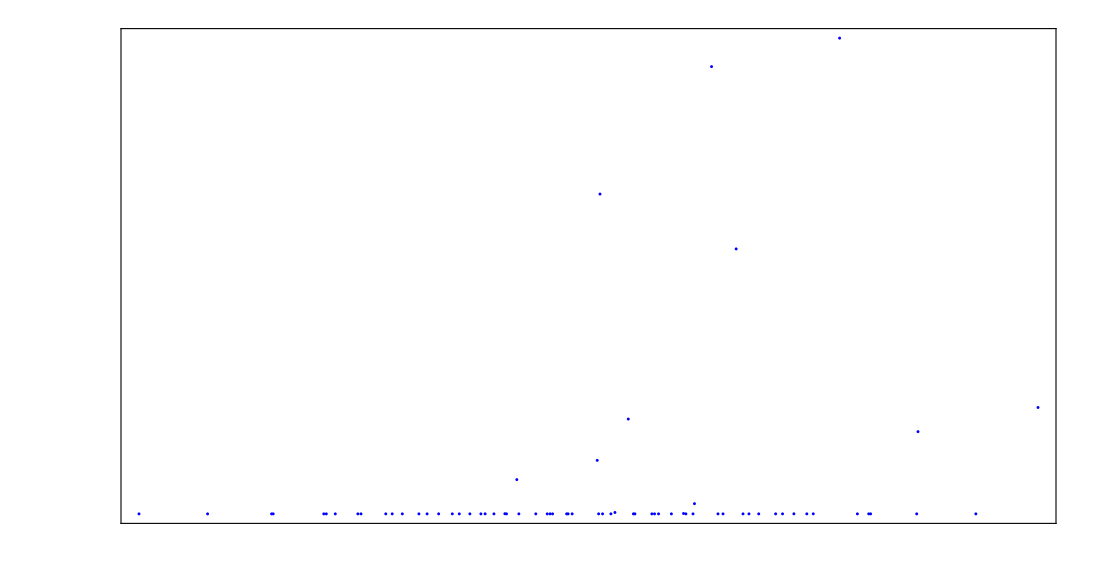
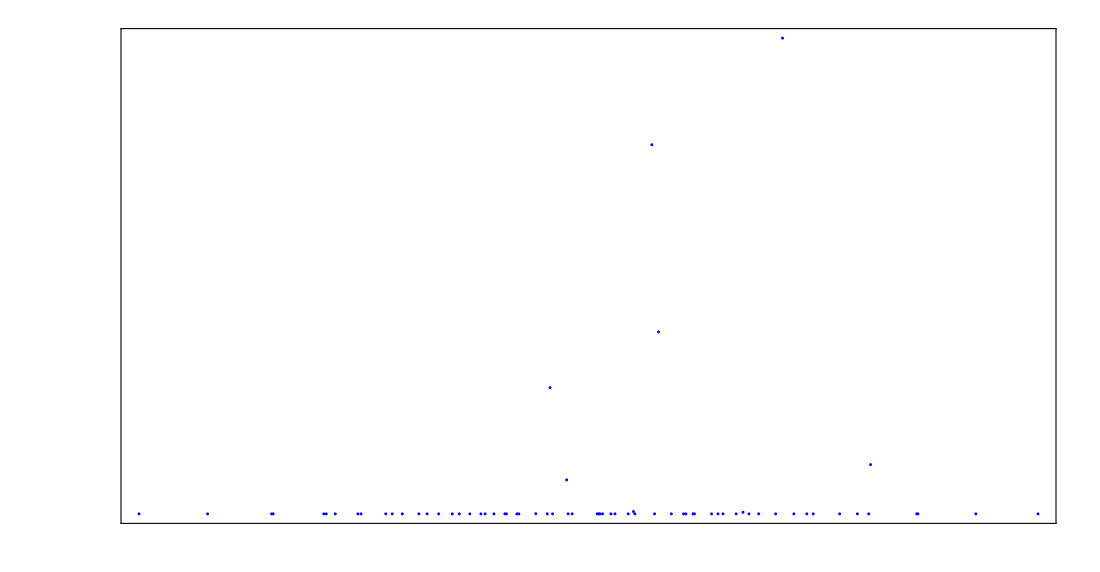
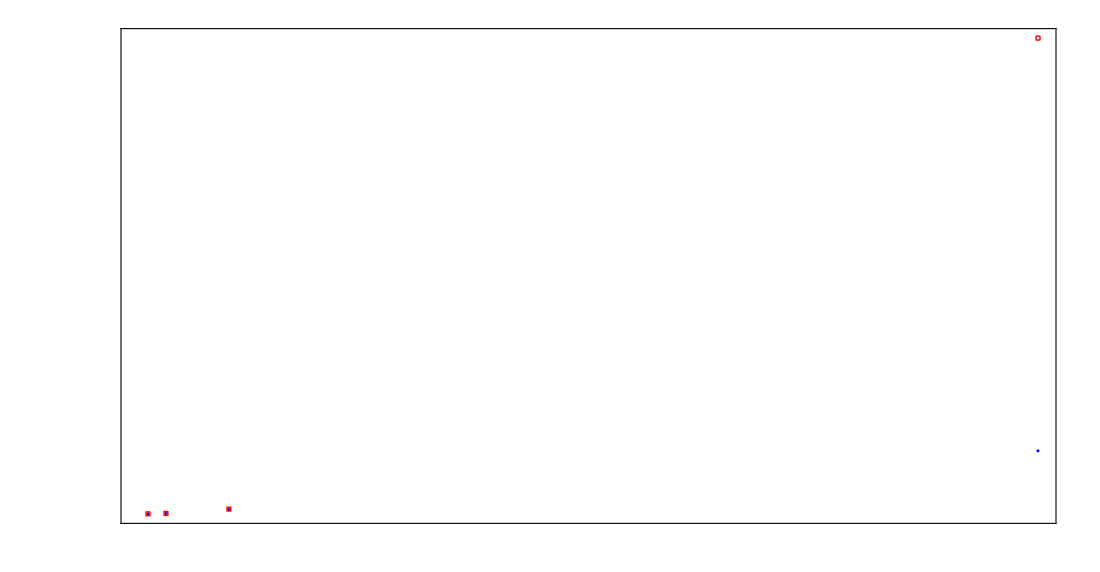
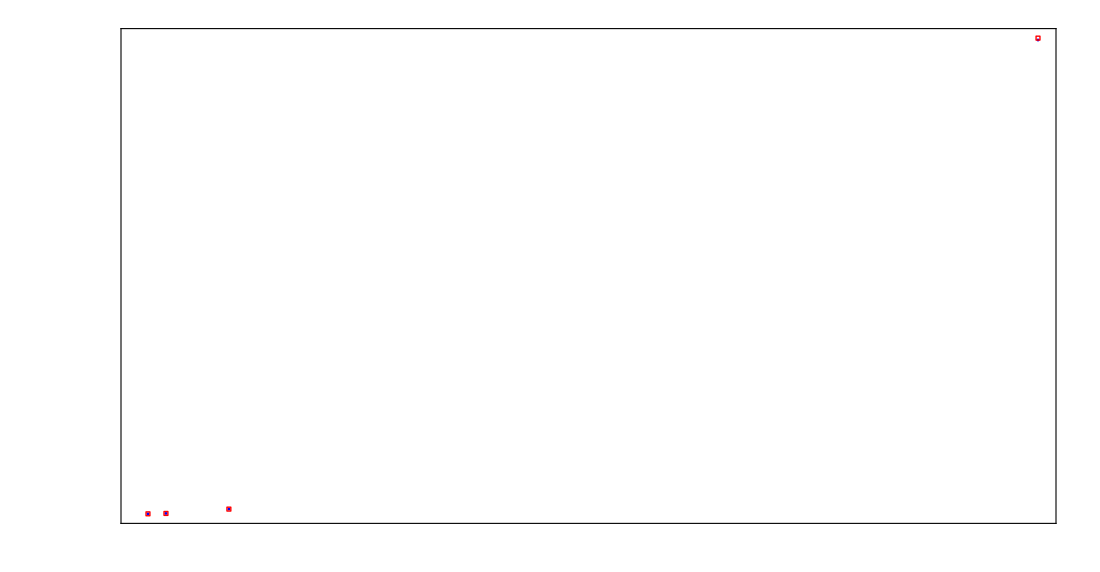
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
susCaption=Column[{tex["H_0:\\quad N="<>ToString[susModel["L"]-2]<>";\\quad J="<>texNumber[susModel["J"]]<>";\\quad \\Delta="<>texNumber[susModel["Delta"]]<>";\\quad \\mu="<>texNumber[susMu],13],
 tex["\\text{all parity sectors in the fixed magnetization space};\\quad d="<>ToString[Length[susRows]],12]}];
susPlots=<||>;
Do[With[{pts=({#["Energy"],#[key]}& /@ Select[susRows,NumericQ[#[key]]&])},
 If[pts=!={},AssociateTo[susPlots,key->plotPanel["\\text{Boundary fidelity susceptibility}",susCaption,
 Block[{plotChop=0},framePlot[{pts},"E_n",If[key==="ChiPlus","\\chi_n^{(+)}","\\chi_n^{(-)}"],{Blue},{},False,False,{{"●",3}}]]]]]],{key,{"ChiPlus","ChiMinus"}}];
If[Length[susPeaks]>0,Do[AssociateTo[susPlots,key->plotPanel["\\text{Discrete boundary transition weights}",susCaption,
 Block[{plotChop=0},framePlot[{({#["Omega"],#[key]}& /@ susPeaks)},"E_m-E_n",If[key==="WeightPlus","|\\langle m|V_+|n\\rangle|^2","|\\langle m|V_-|n\\rangle|^2"],{Blue},{},False,False,{{"●",3}},"n_{\\rm ID}="<>ToString[susSelectedID]]]]],{key,{"WeightPlus","WeightMinus"}}]];
If[ListQ[susFidelity],Do[With[{rr=Select[susFidelity,#["Sign"]==sgn&]},
 AssociateTo[susPlots,"Fidelity_"<>If[sgn==1,"plus","minus"]->plotPanel["\\text{Weak-field fidelity check}",susCaption,
 Block[{plotChop=0},framePlot[{({#["g"],#["Infidelity"]}& /@ rr),({#["g"],#["Prediction"]}& /@ rr)},"g","1-F_n",{Blue,Red},{"1-F_n","g^2\\chi_n/4"},False,False,{{"●",3},{"□",4}}]]]]],{sgn,{1,-1}}]];
If[Length[susPlots]>0,Print[Column[Values[susPlots]]]];
susDirectory=exportBundle[susOutputRoot,"ZZ_bulk_susceptibility",susPlots,
 <|"Response"->susResponse,"RankKey"->susRankKey,"EnergyWindow"->susEnergyWindow,"RankedIDs"->Lookup[susRanked,"ID"],"SelectedBulk"->susSelectedBulk,"Peaks"->susPeaks,"FidelityCheck"->susFidelity|>];
```

# 2. Dynamics of the reduced edge density matrix

### 2.1 Definitions: state preparations and observables

#### State preparation and complete state-observable records

Edge observables from the 4 x environment-rank coefficient matrix .

```mathematica
observables[t_,a_,rho0_] := Module[{r,a1,b1,sa,sb,sab,z,x,ma,mb,e},
 r=a . ConjugateTranspose[a];a1=traceB[r];b1=traceA[r];
 {sa,sb,sab}=entropy /@ {a1,b1,r};{x,z}=PauliMatrix /@ {1,3};
 ma=Re[Tr[z . a1]];mb=Re[Tr[z . b1]];e=Reverse[Sort[Re[Eigenvalues[herm[r ]]]]];
 <|"Time"->t,"RhoAB"->r,"RhoA"->a1,"RhoB"->b1,"EigenvaluesAB"->e,
  "Purity"->Re[Tr[r . r]],"EntropyA"->sa,"EntropyB"->sb,"EntropyAB"->sab,
  "MutualInfo"->sa+sb-sab,"Concurrence"->concurrence[a],"Negativity"->negativity[r],
  "InitialOverlap"->Re[Tr[rho0 . r]],"MagnetizationA"->ma,"MagnetizationB"->mb,
  "ConnectedZZ"->Re[Tr[KroneckerProduct[z,z] . r]]-ma mb,
  "ConnectedXX"->Re[Tr[KroneckerProduct[x,x] . r]]-Re[Tr[x . a1]] Re[Tr[x . b1]],
  "TraceError"->Abs[Tr[r]-1.],"HermiticityError"->Norm[r-ConjugateTranspose[r],"Frobenius"],
  "MinEigenvalue"->Last[e]|>
];
```

```mathematica
bulkFactor[p_Association,spec_Association,tol_:10^-10] := Module[
 {n=p["L"]-2,d=2^(p["L"]-2),v,h,e,w,beta,mat,emin,r},
 Switch[spec["Type"],
 "Eigenstate"|"Eigenvector",Transpose[{bulkSelectedKet[p,spec,tol]}],
 "Neel",stateFactor[neel[n,Lookup[spec,"First",0]],d,tol],
 "Polarized",stateFactor[productKet[ConstantArray[UnitVector[2,1+spec["Bit"]],n]],d,tol],
 "Helix",stateFactor[helix[n,spec["q"],spec["theta"],spec["phi"]],d,tol],
 "InfiniteT",N[IdentityMatrix[d]/Sqrt[d]],
 "Gibbs",beta=spec["Beta"];check[realQ[beta],"Beta must be finite and real."];
  {e,v}=Eigensystem[N[Normal[bulkHamiltonian[p]]]];
  w=Exp[-beta(e-If[beta>=0,Min[e],Max[e]])];w/=Total[w];Transpose[Sqrt[w] v],
 "Typical",beta=spec["Beta"];r=spec["Samples"];
  check[realQ[beta] && IntegerQ[r] && r>=1,"Invalid typicality Beta/Samples."];
  h=N[bulkHamiltonian[p]];emin=If[beta>=0,-1,1] Norm[h,Infinity];
  mat=BlockRandom[SeedRandom[spec["Seed"]];
   Transpose[Table[MatrixExp[-beta(h-emin id[d])/2,
    RandomVariate[NormalDistribution[],d]+I RandomVariate[NormalDistribution[],d]],{r}]]];
  mat/Norm[mat,"Frobenius"],
 "User",stateFactor[spec["State"],d,tol],
 _,check[False,"Bulk Type must be Eigenstate, Eigenvector, Neel, Polarized, Helix, InfiniteT, Gibbs, Typical or User."]]
];
initialFactor[p_,spec_,tol_:10^-10] := Switch[spec["Mode"],
 "Product",joinStates[stateFactor[spec["EdgeState"],4,tol],bulkFactor[p,spec["Bulk"],tol],p["L"]],
 "Full",stateFactor[spec["FullState"],2^p["L"],tol],
 _,check[False,"Initial Mode must be Product or Full."]];

stateInputDiagnostics[p_,fac_,tol_:10^-10] := Module[{gram,ha,energy,kinetic,mean,var,comm,qr,rr,ra,rb,r},
 gram=ConjugateTranspose[fac] . fac;ha=regimeHamiltonian[p] . fac;
 energy=ConjugateTranspose[fac] . ha;kinetic=ConjugateTranspose[ha] . ha;
 mean=Re[Tr[energy]];var=Max[0.,Re[Tr[kinetic]]-mean^2];
 r=Dimensions[fac][[2]];
 {qr,rr}=QRDecomposition[Join[fac,ha,2]];ra=rr[[All,1;;r]];rb=rr[[All,r+1;;2 r]];
 comm=Norm[rb . ConjugateTranspose[ra]-ra . ConjugateTranspose[rb],"Frobenius"];
 If[comm<tol,Print["The chosen initial density matrix is stationary within the diagnostic tolerance; constant observables are expected."]];
 <|"Purity"->Re[Tr[gram . gram]],"MeanEnergy"->mean,"EnergyVariance"->var,
  "CommutatorNorm"->comm,"StationaryWithinTolerance"->TrueQ[comm<tol]|>
];
```

```mathematica
spinCurrentOp[jxy_] := jxy (KroneckerProduct[PauliMatrix[1],PauliMatrix[2]]-
 KroneckerProduct[PauliMatrix[2],PauliMatrix[1]])/4;
stateRecord[t_,a_,eng_,fac0_,rho0_,purity0_] := Module[{l=eng["L"],rec,pauli,axes,ra,rb,rr,ma,mb,c,extra,cur},
 rec=observables[t,partitionFactor[a,{1,l},l],rho0];
 {ra,rb,rr}=Lookup[rec,{"RhoA","RhoB","RhoAB"}];pauli=PauliMatrix /@ Range[3];axes={"X","Y","Z"};
 ma=Re[Tr[# . ra]]& /@ pauli;mb=Re[Tr[# . rb]]& /@ pauli;
 c=Table[Re[Tr[KroneckerProduct[pauli[[i]],pauli[[j]]] . rr]],{i,3},{j,3}];
 cur={0.,0.};
 extra=Association[Join[{"PurityA"->Re[Tr[ra . ra]],"PurityB"->Re[Tr[rb . rb]],
   "FullOverlap"->Norm[ConjugateTranspose[fac0] . a,"Frobenius"]^2/purity0,
   "CurrentLeft"->cur[[1]],"CurrentRight"->cur[[2]]},
  Table["LocalA"<>axes[[i]]->ma[[i]],{i,3}],Table["LocalB"<>axes[[i]]->mb[[i]],{i,3}],
  Flatten[Table[{"Correlation"<>axes[[i]]<>axes[[j]]->c[[i,j]],
   "Connected"<>axes[[i]]<>axes[[j]]->(c[[i,j]]-ma[[i]] mb[[j]])},{i,3},{j,3}],2]]];
 Join[rec,extra]
];
stateTrajectory[eng_,fac0_,times_List,tol_:10^-8] := Module[{rho0,purity0,recs},
 check[AllTrue[times,realQ] && Length[times]>=1,"Supply real times."];
 rho0=reducedState[fac0,{1,eng["L"]},eng["L"]];purity0=Re[Tr[(ConjugateTranspose[fac0] . fac0) . (ConjugateTranspose[fac0] . fac0)]];
 recs=Table[stateRecord[t,evolve[t,eng],eng,fac0,rho0,purity0],{t,times}];
 check[Max[Lookup[recs,"TraceError"]]<tol && Min[Lookup[recs,"MinEigenvalue"]]>=-tol,"Reduced-state validation failed."];
 recs
];
```

This chapter uses only initialization definitions. It does not use a static scan, its parameters, or its eigenvectors. The initial state may be an edge/bulk product or any valid full-chain vector/density matrix, including a correlated state. Sector projections are computed before ED. The complex amplitudes between occupied sectors are retained in the full evolving factor; sector projection is not a dephasing operation.

The ZZ propagator is block diagonal in the two fixed edge spins. Only occupied conditional-bulk subspaces are diagonalized. Edge populations and z magnetizations stay fixed, boundary spin currents vanish, and coherences evolve through overlaps of different conditional-bulk trajectories. A correlated full initial state is handled by its full factor in these same blocks.

### 2.2 Independent model and time parameters

```mathematica
dynModel=<|"L"->10,"J"->1,"Delta"->0.1,"g"->0.1|>;
dynTime=<|"Grid"->"Linear","tMax"->1000.,"dt"->0.1,"tMinPositive"->0.01,"LogPoints"->201|>;
dynSettings=<|"EDTolerance"->10^-10,"ValidationTolerance"->10^-8,"ProjectionCutoff"->10^-28|>;
dynLogHorizontalAxis=False;
dynOutputRoot=resultRoot[];
dynRunLabel="ZZ_state_dynamics";
```

### 2.3 One active initial-state assignment

```mathematica
(* Choose Neel, Eigenstate (independent), or SelectedEigenvector (from section 1B). *)
dynBulkChoice="Neel";
dynBulkMu=0;
dynBulkSector=<|"R"->1,"F"->1|>;dynBulkLevel=1;
dynBulkSpecification=Switch[dynBulkChoice,
 "Neel",<|"Type"->"Neel","First"->0|>,
 "Eigenstate",<|"Type"->"Eigenstate","Mu"->dynBulkMu,"Sector"->dynBulkSector,"Level"->dynBulkLevel|>,
 "SelectedEigenvector",susSelectedBulk,
 _,check[False,"Unknown dynBulkChoice."]];
(* For a selected section-1B ket, set dynModel L,J,Delta to its Model; g remains free.
 To test generation from initially separable edges use ConstantArray[1/2,4]. *)
dynEdgeState=Normalize[{1,0,0,1}];
dynInitial=<|"Mode"->"Product","EdgeState"->dynEdgeState,"Bulk"->dynBulkSpecification|>;
(* Replace the assignment above for a bulk helix:
 dynInitial=<|"Mode"->"Product","EdgeState"->Normalize[{1,0,0,1}],
  "Bulk"-><|"Type"->"Helix","q"->Pi/3,"theta"->Pi/2,"phi"->0|>|>;
 Full helix on physical sites 1,...,L:
 dynInitial=<|"Mode"->"Full","FullState"->helix[dynModel["L"],Pi/3,Pi/2,0]|>;
 General full vector/density matrix:
 dynInitial=<|"Mode"->"Full","FullState"->yourFullState|>;
 A mixed edge state is also allowed in Product mode.
*)
```

dynInitial=<|"Mode"->"Product","EdgeState"->Normalize[{1,0,0,1}],

```mathematica
(*  "Bulk"-><|"Type"->"Helix","q"->Pi/3,"theta"->Pi/2,"phi"->0|>|>;*)
```

The helix is a freely chosen initial product state. No matched boundary field or rigid-rotation protocol is added. Bulk alternatives are Polarized (Bit), InfiniteT, Gibbs (Beta), Typical (Beta, Samples, Seed), and User (State). Gibbs/Typical use only the field-free L-2-site bulk Hamiltonian.

```mathematica
(*Build the isolated-bulk catalog for the current dynamics model.*)
dynBulkCatalog=bulkEigenCatalog[dynModel,0,dynSettings["EDTolerance"]];
(*Select catalog ID 19,including its exact eigenvector.*)
dynBulkSpecification=bulkEigenSpec[dynBulkCatalog,46];
(*Initially separable edges|++>,to test entanglement generation.*)
dynEdgeState=ConstantArray[1/2,4];
dynInitial=<|"Mode"->"Product","EdgeState"->dynEdgeState,"Bulk"->dynBulkSpecification|>;
Print[Dataset[dynBulkSpecification["Selection"]]];
```

### 2.4 Assemble the factor, inspect sector weights, and diagonalize occupied sectors

```mathematica
dynModelUsed=regimeModel[dynModel];dynInitialUsed=dynInitial;dynSettingsUsed=dynSettings;dynTimeUsed=dynTime;
dynFactor=initialFactor[dynModelUsed,dynInitialUsed,dynSettingsUsed["ValidationTolerance"]];
dynInitialDiagnostics=stateInputDiagnostics[dynModelUsed,dynFactor,dynSettingsUsed["EDTolerance"]];
dynTimes=timeGrid[dynTimeUsed];
{dynSetupSeconds,dynEngine}=AbsoluteTiming[occupiedEngine[dynModelUsed,dynFactor,
 dynSettingsUsed["EDTolerance"],dynSettingsUsed["ProjectionCutoff"]]];
Print["Initial-factor reconstruction error: ",dynEngine["ReconstructionError"],
 "; discarded weight: ",dynEngine["DiscardedWeight"]];
Print[Dataset[dynEngine["SectorWeights"]]];
```

Initial-factor reconstruction error: 3.38792×10^-15; discarded weight: 2.63078×10^-32

### 2.5 Evolve and compute all reduced-state observables

```mathematica
{dynSeconds,dynRecords}=AbsoluteTiming[stateTrajectory[dynEngine,dynFactor,dynTimes,dynSettingsUsed["ValidationTolerance"]]];
dynPlotSnapshot=<|"Model"->dynModelUsed,"TimeSettings"->dynTimeUsed,"Times"->Lookup[dynRecords,"Time"]|>;
Print[Dataset[KeyTake[#, {"Time","EntropyAB","Concurrence","Negativity","TraceError"}]& /@ Take[dynRecords,UpTo[8]]]];
```

### 2.6 MaTeX plots

```mathematica
If[!AssociationQ[dynPlotSnapshot],dynPlotSnapshot=<|"Model"->dynModelUsed,"TimeSettings"->dynTimeUsed,"Times"->Lookup[dynRecords,"Time"]|>];
chopRecordsInPlace[dynRecords,recordChopTolerance];
```

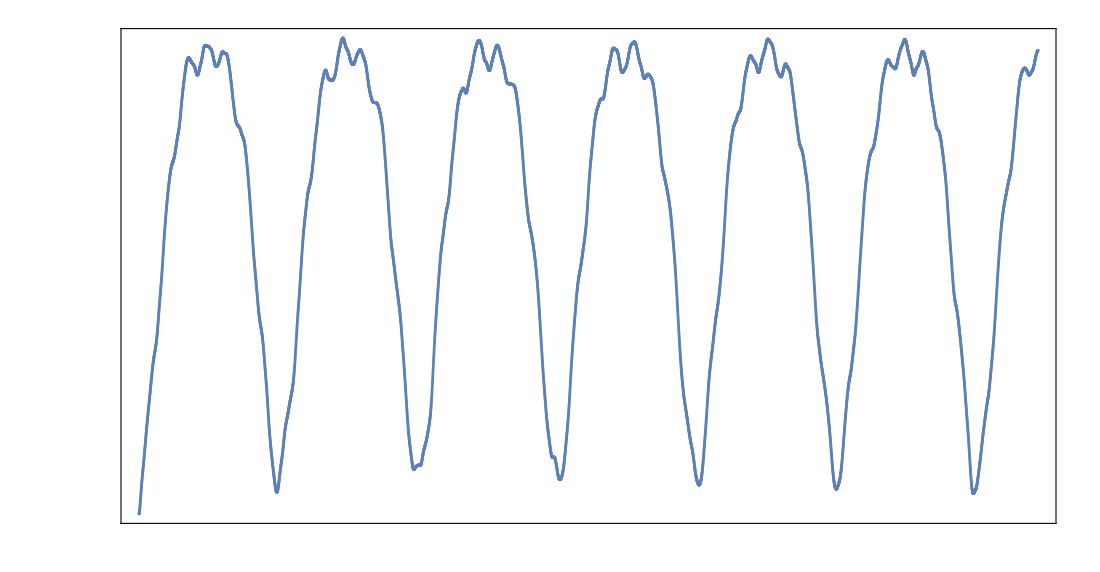
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
dynPlots=statePlots[dynRecords,dynPlotSnapshot,dynLogHorizontalAxis];
Print[dynPlots["EntropyAB"]];
```

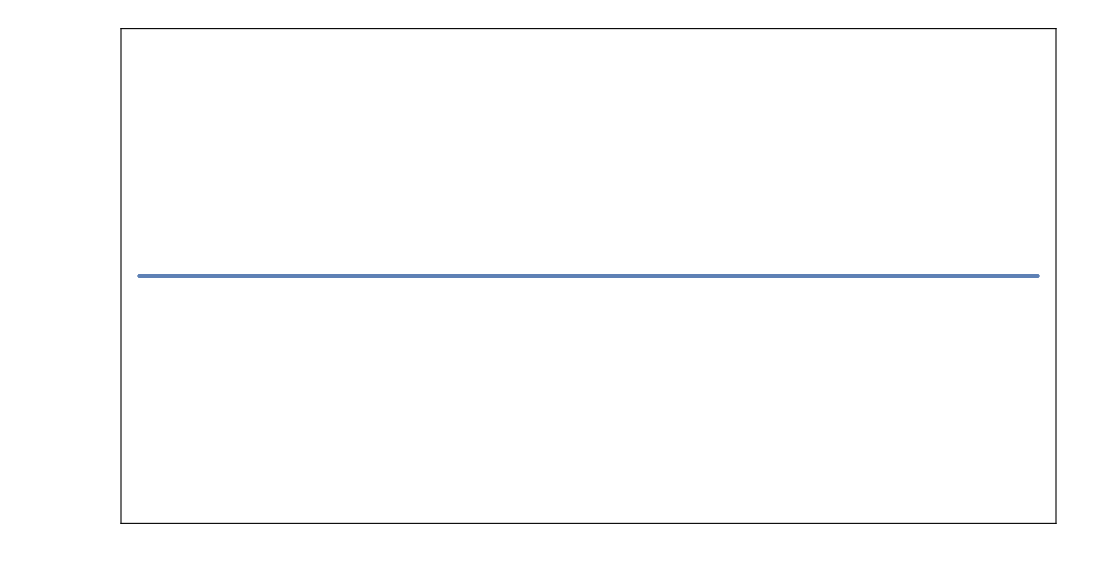
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Print[dynPlots["TraceError"]];
```

### 2.7 Export this independent trajectory

```mathematica
dynDirectory=exportBundle[dynOutputRoot,dynRunLabel,dynPlots,
 <|"Model"->dynModelUsed,"InitialSpecification"->dynInitialUsed,"InitialFactor"->dynFactor,
 "Settings"->dynSettingsUsed,"InitialDiagnostics"->dynInitialDiagnostics,"TimeSettings"->dynTimeUsed,"Times"->dynTimes,
 "Engine"->dynEngine,"SetupSeconds"->dynSetupSeconds,"EvolutionSeconds"->dynSeconds,"Records"->dynRecords|>];
Print[dynDirectory];
```

C:\Users\Miguel\Documents\GitHub\Spin-transport\xxz_impurities_characterization\xxz_edge_regimes_results\ZZ_state_dynamics_run4

### 2.8 Optional eigenstate comparison at fixed edge input, model and time grid

Run after chapter-2 definitions. This test needs no section-1B evaluation.

```mathematica
boundaryDynamicsTest[p_,mu_,ids_List,ts_List,edge_,tol_:10^-10,cut_:10^-28] := Module[{cat,resp,fac,eng,recs,out={},row},
 cat=bulkEigenCatalog[p,mu,tol];resp=boundaryResponse[cat,tol];
 Do[fac=joinStates[stateFactor[edge,4,tol],Transpose[{bulkEigenKet[cat,k]}],p["L"]];
  eng=occupiedEngine[p,fac,tol,cut];recs=stateTrajectory[eng,fac,ts,100 tol];row=resp["Rows"][[k]];
  AppendTo[out,<|"Eigenstate"->row,"BulkSpecification"->bulkEigenSpec[cat,k],"SectorWeights"->eng["SectorWeights"],
   "DiscardedWeight"->eng["DiscardedWeight"],"Records"->recs,"MaxConcurrence"->Max[Lookup[recs,"Concurrence"]],
   "MaxNegativity"->Max[Lookup[recs,"Negativity"]],"MaxEdgeBulkEntropy"->Max[Lookup[recs,"EntropyAB"]]|>],{k,ids}];
 <|"Model"->p,"Mu"->mu,"Times"->ts,"EdgeInput"->edge,"Results"->out|>
];
```

```mathematica
(* Optional controlled comparison. Use IDs from a catalog with identical L,J,Delta,mu.
 A product |++> edge input tests GENERATION rather than decay of pre-existing Bell entanglement. *)
```

```mathematica
testEigenstates=False;
testModel=<|"L"->8,"J"->1,"Delta"->0.45,"g"->0.1|>;
testMu=0;testIDs={1,2};testTimes=N[Range[0,100,1/2]];
testEdge=ConstantArray[1/2,4];
If[TrueQ[testEigenstates],
 testRun=boundaryDynamicsTest[testModel,testMu,testIDs,testTimes,testEdge];
 Print[Dataset[(Join[KeyTake[#["Eigenstate"],{"ID","Energy","ChiPlus","ChiMinus"}],KeyTake[#,{"MaxConcurrence","MaxNegativity","MaxEdgeBulkEntropy"}]]& /@ testRun["Results"])]];
 testPlots=Association[Table["Concurrence_state_"<>ToString[r["Eigenstate"]["ID"]]->recordPlot[r["Records"],{"Concurrence"},observableLabel["Concurrence"],
 "\\text{Edge entanglement: bulk state }"<>ToString[r["Eigenstate"]["ID"]],testRun["Model"]],{r,testRun["Results"]}]];
 testDirectory=exportBundle[resultRoot[],"ZZ_eigenstate_comparison",testPlots,testRun]];
```

# 3. Dynamics of the edge dynamical map

### 3.1 Definitions: complete map from a fixed bulk preparation

#### Channel construction, diagnostics and long-time average

```mathematica
edgeMapFactor[f_,l_] := joinStates[IdentityMatrix[4],f,l];
choiFactor[a_,l_] := Module[{r=Dimensions[a][[2]]/4},
 check[IntegerQ[r],"The general Choi factor requires 4r columns."];
 ArrayReshape[Transpose[ArrayReshape[partitionFactor[a,{1,l},l],{4,2^(l-2),4,r}],{2,3,1,4}],{16,2^(l-2) r}]
];
choiToTransfer[c_] := ArrayReshape[Transpose[ArrayReshape[c,{4,4,4,4}],{3,1,4,2}],{16,16}];
transferToChoi[s_] := ArrayReshape[Transpose[ArrayReshape[s,{4,4,4,4}],{2,4,1,3}],{16,16}];
applyTransfer[s_,x_] := ArrayReshape[s . Flatten[x],{4,4}];
choiTraceOut[c_] := TensorContract[ArrayReshape[c,{4,4,4,4}],{{2,4}}];
choiPartialTransposeOut[c_] := ArrayReshape[Transpose[ArrayReshape[c,{4,4,4,4}],{1,4,3,2}],{16,16}];
mapBuild[p_,bulkFac_,tol_:10^-10,projectionCut_:0] := Module[{a,eng},
 check[MatrixQ[bulkFac,NumericQ] && Length[bulkFac]==2^(p["L"]-2) &&
  Abs[Norm[bulkFac,"Frobenius"]^2-1]<100 tol,"Invalid normalized bulk factor."];
 a=joinStates[ConstantArray[1.,{4,1}],bulkFac,p["L"]];
 eng=occupiedEngine[p,a,tol,projectionCut];
 Join[eng,<|"BulkFactor"->bulkFac,"MapConstruction"->"ConditionalBulkGram"|>]
];
mapChoiFromFactor[a_,l_] := Module[{w=partitionFactor[a,{1,l},l],k,ids={1,6,11,16}},k=w . ConjugateTranspose[w]; Normal[SparseArray[Flatten[Table[{ids[[i]],ids[[j]]}->k[[i,j]],{i,4},{j,4}],1],{16,16}]]];
mapChoiDerivative[a_,ad_,l_] := Module[{w=partitionFactor[a,{1,l},l],wd=partitionFactor[ad,{1,l},l],k,ids={1,6,11,16}},k=wd . ConjugateTranspose[w]+w . ConjugateTranspose[wd];Normal[SparseArray[Flatten[Table[{ids[[i]],ids[[j]]}->k[[i,j]],{i,4},{j,4}],1],{16,16}]]];
mapAt[t_,eng_] := Module[{a=evolve[t,eng],ad=evolveDot[t,eng],c,cd},
 c=mapChoiFromFactor[a,eng["L"]];cd=mapChoiDerivative[a,ad,eng["L"]];
 <|"Choi"->c,"ChoiState"->c/4,"Transfer"->choiToTransfer[c],"TransferDerivative"->choiToTransfer[cd]|>
];
```

```mathematica
traceNormHermitian[x_] := Total[Abs[Eigenvalues[herm[x]]]];
transferMinSV[s_] := Min[PadRight[SingularValueList[s,Tolerance->0],16]];
rightSolve[a_,b_] := Transpose[LinearSolve[Transpose[b],Transpose[a]]];
pauliBasis2[] := Flatten[Table[KroneckerProduct[PauliMatrix[m],PauliMatrix[n]]/2,{m,0,3},{n,0,3}],1];
gksMatrix[lsup_] := Table[Tr[ConjugateTranspose[KroneckerProduct[ga,Conjugate[gb]]] . lsup],
 {ga,Rest[pauliBasis2[]]},{gb,Rest[pauliBasis2[]]}];
canonicalRates[lsup_] := Sort[Re[Eigenvalues[herm[gksMatrix[lsup]]]]];
unitarySuper[u_] := KroneckerProduct[u,Conjugate[u]];
swapEdge[] := {{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}};
flipEdge[] := KroneckerProduct[PauliMatrix[1],PauliMatrix[1]];
covarianceViolation[s_,u_] := maxAbs[s . unitarySuper[u]-unitarySuper[u] . s];
u1CovarianceViolation[s_] := Module[{q=Flatten[Outer[Subtract,{1,0,0,-1},{1,0,0,-1}]]},
 maxAbs[s Map[Boole,Outer[Unequal,q,q],{2}]]];
coherenceBlock[s_,q_Integer] := With[{ids=Flatten[Position[Flatten[Outer[Subtract,{1,0,0,-1},{1,0,0,-1}]],q]]},s[[ids,ids]]];
signalMatrix[s_,rhoB_] := Table[Re[Tr[PauliMatrix[a] . traceA[applyTransfer[s,KroneckerProduct[PauliMatrix[b],rhoB]]]]]/2,{a,3},{b,3}];
retentionMatrix[s_,rhoB_] := Table[Re[Tr[PauliMatrix[a] . traceB[applyTransfer[s,KroneckerProduct[PauliMatrix[b],rhoB]]]]]/2,{a,3},{b,3}];
mapRecord[t_,eng_,cfg_,probes_] := Module[{v=mapAt[t,eng],c,s,sd,e,pt,sv,gen,rates,rhoMixed,lambda,extra},
 {c,s,sd}=Lookup[v,{"Choi","Transfer","TransferDerivative"}];
 e=Sort[Re[Eigenvalues[herm[c]]]];pt=Sort[Re[Eigenvalues[herm[choiPartialTransposeOut[c/4]]]]];
 sv=transferMinSV[s];
 If[sv>=cfg["MinimumSingularValue"],gen=rightSolve[sd,s];rates=canonicalRates[gen],
  gen=Missing["NearSingularMap",sv];rates=ConstantArray[Missing["NearSingularMap",sv],15]];
 rhoMixed=applyTransfer[s,IdentityMatrix[4]/4];lambda=applyTransfer[s,SparseArray[{{1,4}->1},{4,4}]][[1,4]];
 extra=<|"Time"->t,"ChoiEigenvalues"->e,"MinChoiEigenvalue"->First[e],
  "TPError"->maxAbs[choiTraceOut[c]-IdentityMatrix[4]],"ChoiTraceError"->Abs[Tr[c]-4],
  "KrausRank"->Count[e,x_/;x>cfg["RankTolerance"] Max[1.,Max[e]]],"MapEntropy"->entropy[c/4],
  "ChoiPTMinimum"->First[pt],"ChoiNegativity"->Total[Clip[-pt,{0,Infinity}]],
  "MinSingularValue"->sv,"Generator"->gen,"CanonicalRates"->rates,
  "MinimumRate"->If[MissingQ[gen],Missing["NearSingularMap"],First[rates]],
  "RHPInstantaneous"->If[MissingQ[gen],Missing["NearSingularMap"],Total[Clip[-rates,{0,Infinity}]]/2],
  "UnitalityError"->maxAbs[rhoMixed-IdentityMatrix[4]/4],"MixedInputEntropy"->entropy[rhoMixed],
  "U1CovarianceError"->u1CovarianceViolation[s],"ReflectionCovarianceError"->covarianceViolation[s,swapEdge[]],
  "FlipCovarianceError"->covarianceViolation[s,flipEdge[]],"RFCovarianceError"->covarianceViolation[s,swapEdge[] . flipEdge[]],
  "TimeReversalError"->maxAbs[mapAt[-t,eng]["Transfer"]-Conjugate[s]],
  "DoubleQuantumReal"->Re[lambda],"DoubleQuantumImag"->Im[lambda],"DoubleQuantumAbs"->Abs[lambda],
  "BLPDistance"->traceNormHermitian[applyTransfer[s,probes["Rho1"]-probes["Rho2"]]]/2,
  "SignalAtoB"->Norm[signalMatrix[s,probes["RhoB"]],2],
  "RetentionA"->Norm[retentionMatrix[s,probes["RhoB"]],2]|>;
 Join[v,extra]
];
mapTrajectory[eng_,times_List,cfg_,probes_] := Module[{recs,dist,rhp,dt,previous,s0},
 check[Length[times]>=2 && AllTrue[times,realQ] && And@@Thread[Differences[times]>0],"Map times must increase."];
 check[realQ[cfg["MinimumSingularValue"]] && cfg["MinimumSingularValue"]>0 &&
  realQ[cfg["RankTolerance"]] && cfg["RankTolerance"]>0,"Invalid map tolerances."];
 stateFactor[probes["Rho1"],4,cfg["ValidationTolerance"]];stateFactor[probes["Rho2"],4,cfg["ValidationTolerance"]];
 stateFactor[probes["RhoB"],2,cfg["ValidationTolerance"]];
 check[MatrixQ[probes["Rho1"]] && MatrixQ[probes["Rho2"]] && MatrixQ[probes["RhoB"]],"Map probes must be density matrices."];
 s0=mapAt[0,eng]["Transfer"];check[maxAbs[s0-IdentityMatrix[16]]<cfg["ValidationTolerance"],"The t=0 map is not identity."];
 recs=mapRecord[#,eng,cfg,probes]& /@ times;
 check[Max[Lookup[recs,"TPError"]]<cfg["ValidationTolerance"] &&
  Min[Lookup[recs,"MinChoiEigenvalue"]]>=-cfg["ValidationTolerance"],"Choi CP/TP validation failed."];
 dist=Lookup[recs,"BLPDistance"];
 Table[dt=If[k==1,Missing["NoPreviousTime"],times[[k]]-times[[k-1]]];
  rhp=If[k==1,Missing["NoPreviousTime"],If[recs[[k-1]]["MinSingularValue"]<cfg["MinimumSingularValue"],
   Missing["NearSingularMap"],Max[0.,traceNormHermitian[transferToChoi[rightSolve[recs[[k]]["Transfer"],recs[[k-1]]["Transfer"]]]]/4-1]]];
  Join[recs[[k]],<|"BLPAccumulated"->Total[Clip[Differences[Take[dist,k]],{0,Infinity}]],
   "RHPFiniteStep"->rhp,"RHPFiniteStepRate"->If[MissingQ[rhp],rhp,rhp/dt]|>],{k,Length[recs]}]
];
```

```mathematica
mapLevelFactors[eng_,item_] := Module[{s=eng["Sectors"][[item[[2]]]],v,c,w},
 v=ConstantArray[0.+0.I,eng["Dimension"]];v[[s["Indices"]]]=s["V"][[All,item[[3]]]]+0.I;
 c=s["C"][[item[[3]]]];
 w=partitionFactor[Transpose[{v}],{1,eng["L"]},eng["L"]];
 {w,c}
];
mapLevelCross[a_,b_] := Module[{k=(a[[2]] . Conjugate[b[[2]]]) (a[[1]] . ConjugateTranspose[b[[1]]]),ids={1,6,11,16}},Normal[SparseArray[Flatten[Table[{ids[[i]],ids[[j]]}->k[[i,j]],{i,4},{j,4}],1],{16,16}]]];
mapSingletonChoi[eng_,item_] := With[{a=mapLevelFactors[eng,item]},mapLevelCross[a,a]];
mapClusterChoi[eng_,cluster_] := Module[{f=mapLevelFactors[eng,#]& /@ cluster,c,x},
 c=Total[mapLevelCross[#,#]& /@ f];
 Do[x=mapLevelCross[f[[i]],f[[j]]];c+=x+ConjugateTranspose[x],{i,Length[f]},{j,i+1,Length[f]}];c
];
energyClusters[eng_,absoluteTol_] := Module[{levels,clusters={},current},
 levels=SortBy[Flatten[Table[{eng["Sectors"][[k]]["E"][[n]],k,n},
  {k,Length[eng["Sectors"]]},{n,Length[eng["Sectors"][[k]]["E"]]}],1],First];
 current={First[levels]};
 Do[If[item[[1]]-current[[1,1]]<=absoluteTol,AppendTo[current,item],AppendTo[clusters,current];current={item}],{item,Rest[levels]}];
 Append[clusters,current]
];
timeAveragedMap[eng_,relativeTol_:10^-10] := Module[{scale,clusters,c,widths},
 check[realQ[relativeTol] && relativeTol>0,"Energy-cluster tolerance must be positive."];
 scale=Max[1.,maxAbs[Lookup[eng["Sectors"],"E"]]];clusters=energyClusters[eng,relativeTol scale];
 c=ConstantArray[0.+0.I,{16,16}];
 Do[If[Length[cluster]==1,c+=mapSingletonChoi[eng,First[cluster]];Continue[]];
  c+=mapClusterChoi[eng,cluster],{cluster,clusters}];
 widths=Last[#][[1]]-First[#][[1]]& /@ clusters;
 <|"Choi"->c,"ChoiState"->c/4,"Transfer"->choiToTransfer[c],
  "RelativeEnergyTolerance"->relativeTol,"AbsoluteEnergyTolerance"->relativeTol scale,
  "Clusters"->clusters,"ClusterWidths"->widths,"MaxClusterWidth"->Max[widths],
  "SingletonClusters"->Count[Length /@ clusters,1],"DegenerateClusters"->Count[Length /@ clusters,_?(#>1&)],
  "TPError"->maxAbs[choiTraceOut[c]-IdentityMatrix[4]],"MapEntropy"->entropy[c/4],
  "ChoiPTMinimum"->Min[Re[Eigenvalues[herm[choiPartialTransposeOut[c/4]]]]]|>
];

onsetTime[times_List,vals_List,threshold_] := Module[{pos,k},
 check[Length[times]==Length[vals] && realQ[threshold] && threshold>0,"Invalid onset threshold/data."];
 pos=FirstPosition[vals,x_/;NumericQ[x] && x>threshold,Missing["BelowThreshold"]];
 If[MissingQ[pos],Return[pos]];k=First[pos];
 If[k==1,First[times],times[[k-1]]+(threshold-vals[[k-1]]) (times[[k]]-times[[k-1]])/(vals[[k]]-vals[[k-1]])]
];
```

For a fixed normalized bulk state rhoM, Phi_t(X)=Tr_M[U_t (X tensor rhoM) U_t dagger]. C_t=sum_ij |i><j| tensor Phi_t(|i><j|); Tr C_t=4 and C_t/4 is the Choi state. C_t depends only on the model, bulk state and time. There is no initial-edge-state input to chBuild. Full correlated preparations belong to chapter 2; one cannot assign them a universal CPTP map for arbitrary edge inputs.

ZZ fast implementation: diagonalize only occupied conditional BULK magnetization blocks. At zero fields reuse spin-flip partner eigenvectors; equal end couplings allow reflection-parity ED. Evolve pruned columns in real-arithmetic time batches for pure/low-rank states, or cache six overlap matrices for a rank-independent mixed-bulk time loop. Automatic selects by estimated cost and cache limit. Only the bulk-sector-diagonal part of rhoM affects this channel; no sector dephasing is applied to the exchange preparation.

Map observables include CP/TP diagnostics, Choi spectrum/entropy/rank, reference-output negativity, exact time-local generator and canonical rates where invertible, finite-step and instantaneous RHP witnesses, selected-pair BLP backflow, covariance violations, unitality, double-quantum coherence, signalling and retention. Probe edge states below affect only BLP/signalling diagnostics, not the Choi matrix. A PPT Choi state does not prove entanglement breaking in 4x4.

#### Fast channel definitions: conditional/column-pruned batches

```mathematica
chMapSectors[n_Integer] := Values[KeySort[PositionIndex[DigitCount[Range[0, 2^n - 1], 2, 1]]]];
chMapReflectPerm[ix_List, n_Integer] := Lookup[AssociationThread[ix, Range[Length[ix]]], IntegerReverse[ix - 1, 2, n] + 1];
chMapParityQ[ix_List, n_Integer] := Module[{d = Length[ix], jr, fix, pr, nf, qe, qo},
  jr = chMapReflectPerm[ix, n]; fix = Flatten[Position[jr - Range[d], 0]];
  pr = Select[Transpose[{Range[d], jr}], #[[1]] < #[[2]] &]; nf = Length[fix];
  qe = SparseArray[Join[Thread[Transpose[{fix, Range[nf]}] -> 1.],
      Thread[Transpose[{pr[[All, 1]], nf + Range[Length[pr]]}] -> 1/Sqrt[2.]],
      Thread[Transpose[{pr[[All, 2]], nf + Range[Length[pr]]}] -> 1/Sqrt[2.]]], {d, nf + Length[pr]}];
  qo = If[pr === {}, Nothing, SparseArray[Join[Thread[Transpose[{pr[[All, 1]], Range[Length[pr]]}] -> 1/Sqrt[2.]],
      Thread[Transpose[{pr[[All, 2]], Range[Length[pr]]}] -> -1/Sqrt[2.]]], {d, Length[pr]}]];
  {qe, qo}];
chEDTolerance=10^-10;
chMapSectorEigen[h_,ix_List,n_Integer,parity_] := Module[{hb=N[h[[ix,ix]]],es,out,perm,scale},
 scale=Max[1.,Norm[hb,Infinity]];
 check[maxAbs[Im[hb]]<=chEDTolerance scale && maxAbs[hb-ConjugateTranspose[hb]]<=chEDTolerance scale,"Channel ED requires a real symmetric Hamiltonian."];
 If[TrueQ[parity] && Length[ix]>1,
  perm=chMapReflectPerm[ix,n];check[maxAbs[hb-hb[[perm,perm]]]<=chEDTolerance scale,"Channel reflection block is not invariant."];
  es=Table[With[{x=Eigensystem[Normal[Transpose[q] . hb . q]]},{x[[1]],Normal[q . Transpose[x[[2]]]]}],{q,chMapParityQ[ix,n]}];
  out=<|"E"->Join@@es[[All,1]],"V"->Join[Sequence@@es[[All,2]],2]|>,
  es=Eigensystem[Normal[hb]];out=<|"E"->es[[1]],"V"->Transpose[es[[2]]]|>];
 check[maxAbs[hb . out["V"]-Transpose[out["E"] Transpose[out["V"]]]]<=100 chEDTolerance scale,"Channel eigenpair residual failed."];
 check[maxAbs[Total[out["V"]^2]-1]<=100 chEDTolerance,"Channel eigenvector normalization failed."];out
];
```

```mathematica
chMapPhaseBlock[e_List, c_?MatrixQ, tc_List, dot_ : False] := Module[{ph = Exp[-I Outer[Times, e, tc]]},
  If[TrueQ[dot], ph = -I e ph];
  ArrayReshape[Transpose[Table[ph[[All, tau]] c, {tau, Length[tc]}], {2, 1, 3}], {Length[e], Length[tc] Last[Dimensions[c]]}]];
chMapRealDot[v_?MatrixQ, b_?MatrixQ] := v . Re[b] + I v . Im[b];
```

```mathematica
chMapGibbsFactor[delta_, p_Association, beta_?NumericQ] := Module[{n = p["L"], h, sec, es, e0, w, fac, col = 0},
  h = chChainHamiltonian[delta, p]; sec = chMapSectors[n];
  es = Table[Eigensystem[Normal[h[[ix, ix]]]], {ix, sec}]; e0 = If[beta>=0,Min,Max][Flatten[es[[All, 1]]]];
  fac = ConstantArray[0., {2^n, 2^n}];
  Do[w = Sqrt[Exp[-beta (es[[k, 1]] - e0)]]; fac[[sec[[k]], col + Range[Length[w]]]] = Transpose[w es[[k, 2]]]; col += Length[w], {k, Length[sec]}];
  fac/Norm[fac, "Frobenius"]];
chMapTypicalFactor[delta_, p_Association, beta_?NumericQ, nr_Integer, seed_Integer : 1] := Module[{n = p["L"], h, sec, e0, cols},
  h = chChainHamiltonian[delta, p]; sec = chMapSectors[n]; e0 = If[beta>=0,-1,1] Norm[h, Infinity];
  cols = BlockRandom[SeedRandom[seed]; Flatten[Table[With[{hk = h[[ix, ix]] - e0 SparseArray[Band[{1, 1}] -> 1., {Length[ix], Length[ix]}]},
       Table[Module[{v = ConstantArray[0. + 0. I, 2^n]},
         v[[ix]] = MatrixExp[-beta hk/2, RandomVariate[NormalDistribution[], Length[ix]] + I RandomVariate[NormalDistribution[], Length[ix]]]; v], {nr}]],
      {ix, sec}], 1]];
  Transpose[cols]/Norm[cols, "Frobenius"]];
```

```mathematica
chChoiToSuper[chi_] := 4 ArrayReshape[Transpose[ArrayReshape[chi, {4, 4, 4, 4}], {3, 1, 4, 2}], {16, 16}];
chSuperToChoi[s_] := ArrayReshape[Transpose[ArrayReshape[s, {4, 4, 4, 4}], {2, 4, 1, 3}], {16, 16}]/4;
chChoiToSuperSeries[chis_] := 4 ArrayReshape[Transpose[ArrayReshape[chis, {Length[chis], 4, 4, 4, 4}], {1, 4, 2, 5, 3}], {Length[chis], 16, 16}];
chChoiTraceOut[chi_] := TensorContract[ArrayReshape[chi, {4, 4, 4, 4}], {{2, 4}}];
```

```mathematica
chZzSigns = {{1, 1}, {1, -1}, {-1, 1}, {-1, -1}};
chZzConditionalH[delta_, p_, s_Integer] := chChainHamiltonian[delta, p] +
   chZzSigns[[s, 1]] p["gA"]/4 chSiteOp[delta, chPauli[delta, 3], 1, p["L"]] +
   chZzSigns[[s, 2]] p["gB"]/4 chSiteOp[delta, chPauli[delta, 3], p["L"], p["L"]];
chZzSymmetries[p_] := <|"Flip" -> TrueQ[p["w"] == 0 && p["ed"] == 0],
   "Reflect" -> TrueQ[p["gA"] == p["gB"] && (p["ed"] == 0 || 2 p["DefectSite"] == p["L"] + 1)]|>;
Options[chZzEngine] = {"Symmetries" -> Automatic};
chZzEngine[delta_?NumericQ, p_Association, chainFactor_?MatrixQ, OptionsPattern[]] := Module[
  {n = p["L"], sec, occ, sym, need, eig = <||>, flipK, fromFlip, blocks},
  sec = chMapSectors[n];
  occ = Select[Range[n + 1], Max[Abs[chainFactor[[sec[[#]]]]]] > 0. &];
  sym = If[OptionValue["Symmetries"] === Automatic, chZzSymmetries[p], <|"Flip" -> False, "Reflect" -> False|>];
  flipK[k_] := n + 2 - k;
  need = If[sym["Flip"], Union[occ, flipK /@ occ], occ];
  fromFlip[src_] := Association[# -> <|"E" -> src[flipK[#]]["E"], "V" -> Reverse[src[flipK[#]]["V"]]|> & /@ occ];
  eig[1] = With[{h = chZzConditionalH[delta, p, 1]}, AssociationMap[chMapSectorEigen[h, sec[[#]], n, sym["Reflect"]] &, need]];
  eig[2] = With[{h = chZzConditionalH[delta, p, 2]}, AssociationMap[chMapSectorEigen[h, sec[[#]], n, False] &, need]];
  eig[3] = Which[sym["Flip"], fromFlip[eig[2]],
    sym["Reflect"], Association[# -> <|"E" -> eig[2][#]["E"], "V" -> eig[2][#]["V"][[chMapReflectPerm[sec[[#]], n]]]|> & /@ occ],
    True, With[{h = chZzConditionalH[delta, p, 3]}, AssociationMap[chMapSectorEigen[h, sec[[#]], n, False] &, occ]]];
  eig[4] = If[sym["Flip"], fromFlip[eig[1]],
    With[{h = chZzConditionalH[delta, p, 4]}, AssociationMap[chMapSectorEigen[h, sec[[#]], n, sym["Reflect"]] &, occ]]];
  blocks = Table[Association[# -> With[{x = eig[s][#], rk = chainFactor[[sec[[#]]]]},
        <|"E" -> x["E"], "V" -> x["V"],
          "C" -> ConjugateTranspose[x["V"]] . rk[[All, Flatten[Position[Total[Abs[rk]], _?Positive]]]]|>] & /@ occ], {s, 4}];
  <|"Delta" -> delta, "Model" -> "Z", "L" -> n, "Occupied" -> occ, "Blocks" -> blocks, "Symmetries" -> sym,
    "LocalEnergies" -> chZzSigns . {p["omegaA"], p["omegaB"]}/2|>];
```

```mathematica
chZzPairSum[x_, y_, c_Integer] := Total[ArrayReshape[Total[x Conjugate[y]], {c, Length[First[x]]/c}], {2}];
chZzFactorsDirect[engine_, tlist_List, maxCols_Integer, dot_] := Module[{occ = engine["Occupied"], eps = engine["LocalEnergies"], r, res},
  r = Max[Last[Dimensions[engine["Blocks"][[1]][#]["C"]]] & /@ occ];
  res = Table[Module[{c = Length[tc], f, fd, psi, psid},
      f = ConstantArray[0. + 0. I, {c, 4, 4}]; fd = f;
      Do[
       psi = Table[With[{b = engine["Blocks"][[s]][k]}, chMapRealDot[b["V"], chMapPhaseBlock[b["E"], b["C"], tc]]], {s, 4}];
       If[dot, psid = Table[With[{b = engine["Blocks"][[s]][k]}, chMapRealDot[b["V"], chMapPhaseBlock[b["E"], b["C"], tc, True]]], {s, 4}]];
       Do[f[[All, s, s2]] += chZzPairSum[psi[[s]], psi[[s2]], c];
        If[dot, fd[[All, s, s2]] += chZzPairSum[psid[[s]], psi[[s2]], c] + chZzPairSum[psi[[s]], psid[[s2]], c]],
        {s, 4}, {s2, s, 4}], {k, occ}];
      Do[With[{ph = Exp[-I (eps[[s]] - eps[[s2]]) tc]},
         If[dot, fd[[All, s, s2]] = ph (fd[[All, s, s2]] - I (eps[[s]] - eps[[s2]]) f[[All, s, s2]])];
         f[[All, s, s2]] = ph f[[All, s, s2]]];
        f[[All, s2, s]] = Conjugate[f[[All, s, s2]]]; If[dot, fd[[All, s2, s]] = Conjugate[fd[[All, s, s2]]]],
       {s, 4}, {s2, s, 4}];
      If[dot, {f, fd}, {f}]], {tc, Partition[tlist, UpTo[Max[1, Quotient[maxCols, r]]]]}];
  If[dot, {Join @@ res[[All, 1]], Join @@ res[[All, 2]]}, Join @@ res[[All, 1]]]];
```

```mathematica
chZzOverlaps[engine_] := Association[Flatten[Table[{s, s2} -> Association[# -> With[
         {b1 = engine["Blocks"][[s]][#], b2 = engine["Blocks"][[s2]][#]},
         (Transpose[b1["V"]] . Conjugate[b2["V"]]) (b1["C"] . ConjugateTranspose[b2["C"]])] & /@ engine["Occupied"]],
     {s, 4}, {s2, s + 1, 4}]]];
chZzFactorsOverlap[engine_, g_, tlist_List, dot_] := Module[{eps = engine["LocalEnergies"], nt = Length[tlist], f, fd, a},
  f = ConstantArray[0. + 0. I, {nt, 4, 4}]; Do[f[[All, s, s]] = 1., {s, 4}]; fd = ConstantArray[0. + 0. I, {nt, 4, 4}];
  Do[a = Table[Exp[-I Outer[Times, engine["Blocks"][[s]][k]["E"], tlist]], {s, 4}];
   Do[With[{gb = g[{s, s2}][k] . Conjugate[a[[s2]]], e1 = engine["Blocks"][[s]][k]["E"], e2 = engine["Blocks"][[s2]][k]["E"]},
      f[[All, s, s2]] += Total[a[[s]] gb];
      If[dot, fd[[All, s, s2]] += Total[(-I e1 a[[s]]) gb] + Total[a[[s]] (g[{s, s2}][k] . (I e2 Conjugate[a[[s2]]]))]]],
    {s, 4}, {s2, s + 1, 4}], {k, engine["Occupied"]}];
  Do[With[{ph = Exp[-I (eps[[s]] - eps[[s2]]) tlist]},
     If[dot, fd[[All, s, s2]] = ph (fd[[All, s, s2]] - I (eps[[s]] - eps[[s2]]) f[[All, s, s2]])];
     f[[All, s, s2]] = ph f[[All, s, s2]]];
    f[[All, s2, s]] = Conjugate[f[[All, s, s2]]]; fd[[All, s2, s]] = Conjugate[fd[[All, s, s2]]], {s, 4}, {s2, s + 1, 4}];
  If[dot, {f, fd}, f]];
chZzCost[engine_, nt_] := Module[{dk = Length[engine["Blocks"][[1]][#]["E"]] & /@ engine["Occupied"],
    rk = Last[Dimensions[engine["Blocks"][[1]][#]["C"]]] & /@ engine["Occupied"]},
  <|"Direct" -> Total[16. rk dk^2 nt], "Overlap" -> Total[6. (2 dk^3 + 8 dk^2 rk) + 48. dk^2 nt]|>];
```

```mathematica
chZzChoi[f_] := Module[{chi = ConstantArray[0. + 0. I, {16, 16}]}, chi[[{1, 6, 11, 16}, {1, 6, 11, 16}]] = f/4; chi];
chZzSuper[f_] := DiagonalMatrix[Flatten[f]];
chZzApply[f_, rho_] := f rho;
chZzObservables[f_] := Module[{ev = Reverse[Sort[Re[Eigenvalues[(f + ConjugateTranspose[f])/2]]]]/4, pos},
  pos = Select[ev, # > 0. &];
  <|"ChoiEigenvalues" -> Join[ev, ConstantArray[0., 12]], "ChoiPurity" -> Total[Abs[f]^2, 2]/16,
    "ChoiEntropy" -> -Total[pos Log[pos]], "MinEigenvalue" -> Min[Last[ev], 0.],
    "IdentityProcessFidelity" -> Re[Total[f, 2]]/16, "TPError" -> Max[Abs[Diagonal[f] - 1]],
    "HermiticityError" -> Max[Abs[f - ConjugateTranspose[f]]], "UnitalError" -> 0.|>];
chZzQ = N[Orthogonalize[{{1, -1, 0, 0}, {1, 1, -2, 0}, {1, 1, 1, -3}}]];
chZzRates[f_, fd_] := Sort[Re[Eigenvalues[(# + ConjugateTranspose[#])/2 &[chZzQ . (fd/f) . Transpose[chZzQ]]]]];
chZzIntermediateMinEig[f2_, f1_, tol_] := If[Min[Abs[f1]] <= tol, Missing["SingularOrIllConditioned"],
   Min[Re[Eigenvalues[(# + ConjugateTranspose[#])/2 &[f2/f1]]]]/4];
```

```mathematica
chMapRightDivide[a_, b_] := Transpose[LinearSolve[Transpose[b], Transpose[a]]];
chMapGenerator[s_, sd_] := chMapRightDivide[sd, s];
chPauliBasis2[] := chPauliBasis2[] = N[Flatten[Table[KroneckerProduct[PauliMatrix[m], PauliMatrix[k]]/2, {m, 0, 3}, {k, 0, 3}], 1]];
chGksBasis[] := chGksBasis[] = Conjugate[Flatten[Table[Flatten[KroneckerProduct[ga, Conjugate[gb]]], {ga, Rest[chPauliBasis2[]]}, {gb, Rest[chPauliBasis2[]]}], 1]];
chCanonicalRates[lsup_] := Sort[Re[Eigenvalues[(# + ConjugateTranspose[#])/2 &[ArrayReshape[chGksBasis[] . Flatten[lsup], {15, 15}]]]]];
chRhpRate[rates_] := Total[Clip[-rates, {0., Infinity}]]/2;
chTraceNorm[x_] := Total[Abs[Eigenvalues[(x + ConjugateTranspose[x])/2]]];
chRhpStep[s2_, s1_] := chTraceNorm[chSuperToChoi[chMapRightDivide[s2, s1]]] - 1;
chBlpDistance[s_, r1_, r2_] := chTraceNorm[ArrayReshape[s . Flatten[r1 - r2], {4, 4}]]/2;
```

```mathematica
chParameters[p_,cfg_] := Module[{q=regimeModel[p]},
 <|"L"->q["L"]-2,"Original"->q,"gA"->q["g"],"gB"->q["g"],
 "w"->0,"ed"->0,"DefectSite"->1,"omegaA"->0,"omegaB"->0|>
];
chChainHamiltonian[delta_,p_] := Module[{h=N[bulkHamiltonian[p["Original"]]]},realSectorCheck[h,p["L"],chEDTolerance];h];
chFullHamiltonian[delta_,kind_,p_] := Module[{h=N[regimeHamiltonian[p["Original"]]]},realSectorCheck[h,p["L"]+2,chEDTolerance];h];
chSiteOp[delta_,a_,j_,n_] := siteOp[a,j,n];
chPauli[delta_,k_] := PauliMatrix[k];
chBulkFactor[p_,spec_,tol_] := Module[{cp=chParameters[p,<||>],beta},
 Switch[spec["Type"],
 "Gibbs",beta=spec["Beta"];check[realQ[beta],"Finite real Gibbs Beta required."];chMapGibbsFactor[p["Delta"],cp,beta],
 "SectorTypical",beta=spec["Beta"];check[realQ[beta] && IntegerQ[spec["SamplesPerSector"]] && spec["SamplesPerSector"]>0,
  "SectorTypical needs real Beta and a positive SamplesPerSector."];
  chMapTypicalFactor[p["Delta"],cp,beta,spec["SamplesPerSector"],spec["Seed"]],
 _,bulkFactor[p,spec,tol]]
];
chClusters[levels_,tol_] := Module[{ordered=SortBy[levels,First],out={},group},
 check[Length[ordered]>0 && realQ[tol] && tol>0,"Invalid spectral cluster input."];
 group={First[ordered]};Do[If[x[[1]]-First[group][[1]]<=tol,AppendTo[group,x],AppendTo[out,group];group={x}],{x,Rest[ordered]}];
 Append[out,group]
];
```

```mathematica
chBuild[p_,bf_,cfg_] := Module[{cp=chParameters[p,cfg],e,weights,bl,ids,r,zero},
 check[MatrixQ[bf,NumericQ] && Length[bf]==2^(p["L"]-2) && Abs[Norm[bf,"Frobenius"]^2-1]<cfg["ValidationTolerance"],"Invalid bulk factor."];
 r=Dimensions[bf][[2]];
 check[MemberQ[{Automatic,None},cfg["Symmetries"]],"Symmetries must be Automatic or None."];
 check[cfg["ProjectionCutoff"]==0,"Chapter 3 prunes exactly zero columns only: set ProjectionCutoff->0."];
 check[IntegerQ[cfg["BatchTimes"]] && cfg["BatchTimes"]>0 && IntegerQ[cfg["MaxColumns"]] && cfg["MaxColumns"]>0 &&
  IntegerQ[cfg["MaxEntries"]] && cfg["MaxEntries"]>0 && IntegerQ[cfg["MaxOverlapEntries"]] && cfg["MaxOverlapEntries"]>0,"Invalid channel batch limits."];
 check[realQ[cfg["EDTolerance"]] && cfg["EDTolerance"]>0,"Positive EDTolerance required."];
 e=Block[{chEDTolerance=cfg["EDTolerance"]},chZzEngine[p["Delta"],cp,bf,"Symmetries"->cfg["Symmetries"]]];
 weights=Flatten[Table[Table[bl=e["Blocks"][[s]][k];
 <|"Labels"-><|"sA"->chZzSigns[[s,1]]/2,"sB"->chZzSigns[[s,2]]/2,"mBulk"->e["L"]/2-(k-1)|>,
 "Dimension"->Length[bl["E"]],"ActiveColumns"->Last[Dimensions[bl["C"]]],"Weight"->Norm[bl["C"],"Frobenius"]^2/4|>,
 {k,e["Occupied"]}],{s,4}],1];
 check[Abs[Total[Lookup[weights,"Weight"]]-1]<cfg["ValidationTolerance"],"Channel sector weights do not sum to one."];
 Join[e,<|"Parameters"->p,"TotalL"->p["L"],"BulkFactor"->bf,"SectorWeights"->weights,
 "DiscardedWeight"->0.,"Settings"->cfg,"FactorRank"->r|>]
];
chConjugateEngine[eng_] := Join[eng,<|"BulkFactor"->Conjugate[eng["BulkFactor"]],
 "Blocks"->Table[Association[KeyValueMap[#1->Join[#2,<|"C"->Conjugate[#2["C"]]|>]&,blocks]],{blocks,eng["Blocks"]}]|>];
```

```mathematica
chPrepare[eng_,times_List,cfg_] := Module[{method,cost,entries,overlaps,rankmax},
 method=cfg["ZZMethod"];check[MemberQ[{Automatic,"Direct","Overlap"},method],"ZZMethod must be Automatic, Direct or Overlap."];
 cost=chZzCost[eng,Length[times]];entries=6 Total[(Length[eng["Blocks"][[1]][#]["E"]]^2)& /@ eng["Occupied"]];
 If[method===Automatic,method=If[cost["Overlap"]<cost["Direct"] && entries<=cfg["MaxOverlapEntries"],"Overlap","Direct"]];
 If[method=="Overlap",check[entries<=cfg["MaxOverlapEntries"],"ZZ overlap cache exceeds MaxOverlapEntries; raise the limit or choose Direct."]];
 rankmax=Max[Last[Dimensions[eng["Blocks"][[1]][#]["C"]]]& /@ eng["Occupied"]];
 check[method!="Direct" || rankmax<=cfg["MaxColumns"],"One ZZ time slice exceeds MaxColumns; raise the limit."];
 <|"Method"->method,"EstimatedFlops"->cost,"OverlapEntries"->entries,"Overlaps"->If[method=="Overlap",chZzOverlaps[eng],Missing["NotRequired"]]|>
];
chSeries[eng_,times_List,cfg_,prepared_:Automatic] := Module[{pr,raw,chi,cd,fs,fds,width},
 check[Length[times]>0 && AllTrue[times,realQ],"Channel times must be finite and real."];
 pr=If[prepared===Automatic,chPrepare[eng,times,cfg],prepared];
 If[Length[times]>cfg["BatchTimes"],Return[Join@@(chSeries[eng,#,cfg,pr]& /@ Partition[times,UpTo[cfg["BatchTimes"]]])]];
 raw=If[pr["Method"]=="Direct",chZzFactorsDirect[eng,times,cfg["MaxColumns"],True],
 chZzFactorsOverlap[eng,pr["Overlaps"],times,True]];{fs,fds}=raw;
 MapThread[Function[{f,fd},<|"DephasingFactors"->f,"DephasingDerivative"->fd,
 "Choi"->4 chZzChoi[f],"ChoiState"->chZzChoi[f],"Transfer"->chZzSuper[f],"TransferDerivative"->chZzSuper[fd]|>],{fs,fds}]
];
```

```mathematica
chRecord[t_,v_,cfg_,probes_] := Module[{c=v["Choi"],s=v["Transfer"],sd=v["TransferDerivative"],e,pt,sv,gen,rates,mixed,lambda,f,fd,z,entropyC},
 f=v["DephasingFactors"];fd=v["DephasingDerivative"];
 e=Sort[Join[Re[Eigenvalues[herm[f]]],ConstantArray[0.,12]]];
 pt=Sort[Join[Re[Diagonal[f]]/4,Flatten[Table[{-Abs[f[[i,j]]]/4,Abs[f[[i,j]]]/4},{i,4},{j,i+1,4}]]]];
 sv=Min[Abs[Flatten[f]]];entropyC=entropy[f/4];
 If[sv>=cfg["MinimumSingularValue"],gen=DiagonalMatrix[Flatten[fd/f]];rates=Sort[Join[chZzRates[f,fd],ConstantArray[0.,12]]],
  gen=Missing["NearSingularMap",sv];rates=ConstantArray[Missing["NearSingularMap",sv],15]];
 mixed=applyTransfer[s,IdentityMatrix[4]/4];lambda=s[[4,4]];
 Join[v,<|"Time"->t,"ChoiEigenvalues"->e,"MinChoiEigenvalue"->First[e],
 "TPError"->maxAbs[choiTraceOut[c]-IdentityMatrix[4]],"ChoiTraceError"->Abs[Tr[c]-4],
 "KrausRank"->Count[e,x_/;x>cfg["RankTolerance"] Max[1.,Max[e]]],"MapEntropy"->entropyC,
 "ChoiPTMinimum"->First[pt],"ChoiNegativity"->Total[Clip[-pt,{0,Infinity}]],
 "MinSingularValue"->sv,"Generator"->gen,"CanonicalRates"->rates,
 "MinimumRate"->If[MissingQ[gen],Missing["NearSingularMap"],First[rates]],
 "RHPInstantaneous"->If[MissingQ[gen],Missing["NearSingularMap"],Total[Clip[-rates,{0,Infinity}]]/2],
 "UnitalityError"->maxAbs[mixed-IdentityMatrix[4]/4],"MixedInputEntropy"->entropy[mixed],
 "U1CovarianceError"->u1CovarianceViolation[s],"ReflectionCovarianceError"->covarianceViolation[s,swapEdge[]],
 "FlipCovarianceError"->covarianceViolation[s,flipEdge[]],"RFCovarianceError"->covarianceViolation[s,swapEdge[] . flipEdge[]],
 "TimeReversalError"->Missing["NotSampled"],"DoubleQuantumReal"->Re[lambda],"DoubleQuantumImag"->Im[lambda],"DoubleQuantumAbs"->Abs[lambda],
 "BLPDistance"->traceNormHermitian[applyTransfer[s,probes["Rho1"]-probes["Rho2"]]]/2,
 "SignalAtoB"->Norm[signalMatrix[s,probes["RhoB"]],2],"RetentionA"->Norm[retentionMatrix[s,probes["RhoB"]],2]|>,
 <|"MinDephasingEigenvalue"->Min[Re[Eigenvalues[herm[f]]]]/4|>]
];
chTrajectory[eng_,times_List,cfg_,probes_] := Module[{prepared,recs,raw,zero,dist,blp,dt,rhp,margin},
 check[Length[times]>=2 && And@@Thread[Differences[times]>0],"Channel times must increase."];
 check[realQ[cfg["MinimumSingularValue"]] && cfg["MinimumSingularValue"]>0 && realQ[cfg["RankTolerance"]] && cfg["RankTolerance"]>0,
 "Invalid channel diagnostic tolerances."];
 stateFactor[probes["Rho1"],4,cfg["ValidationTolerance"]];stateFactor[probes["Rho2"],4,cfg["ValidationTolerance"]];stateFactor[probes["RhoB"],2,cfg["ValidationTolerance"]];
 check[And@@(MatrixQ /@ Lookup[probes,{"Rho1","Rho2","RhoB"}]),"Channel probes must be density matrices."];
 prepared=chPrepare[eng,times,cfg];zero=First[chSeries[eng,{0.},cfg,prepared]];
 check[maxAbs[zero["Transfer"]-IdentityMatrix[16]]<cfg["ValidationTolerance"],"Channel t=0 reconstruction failed."];
 recs=Flatten[Table[raw=chSeries[eng,tc,cfg,prepared];
  MapThread[chRecord[#1,#2,cfg,probes]&,{tc,raw}],{tc,Partition[times,UpTo[cfg["BatchTimes"]]]}],1];
 check[Max[Lookup[recs,"TPError"]]<cfg["ValidationTolerance"] && Min[Lookup[recs,"MinChoiEigenvalue"]]>=-cfg["ValidationTolerance"],"Channel CP/TP validation failed."];
 dist=Lookup[recs,"BLPDistance"];blp=Prepend[Accumulate[Clip[Differences[dist],{0,Infinity}]],0.];
 recs=Table[dt=If[k==1,Missing["NoPreviousTime"],times[[k]]-times[[k-1]]];margin=Missing["NotZZ"];
  rhp=If[k==1,Missing["NoPreviousTime"],If[recs[[k-1]]["MinSingularValue"]<cfg["MinimumSingularValue"],Missing["NearSingularMap"],(margin=chZzIntermediateMinEig[recs[[k]]["DephasingFactors"],recs[[k-1]]["DephasingFactors"],cfg["MinimumSingularValue"]];
 Max[0.,traceNormHermitian[recs[[k]]["DephasingFactors"]/recs[[k-1]]["DephasingFactors"]]/4-1])]];
  Join[recs[[k]],<|"BLPAccumulated"->blp[[k]],"RHPFiniteStep"->rhp,
  "RHPFiniteStepRate"->If[MissingQ[rhp],rhp,rhp/dt],"IntermediateSupportMinimum"->margin|>],{k,Length[recs]}];
 <|"Records"->recs,"Method"->KeyDrop[prepared,{"Overlaps"}],"InitialTransferError"->maxAbs[zero["Transfer"]-IdentityMatrix[16]]|>
];
```

```mathematica
chTimeReversal[eng_,times_,cfg_] := Module[{ix,ts,neg,pos,conj,errs},
 ix=Switch[cfg["TimeReversalCheck"],"None",{},"Endpoints",DeleteDuplicates[{1,Ceiling[Length[times]/2],Length[times]}],"All",Range[Length[times]],_,check[False,"TimeReversalCheck must be None, Endpoints or All (strings)."]];
 If[ix==={},Return[<|"Indices"->{},"Times"->{},"Errors"->{},"Maximum"->Missing["NotRequested"]|>]];
 ts=times[[ix]];conj=chConjugateEngine[eng];
 neg=chSeries[eng,-ts,cfg];pos=chSeries[conj,ts,cfg];
 errs=MapThread[maxAbs[#1["Transfer"]-Conjugate[#2["Transfer"]]]&,{neg,pos}];
 check[Max[errs]<cfg["ValidationTolerance"],"Conjugate-bulk time-reversal check failed."];
 <|"Indices"->ix,"Times"->ts,"Errors"->errs,"Maximum"->Max[errs]|>
];
```

```mathematica
chAverage[eng_,relativeTol_] := Module[{chi,f,scale,absolute,all,clusters,widths,g,ids,masks,e1,e2,labels,matched=0},
 check[realQ[relativeTol] && relativeTol>0,"Positive averaging tolerance required."];
 scale=Max[1.,maxAbs[Flatten[Table[eng["Blocks"][[s]][k]["E"],{s,4},{k,eng["Occupied"]}]]]];absolute=relativeTol scale;
 check[6 Total[(Length[eng["Blocks"][[1]][#]["E"]]^2)& /@ eng["Occupied"]]<=eng["Settings"]["MaxOverlapEntries"],"ZZ average overlap cache exceeds MaxOverlapEntries."];
 g=chZzOverlaps[eng];f=N[IdentityMatrix[4]];clusters=<||>;widths={};
 Do[all=Flatten[Table[Table[{eng["Blocks"][[s]][k]["E"][[n]],s,n},{n,Length[eng["Blocks"][[s]][k]["E"]]}],{s,4}],1];
  ids=chClusters[all,absolute];AssociateTo[clusters,k->ids];widths=Join[widths,Last[#][[1]]-First[#][[1]]& /@ ids];
  labels=Table[ConstantArray[0,Length[eng["Blocks"][[s]][k]["E"]]],{s,4}];
  Do[Do[labels[[item[[2]],item[[3]]]]=j,{item,ids[[j]]}],{j,Length[ids]}];
  Do[masks=Outer[Boole[#1==#2]&,labels[[s]],labels[[s2]]];
   f[[s,s2]]+=Total[Flatten[g[{s,s2}][k] masks]];matched+=Total[Flatten[masks]],{s,4},{s2,s+1,4}],{k,eng["Occupied"]}];
 Do[f[[s2,s]]=Conjugate[f[[s,s2]]],{s,4},{s2,s+1,4}];chi=chZzChoi[f];
 <|"Choi"->4 chi,"ChoiState"->chi,"Transfer"->chZzSuper[f],"DephasingFactors"->f,
 "RelativeEnergyTolerance"->relativeTol,"AbsoluteEnergyTolerance"->absolute,"ClustersByBulkSector"->clusters,
 "ClusterWidths"->widths,"MaxClusterWidth"->Max[widths],"MatchedEnergyPairs"->matched,
 "TPError"->maxAbs[Diagonal[f]-1],"MapEntropy"->entropy[f/4],
 "ChoiPTMinimum"->Min[Re[Eigenvalues[herm[choiPartialTransposeOut[chi]]]]]|>
];
```

```mathematica
chSinglePlot[records_,key_,label_,title_,p_,log_] := Module[{rows,g},
 rows=Select[({#["Time"],#[key]}& /@ records),NumericQ[Last[#]] && (!log || First[#]>0)&];
 If[rows==={},Return[Column[{tex[title,20],tex["\\text{No valid samples under the selected tolerances.}",14]}]]];
 g=Block[{plotChop=0},framePlot[{rows},"t",label,{Blue},{label},False,log,{{"●",3}}]];
 plotPanel[title,trajectoryCaption[p,records],g]
];
chPlots[records_,p_,log_:False] := Module[{out=mapPlots[records,p,log]},
 AssociateTo[out,"TimeReversalError"->chSinglePlot[records,"TimeReversalError",
  "\\|S_{-t}^{[\\rho_E]}-(S_t^{[\\rho_E^*]})^*\\|_{\\max}","\\text{Conjugate-bulk time-reversal check}",p,log]];
 AssociateTo[out,"MinDephasingEigenvalue"->chSinglePlot[records,"MinDephasingEigenvalue","\\lambda_{\\min}(F_t)/4","\\text{Choi support minimum}",p,log],
 "IntermediateSupportMinimum"->chSinglePlot[records,"IntermediateSupportMinimum","\\lambda_{\\min}(F_t\\oslash F_s)/4","\\text{Intermediate-map support minimum}",p,log]];
 out
];
```

Revision-2 channel engine adapted to the existing conventions: L is TOTAL length; the bulk has L-2 spins; S=sigma/2 and the exchange flip amplitude is g/2. Stored Choi still has trace 4, ChoiState trace 1. No fields are introduced. Guide field-retuning examples and its SU(2) suggestion do not apply to these XY-only end bonds. The legacy map helpers remain available to the unchanged QST chapter; chapter 3 uses only the new ch-prefixed engine.

### 3.2 Independent map parameters and bulk state

```mathematica
mapModel=<|"L"->6,"J"->1,"Delta"->0.5,"g"->0.1|>;
mapBulk=<|"Type"->"Neel","First"->0|>;
(* Alternative: mapBulk=<|"Type"->"Helix","q"->Pi/3,"theta"->Pi/2,"phi"->0|>; *)
mapTime=<|"Grid"->"Linear","tMax"->400.,"dt"->0.1,"tMinPositive"->0.01,"LogPoints"->201|>;
mapSettings=<|"EDTolerance"->10^-10,"ValidationTolerance"->10^-8,
 "ProjectionCutoff"->0,"RankTolerance"->10^-10,"MinimumSingularValue"->10^-8,
 "AverageEnergyTolerance"->10^-10,"SignalThreshold"->0.01,
 "Symmetries"->Automatic,"ZZMethod"->Automatic,"BatchTimes"->64,
 "MaxColumns"->4096,"MaxEntries"->2^22,"MaxOverlapEntries"->2^24,
 "TimeReversalCheck"->"Endpoints"|>;
(* Exact zero-column pruning only. ZZMethod: Automatic, "Direct", "Overlap".
 MaxEntries limits ONE exchange Choi-factor array; derivatives/temporaries add memory.
 TimeReversalCheck: "None", "Endpoints" (first/middle/last), or "All".
 Optional sector-defined thermal estimator (different finite-sample ensemble):
 mapBulk=<|"Type"->"SectorTypical","Beta"->1.,"SamplesPerSector"->2,"Seed"->1234|>;
 Existing Type->"Typical" keeps its original global random-vector definition. *)
mapComputeInfiniteTimeAverage=True;
mapLogHorizontalAxis=False;
mapOutputRoot=resultRoot[];
mapRunLabel="ZZ_map_dynamics";
```

### 3.3 Probe settings for witnesses; these do not define the map

```mathematica
mapProbes=<|"Rho1"->ketRho[{1,0,0,0}],"Rho2"->ketRho[{0,0,0,1}],
 "RhoB"->ketRho[{0,1}]|>;
(* BLP for this pair is a lower bound, not optimization over all edge pairs.
 RhoB is used only for the A-to-B signalling and A-retention probes.
 For ZZ, the chosen computational-basis BLP pair stays distinguishable;
 coherence-sensitive alternatives include the two orthogonal Bell states. *)
```

### 3.4 Build the map engine from the bulk factor and inspect its support

```mathematica
mapModelUsed=regimeModel[mapModel];mapBulkUsed=mapBulk;mapSettingsUsed=mapSettings;mapTimeUsed=mapTime;
mapProbesUsed=mapProbes;
mapBulkFactor=chBulkFactor[mapModelUsed,mapBulkUsed,mapSettingsUsed["ValidationTolerance"]];
mapTimes=timeGrid[mapTimeUsed];
{mapSetupSeconds,mapEngine}=AbsoluteTiming[chBuild[mapModelUsed,mapBulkFactor,mapSettingsUsed]];
Print[Dataset[mapEngine["SectorWeights"]]];
```

### 3.5 Compute Choi states, transfer matrices and map observables

```mathematica
mapTimeUsed=mapTime;mapTimes=timeGrid[mapTimeUsed];
{mapSeconds,mapChannelRun}=AbsoluteTiming[chTrajectory[mapEngine,mapTimes,mapSettingsUsed,mapProbesUsed]];
mapRecords=mapChannelRun["Records"];
mapPlotSnapshot=<|"Model"->mapModelUsed,"TimeSettings"->mapTimeUsed,"Times"->Lookup[mapRecords,"Time"]|>;
mapSummary=<|"SignalThreshold"->mapSettingsUsed["SignalThreshold"],
 "SignalOnset"->onsetTime[mapTimes,Lookup[mapRecords,"SignalAtoB"],mapSettingsUsed["SignalThreshold"]],
 "BLPGridLowerBound"->Last[mapRecords]["BLPAccumulated"],
 "RHPValidSteps"->Count[Lookup[mapRecords,"RHPFiniteStep"],_?NumericQ]|>;
Print[Dataset[KeyTake[#, {"Time","TPError","MinChoiEigenvalue","MapEntropy","MinSingularValue"}]& /@ Take[mapRecords,UpTo[8]]]];
```

The derivative of the unitary factor is analytic, using -i E exp(-i E t). Near-singular transfer matrices produce Missing values for the generator and divisibility diagnostics; no pseudoinverse is substituted. Covariance is tested for the chosen bulk preparation, which may break symmetries of H. Rate normalization uses G_(mu,nu)=sigma_mu tensor sigma_nu / 2.

The fast spectral average uses same-bulk-sector overlap contractions for ZZ. Exchange uses vectorized singleton contributions and coherent Choi factors for globally degenerate clusters. Large mixed factors and highly degenerate clusters still have substantial memory costs. Chunk limits bound individual working arrays, not total peak memory.

### 3.5a Conjugate-bulk time-reversal check; reuse the eigensystem

```mathematica
mapTimeReversal=chTimeReversal[mapEngine,mapTimes,mapSettingsUsed];
Do[mapRecords[[mapTimeReversal["Indices"][[k]]]]=Join[mapRecords[[mapTimeReversal["Indices"][[k]]]],
 <|"TimeReversalError"->mapTimeReversal["Errors"][[k]]|>],{k,Length[mapTimeReversal["Indices"]]}];
Print[mapTimeReversal];
```

For complex bulk states the valid relation is S[-t;rhoM]=Conjugate[S[t;Conjugate[rhoM]]]. The check conjugates eigenbasis coefficients and reuses eigenvectors; it never assumes the same complex bulk is time-reversal invariant. Unsampled rows carry Missing[NotSampled]. ZZ canonical rates use a 3-by-3 projected dephasing generator plus twelve zero rates; its intermediate-map support minimum is shown separately from the full Choi minimum, which includes twelve exact zeros.

### 3.6 Optional infinite-time average across all energy-degenerate sectors

```mathematica
mapAverage=If[TrueQ[mapComputeInfiniteTimeAverage],
 chAverage[mapEngine,mapSettingsUsed["AverageEnergyTolerance"]],Missing["NotRequested"]];
If[AssociationQ[mapAverage],Print[Dataset[KeyTake[mapAverage,{"TPError","MapEntropy","ChoiPTMinimum","MaxClusterWidth"}]]]];
```

Exchange clusters span all occupied total-magnetization sectors. ZZ needs only equal-energy contributions within the same bulk-magnetization sector, since the partial trace annihilates cross-bulk-sector terms. Both use bounded cluster width, not transitive chains of near-equalities. Vary AverageEnergyTolerance; exact degeneracies are preserved. The result is a spectral infinite-time average.

### 3.7 MaTeX plots

```mathematica
If[!AssociationQ[mapPlotSnapshot],mapPlotSnapshot=<|"Model"->mapModelUsed,"TimeSettings"->mapTimeUsed,"Times"->Lookup[mapRecords,"Time"]|>];
chopRecordsInPlace[mapRecords,recordChopTolerance];
```

```mathematica
mapPlotsUsed=chPlots[mapRecords,mapPlotSnapshot,mapLogHorizontalAxis];
Print[mapPlotsUsed["MapEntropy"]];
```

### 3.8 Export this independent map run

```mathematica
mapDirectory=exportBundle[mapOutputRoot,mapRunLabel,mapPlotsUsed,
 <|"Model"->mapModelUsed,"BulkSpecification"->mapBulkUsed,"BulkFactor"->mapBulkFactor,
 "Settings"->mapSettingsUsed,"TimeSettings"->mapTimeUsed,"Times"->mapTimes,
 "Probes"->mapProbesUsed,"Summary"->mapSummary,"Performance"->KeyDrop[mapChannelRun,{"Records"}],"TimeReversalCheck"->mapTimeReversal,"Engine"->mapEngine,"Records"->mapRecords,"InfiniteTimeAverage"->mapAverage,
 "SetupSeconds"->mapSetupSeconds,"EvolutionSeconds"->mapSeconds|>];
Print[mapDirectory];
```

Examples for direct use: applyTransfer[mapRecords[[k]]["Transfer"],rhoAB] predicts any product-preparation edge input; mapRecords[[k]]["ChoiState"] is the normalized input-output Choi state. No chapter-2 evaluation is used.

# 4. Quantum-state texture of the edge spins

### 4.1 Definitions shared only by the QST sections

Sections A and B reuse initialization definitions, never evaluated results of chapters 1–3 or of each other. Only the two edges are placed in f1=|++><++|; an all-plus bulk is excluded. The basis is {00,01,10,11}, with bit 0=up. All quantities are basis dependent. Sigma(rho)=sum of every matrix entry=D <f1|rho|f1>; TF=1-Sigma/D; R=-log(Sigma/D). D=4 for the pair and D=2 for a single edge. SigmaAB/4 is the probability of ++ (Hadamards followed by 00). Nonmultiplicativity is SigmaAB-SigmaA SigmaB; l1 coherence sums absolute off-diagonal entries. References: the supplied QST specification, [P] de Leon et al., Role of quantum state texture in quantum chaos (draft), and [V] Vieira et al., arXiv:2609.05248. No claim about chaos follows from texture alone.

#### Texture, evolution, averages and validation

```mathematica
Clear[edgeF1Ket,edgeF1,grandSum,textureF,rugosity,l1Coherence,textureRecords,
 responseOperator,texturizingRecord,qstBulkFactor,qstRunChunks,qstStateChunk,qstMapChunk,
 qstStateRecords,qstMapRecords,qstAverageState,qstAverageChannel,qstWindowMean,
 qstReferenceTrace,qstReferenceEmbed,qstSmallReference,qstStateChecks,qstMapChecks,
 qstRandomResponseCheck,qstCompare,qstSaveComparison,qstEdgeConservationError,qstTex,qstTicks,qstCaption,qstPanel,
 texturePanels,texturizingPanels,qstExport];
edgeF1Ket={1,1,1,1}/2;edgeF1=ketRho[edgeF1Ket];
grandSum[r_?MatrixQ] := Re[Total[Flatten[r]]];
textureF[r_?MatrixQ] := 1-grandSum[r]/Length[r];
rugosity[r_?MatrixQ] := With[{p=grandSum[r]/Length[r]},
 Which[TrueQ[p==0],Infinity,TrueQ[p>0],-Log[p],True,Missing["NegativeGrandSum",p]]];
l1Coherence[r_?MatrixQ] := Total[Flatten[Abs[r]]]-Total[Abs[Diagonal[r]]];
textureRecords[records_List] := Map[Function[rec,Module[{r=rec["RhoAB"],a=rec["RhoA"],b=rec["RhoB"]},
 Join[rec,<|"SigmaAB"->grandSum[r],"SigmaA"->grandSum[a],"SigmaB"->grandSum[b],
 "TextureFAB"->textureF[r],"TextureFA"->textureF[a],"TextureFB"->textureF[b],
 "RugosityAB"->rugosity[r],"RugosityA"->rugosity[a],"RugosityB"->rugosity[b],
 "Nonmultiplicativity"->(grandSum[r]-grandSum[a] grandSum[b]),
 "L1Coherence"->l1Coherence[r],"L1Normalized"->l1Coherence[r]/3,
 "LinearEntropy"->1-rec["Purity"],"NormalizedEntropy"->rec["EntropyAB"]/Log[4],
 "F1Probability"->Re[Conjugate[edgeF1Ket] . r . edgeF1Ket]|>]]],records];
responseOperator[s_?MatrixQ] := Transpose[ArrayReshape[Total[s],{4,4}]];
```

```mathematica
qstBulkFactor[p_,spec_,tol_] := Module[{n=p["L"]-2,f,theta,phi,prob},
 f=If[spec["Type"]=="PolarHelix",
  theta=spec["ThetaList"];phi=Lookup[spec,"PhiList",ConstantArray[0,n]];
  check[Length[theta]==n && Length[phi]==n && AllTrue[Join[theta,phi],realQ],
   "PolarHelix requires real ThetaList and PhiList with L-2 entries."];
  stateFactor[productKet[MapThread[{Cos[#1/2],Exp[I #2] Sin[#1/2]}&,{theta,phi}]],2^n,tol],
  bulkFactor[p,spec,tol]];
 prob=Norm[ConstantArray[1/Sqrt[2^n],2^n] . f]^2;
 check[Abs[1-prob]>tol,"QST: an all-plus bulk is excluded; f1 is reserved for the two edges."];f
];
```

```mathematica
qstRunChunks[fn_,times_List,eng_,cfg_] := Module[{bytes,size,chunks,results,kernels=1},
 check[Length[times]>=2 && AllTrue[times,realQ] && And@@Thread[Differences[times]>0],"QST times must increase."];
 check[IntegerQ[cfg["ChunkSize"]] && cfg["ChunkSize"]>0 && realQ[cfg["MemoryMB"]] && cfg["MemoryMB"]>0 &&
  IntegerQ[cfg["Kernels"]] && cfg["Kernels"]>0,"Invalid QST parallel/batch settings."];
 If[TrueQ[cfg["Enabled"]],
  If[Length[Kernels[]]==0,Quiet[LaunchKernels[cfg["Kernels"]]]];
  check[Length[Kernels[]]>0,"No parallel kernels available. Set Enabled->False for serial batches."];
  kernels=Length[Kernels[]];DistributeDefinitions[qstStateChunk,qstMapChunk]];
 bytes=16 eng["Dimension"] eng["Columns"];
 size=Min[cfg["ChunkSize"],Floor[cfg["MemoryMB"] 2^20/(4 kernels bytes)]];
 check[size>=1,"QST batch memory budget is too small. Minimum MemoryMB for one factor per worker: "<>ToString[Ceiling[4 kernels bytes/2^20]]<>". This excludes eigensystems and retained records."];
 chunks=Partition[times,UpTo[size]];
 results=If[TrueQ[cfg["Enabled"]],
  ParallelMap[Function[ts,CheckAbort[fn[ts],$Failed]],chunks,Method->"CoarsestGrained"],
  Map[Function[ts,CheckAbort[fn[ts],$Failed]],chunks]];
 check[ListQ[results] && Length[results]==Length[chunks] &&
  And@@MapThread[(ListQ[#1] && Length[#1]==Length[#2] && AllTrue[#1,AssociationQ])&,{results,chunks}],
  "A QST batch failed or aborted; no partial trajectory is returned."];
 Flatten[results,1]
];
qstStateChunk[times_,eng_,fac_] := Module[{a=evolveBatch[times,eng],rho0,purity0},
 rho0=reducedState[fac,{1,eng["L"]},eng["L"]];
 purity0=Re[Tr[MatrixPower[ConjugateTranspose[fac] . fac,2]]];
 Table[stateRecord[times[[k]],a[[All,All,k]],eng,fac,rho0,purity0],{k,Length[times]}]
];
qstStateRecords[eng_,fac_,times_,cfg_] := textureRecords[
 qstRunChunks[Function[ts,qstStateChunk[ts,eng,fac]],times,eng,cfg]];
```

```mathematica
texturizingRecord[t_,s_,cfg_] := Module[{c=transferToChoi[s],out,r,e,v,order,sig,p,ce,mixed},
 out=applyTransfer[s,edgeF1];r=responseOperator[s];
 {e,v}=Eigensystem[herm[r]];order=Ordering[Re[e]];e=Re[e[[order]]];v=v[[order]];
 sig={grandSum[out],Re[ConstantArray[1,16] . s . ConstantArray[1,16]]/4,grandSum[c]/4};
 p=sig[[1]]/4;ce=Sort[Re[Eigenvalues[herm[c]]]];mixed=applyTransfer[s,IdentityMatrix[4]/4];
 Join[<|"Time"->t,"Transfer"->s,"Choi"->c,"ChoiState"->c/4,"OutputF1"->out,
 "SigmaRoutes"->sig,"SigmaOutput"->First[sig],"OmegaTF"->1-p,
 "OmegaRoute1"->1-sig[[1]]/4,"OmegaRoute2"->1-sig[[2]]/4,"OmegaRoute3"->1-sig[[3]]/4,
 "OmegaR"->rugosity[out],"ResponseOperator"->r,"ResponseEigenvalues"->e,"ResponseEigenvectors"->v,
 "ResponseMinimum"->First[e],"ResponseMaximum"->Last[e],
 "MinimumVectorF1Overlap"->Abs[Conjugate[edgeF1Ket] . First[v]]^2,
 "MaximumVectorF1Overlap"->Abs[Conjugate[edgeF1Ket] . Last[v]]^2,
 "ResponseTraceMinus4"->Re[Tr[r]-4],"ResponseHermiticityError"->maxAbs[r-ConjugateTranspose[r]],
 "ResponseF1Error"->Abs[Tr[r . edgeF1]-First[sig]],"RouteError"->maxAbs[sig-First[sig]],
 "FreeMaxDistance"->maxAbs[out-edgeF1],"FreeTraceDistance"->traceNormHermitian[out-edgeF1],
 "PreservingMaxDistance"->maxAbs[r-4 edgeF1],"PreservingTraceDistance"->traceNormHermitian[r-4 edgeF1],
 "ChoiEigenvalues"->ce,"MinChoiEigenvalue"->First[ce],"TPError"->maxAbs[choiTraceOut[c]-IdentityMatrix[4]],
 "KrausRank"->Count[ce,x_/;x>cfg["KrausTolerance"] Max[1.,Last[ce]]],
 "MapEntropy"->entropy[c/4],"UnitalityError"->maxAbs[mixed-IdentityMatrix[4]/4],"MixedInputEntropy"->entropy[mixed],
 "U1CovarianceError"->u1CovarianceViolation[s],"ReflectionCovarianceError"->covarianceViolation[s,swapEdge[]],
 "FlipCovarianceError"->covarianceViolation[s,flipEdge[]],"RFCovarianceError"->covarianceViolation[s,swapEdge[] . flipEdge[]]|>,
 With[{gamma=ArrayReshape[Diagonal[s],{4,4}]},<|"Gamma"->gamma,
 "ZZResponseGammaError"->maxAbs[r-Transpose[gamma]],"ZZOutputGammaError"->maxAbs[out-gamma/4],
 "ZZOmegaGammaError"->Abs[(1-p)-(3/4-Total[Flatten[Table[Re[gamma[[i,j]]],{i,4},{j,i+1,4}]]]/8)]|>]]
];
qstMapChunk[times_,eng_,cfg_] := Module[{a=evolveBatch[times,eng]},
 Table[texturizingRecord[times[[k]],choiToTransfer[mapChoiFromFactor[a[[All,All,k]],eng["L"]]],cfg],{k,Length[times]}]];
qstMapRecords[eng_,times_,settings_,parallel_] := (
 check[realQ[settings["KrausTolerance"]] && settings["KrausTolerance"]>0,"KrausTolerance must be positive."];
 qstRunChunks[Function[ts,qstMapChunk[ts,eng,settings]],times,eng,parallel]);
```

```mathematica
qstAverageState[eng_,relativeTol_] := Module[{scale,clusters,r,widths,lev,cross,f,x},
 check[realQ[relativeTol] && relativeTol>0,"Cluster tolerance must be positive."];
 scale=Max[1.,maxAbs[Lookup[eng["Sectors"],"E"]]];clusters=energyClusters[eng,relativeTol scale];
 lev[item_] := Module[{s=eng["Sectors"][[item[[2]]]],v=ConstantArray[0.+0.I,eng["Dimension"]]},
  v[[s["Indices"]]]=s["V"][[All,item[[3]]]]+0.I;
  {partitionFactor[Transpose[{v}],{1,eng["L"]},eng["L"]],s["C"][[item[[3]]]]}];
 cross[a_,b_] := (a[[2]] . Conjugate[b[[2]]]) (a[[1]] . ConjugateTranspose[b[[1]]]);
 r=ConstantArray[0.+0.I,{4,4}];
 Do[f=lev /@ cluster;r+=Total[cross[#,#]& /@ f];
  Do[x=cross[f[[i]],f[[j]]];r+=x+ConjugateTranspose[x],{i,Length[f]},{j,i+1,Length[f]}],{cluster,clusters}];
 widths=Last[#][[1]]-First[#][[1]]& /@ clusters;
 <|"RhoAB"->r,"SigmaAB"->grandSum[r],"RelativeEnergyTolerance"->relativeTol,
 "AbsoluteEnergyTolerance"->relativeTol scale,"Clusters"->clusters,"ClusterWidths"->widths,
 "SingletonClusters"->Count[Length /@ clusters,1],"DegenerateClusters"->Count[Length /@ clusters,_?(#>1&)],
 "MaxClusterWidth"->Max[widths],"TraceError"->Abs[Tr[r]-1]|>
];
qstAverageChannel[eng_,relativeTol_] := Module[{av=timeAveragedMap[eng,relativeTol],r},
 r=responseOperator[av["Transfer"]];Join[av,<|"OmegaTF"->1-grandSum[av["Choi"]]/16,
 "ResponseOperator"->r,"ResponseEigenvalues"->Sort[Re[Eigenvalues[herm[r]]]]|>]];
qstWindowMean[records_,key_] := Module[{t=Lookup[records,"Time"],y=Lookup[records,key],bad,inf,value},
 bad=Count[y,_Missing];inf=Count[y,Infinity];
 value=Which[bad>0,Missing["InvalidSamples"],inf>0,Missing["SingularSamplesRequireQuadrature"],
  True,Total[Differences[t] (Most[y]+Rest[y])/2]/(Last[t]-First[t])];
 <|"Observable"->key,"Window"->{First[t],Last[t]},"Method"->"Trapezoidal in physical time",
 "Value"->value,"InfiniteSamples"->inf,"InvalidSamples"->bad,
 "Note"->"A logarithmic singularity at a sampled zero need not make the time integral infinite; no value is inferred there."|>
];
```

```mathematica
qstReferenceTrace[r_,l_] := ArrayReshape[Table[
 Sum[r[[a 2^(l-1)+2 m+b+1,aa 2^(l-1)+2 m+bb+1]],{m,0,2^(l-2)-1}],
 {a,0,1},{b,0,1},{aa,0,1},{bb,0,1}],{4,4}];
qstReferenceEmbed[x_,rm_] := Sum[x[[2 a+b+1,2 aa+bb+1]]
 KroneckerProduct[Outer[Times,UnitVector[2,a+1],UnitVector[2,aa+1]],rm,
 Outer[Times,UnitVector[2,b+1],UnitVector[2,bb+1]]],{a,0,1},{b,0,1},{aa,0,1},{bb,0,1}];
qstSmallReference[p_,bf_,records_,mode_,maxL_:6] := Module[{l=p["L"],h,rm,errs={},u,ref},
 If[l>maxL,Return[Missing["SkippedAboveL",maxL]]];
 h=N[Normal[regimeHamiltonian[p]]];rm=bf . ConjugateTranspose[bf];
 Do[u=MatrixExp[-I rec["Time"] h];
  ref=If[mode=="State",qstReferenceTrace[u . qstReferenceEmbed[edgeF1,rm] . ConjugateTranspose[u],l],
   ArrayFlatten[Table[qstReferenceTrace[u . qstReferenceEmbed[Outer[Times,UnitVector[4,i],UnitVector[4,j]],rm] . ConjugateTranspose[u],l],{i,4},{j,4}]]];
  AppendTo[errs,maxAbs[ref-rec[If[mode=="State","RhoAB","Choi"]]]],
  {rec,records[[DeleteDuplicates[{1,Ceiling[Length[records]/2],Length[records]}]]]}];Max[errs]
];
```

```mathematica
qstStateChecks[eng_,fac_,bf_,records_,tol_] := Module[{zero,r0,checks,endpoint,full},
 zero=First[textureRecords[stateTrajectory[eng,fac,{0.},tol]]];r0=zero["RhoAB"];
 endpoint=Max[Table[maxAbs[rec["RhoAB"]-reducedState[evolve[rec["Time"],eng],{1,eng["L"]},eng["L"]]],{rec,{First[records],Last[records]}}]];
 full=qstSmallReference[eng["Parameters"],bf,records,"State"];
 checks=<|"InitialF1Error"->maxAbs[r0-edgeF1],"InitialTextureError"->maxAbs[{zero["SigmaAB"]-4,zero["TextureFAB"],zero["RugosityAB"]}],
 "PauliIdentityError"->Max[Map[maxAbs[{#["SigmaAB"]-1-#["LocalAX"]-#["LocalBX"]-#["CorrelationXX"],
  #["SigmaA"]-1-#["LocalAX"],#["SigmaB"]-1-#["LocalBX"],#["SigmaAB"]/4-#["F1Probability"]}]&,records]],
 "BoundsViolation"->Max[0.,Max[Flatten[Map[{-#["SigmaAB"],#["SigmaAB"]-4,-#["SigmaA"],#["SigmaA"]-2,-#["SigmaB"],#["SigmaB"]-2}&,records]]]],
 "TraceError"->Max[Lookup[records,"TraceError"]],"HermiticityError"->Max[Lookup[records,"HermiticityError"]],
 "PositivityViolation"->Max[0.,-Min[Lookup[records,"MinEigenvalue"]]],"BatchEndpointError"->endpoint,
 "FullChainReferenceError"->full,"ZZPopulationError"->Max[Map[maxAbs[Diagonal[#["RhoAB"]]-Diagonal[r0]]&,records]], "ZZEdgeConservationError"->qstEdgeConservationError[eng["Parameters"]], "SectorReconstructionError"->eng["ReconstructionError"]|>;
 check[AllTrue[Values[checks],MissingQ[#] || (realQ[#] && #<tol)&],"QST state validation failed."];checks
];
qstMapChecks[eng_,bf_,records_,settings_] := Module[{tol=settings["ValidationTolerance"],zero,checks},
 zero=texturizingRecord[0.,mapAt[0.,eng]["Transfer"],settings];
 checks=<|"InitialTransferError"->maxAbs[zero["Transfer"]-IdentityMatrix[16]],
 "InitialOmegaError"->maxAbs[{zero["OmegaTF"],zero["OmegaR"]}],"InitialResponseError"->maxAbs[zero["ResponseOperator"]-4 edgeF1],
 "ThreeRouteError"->Max[Lookup[records,"RouteError"]],"ResponseHermiticityError"->Max[Lookup[records,"ResponseHermiticityError"]],
 "ResponsePositivityViolation"->Max[0.,-Min[Lookup[records,"ResponseMinimum"]]],"ResponseF1Error"->Max[Lookup[records,"ResponseF1Error"]],
 "CPViolation"->Max[0.,-Min[Lookup[records,"MinChoiEigenvalue"]]],"TPError"->Max[Lookup[records,"TPError"]],
 "BatchEndpointError"->Max[Table[maxAbs[rec["Transfer"]-mapAt[rec["Time"],eng]["Transfer"]],{rec,{First[records],Last[records]}}]],
 "FullChainReferenceError"->qstSmallReference[eng["Parameters"],bf,records,"Map"],"ZZTransferOffDiagonal"->Max[Map[maxAbs[#["Transfer"]-DiagonalMatrix[Diagonal[#["Transfer"]]]]&,records]],
 "ZZGammaDiagonalError"->Max[Map[maxAbs[Diagonal[#["Gamma"]]-1]&,records]],
 "ZZResponseGammaError"->Max[Lookup[records,"ZZResponseGammaError"]],
 "ZZOutputGammaError"->Max[Lookup[records,"ZZOutputGammaError"]],
 "ZZOmegaGammaError"->Max[Lookup[records,"ZZOmegaGammaError"]],
 "SectorReconstructionError"->eng["ReconstructionError"]|>;
 check[AllTrue[Values[checks],MissingQ[#] || (realQ[#] && #<tol)&],"QST channel validation failed."];checks
];
qstRandomResponseCheck[records_,count_,seed_,tol_] := Module[{states,selected,err},
 check[IntegerQ[count] && count>0 && IntegerQ[seed],"Random test count must be positive; seed must be an integer."];
 states=BlockRandom[SeedRandom[seed];Table[With[{a=RandomReal[{-1,1},{4,4}]+I RandomReal[{-1,1},{4,4}]},
  With[{r=a . ConjugateTranspose[a]},r/Tr[r]]],{count}]];
 selected=records[[DeleteDuplicates[{1,Ceiling[Length[records]/2],Length[records]}]]];
 err=Max[Flatten[Table[Abs[Tr[rec["ResponseOperator"] . r]-grandSum[applyTransfer[rec["Transfer"],r]]],{rec,selected},{r,states}]]];
 check[err<tol,"Random-input response-operator validation failed."];
 <|"Count"->count,"Seed"->seed,"Times"->Lookup[selected,"Time"],"MaxError"->err|>
];
qstCompare[a_,b_,ar_,br_,tol_] := Module[{err,matrixError},
 check[SameQ[KeyTake[a,{"Model","BulkSpecification","BulkFactor","Times","Settings"}],
  KeyTake[b,{"Model","BulkSpecification","BulkFactor","Times","Settings"}]],
  "A/B comparison refused: computed model, bulk, grid or numerical settings differ."];
 check[Length[ar]==Length[br] && Length[ar]==Length[a["Times"]] &&
  SameQ[Lookup[ar,"Time"],Lookup[br,"Time"],a["Times"]],"A/B comparison refused: record times do not match the used snapshots."];
 err=maxAbs[Lookup[ar,"SigmaAB"]-Lookup[br,"SigmaOutput"]];
 matrixError=maxAbs[Lookup[ar,"RhoAB"]-Lookup[br,"OutputF1"]];
 check[Max[err,matrixError]<tol,"Independent A/B edge matrices or grand sums disagree."];
 <|"MaxSigmaError"->err,"MaxMatrixError"->matrixError,"Tolerance"->tol,"Passed"->True|>
];
qstEdgeConservationError[p_] := Module[{h=N[regimeHamiltonian[p]],z},
 Max[Table[z=siteOp[PauliMatrix[3]/2,j,p["L"]];maxAbs[h . z-z . h],{j,{1,p["L"]}}]]
];
```

#### QST plotting and export definitions

```mathematica
qstTex[s_String,size_:14] := tex[s,size];
qstTicks[{lo_,hi_},log_:False] := Module[{v},
 v=If[log,
  check[0<lo<=hi,"Log ticks require a positive range."];
  Select[10.^Range[Floor[Log10[lo]],Ceiling[Log10[hi]]],lo<=#<=hi&],
  If[lo==hi,{lo},Subdivide[lo,hi,4]]];
 If[log && Length[v]<2,v=If[lo==hi,{lo},Exp[Subdivide[Log[lo],Log[hi],4]]]];
 ({If[log,Log[#],#],qstTex[texNumber[#],11]}& /@ v)
];
qstCaption[snap_] := Column[{
 qstTex["\\mathrm{ZZ}: L="<>texNumber[snap["Model"]["L"]]<>"; J="<>texNumber[snap["Model"]["J"]]<>"; \\Delta="<>texNumber[snap["Model"]["Delta"]]<>"; g="<>texNumber[snap["Model"]["g"]],12],
 Style["Bulk: "<>snap["BulkNote"],12],
 qstTex[samplingCaption[snap["Times"],Lookup[snap,"TimeSettings",<||>]],12]},Alignment->Center];
qstPanel[records_,keys_,ylabel_,snap_,log_:False,labels_:Automatic] := Module[
 {selected,curves,finite,rail,bad,allcurves,styles,markers,legend,yr,xr,g,notes={},excluded,badIds},
 selected=Select[records,!log || #["Time"]>0&];
 check[Length[selected]>0,"No positive times available for log-time plot."];
 curves=Table[({#["Time"],#[key]}& /@ selected),{key,keys}];
 finite=Select[#,realQ[Last[#]]&]& /@ curves;
 rail=If[Flatten[finite,1]==={},1.,Max[1.,Max[Last /@ Flatten[finite,1]]]+.15 Max[1.,Max[Abs[Last /@ Flatten[finite,1]]]]];
 bad=Select[#,Not[realQ[Last[#]]]&]& /@ curves;
 badIds=Select[Range[Length[keys]],bad[[#]]=!={}&];
 allcurves=Join[finite,Map[({First[#],rail}& /@ #)&,bad[[badIds]]]];
 If[log,allcurves=Map[{Log[First[#]],Last[#]}&,allcurves,{2}]];
 styles=Join[ColorData[97] /@ Range[Length[keys]],ColorData[97] /@ badIds];
 markers=Join[Table[{Switch[Mod[k-1,3],0,"●",1,"○",2,"×"],3},{k,Length[keys]}],
  Table[{"△",7},{Length[badIds]}]];
 legend=Join[qstTex[#,11]& /@ If[labels===Automatic,observableLabel /@ keys,labels],Table[qstTex[observableLabel[keys[[k]]]<>"\\;(\\mathrm{singular/invalid})",10],{k,badIds}]];
 yr=MinMax[Last /@ Flatten[allcurves,1]];If[First[yr]==Last[yr],yr+= {-.05,.05} Max[1.,Abs[First[yr]]]];
 xr=MinMax[Lookup[selected,"Time"]];
 g=ListPlot[allcurves,Joined->False,PlotStyle->styles,PlotMarkers->markers,Frame->True,Axes->False,
  FrameLabel->{qstTex["t"],qstTex[ylabel]},FrameTicks->{{qstTicks[yr],None},{qstTicks[xr,log],None}},
  PlotRange->All,ImageSize->1100,AspectRatio->.52,ImagePadding->{{140,40},{100,50}},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],PlotLegends->Placed[PointLegend[styles,legend,LegendMarkers->markers],Below]];
 Do[If[bad[[k]]=!={},AppendTo[notes,keys[[k]]<>" rail marks (actual values retained): "<>ToString[bad[[k]],InputForm]]],{k,Length[keys]}];
 excluded=If[log,Select[records,#["Time"]<=0&],{}];
 If[excluded=!={},AppendTo[notes,"Log-time panel excludes t<=0 only; omitted values: "<>ToString[KeyTake[#,Prepend[keys,"Time"]]& /@ excluded,InputForm]]];
 Column[Join[{qstCaption[snap],g},Style[#,10]& /@ notes],Alignment->Center]
];
```

```mathematica
texturePanels[records_,short_,snap_,shortSnap_,log_:False] := Module[{out,pairs=Subsets[Range[4],{2}],rr,keys},
 out=Association[Table[spec[[1]]->qstPanel[records,spec[[2]],spec[[3]],snap,log],
 {spec,{{"GrandSums",{"SigmaAB","SigmaA","SigmaB"},"\\Sigma"},
 {"TextureF",{"TextureFAB","TextureFA","TextureFB"},"T_F"},
 {"Rugosity",{"RugosityAB","RugosityA","RugosityB"},"R"},
 {"Nonmultiplicativity",{"Nonmultiplicativity"},"\\Sigma_{AB}-\\Sigma_A\\Sigma_B"},
 {"Comparison",{"TextureFAB","L1Normalized","LinearEntropy","NormalizedEntropy"},"\\mathrm{comparison}"}}}]];
 Do[keys=(part<>ToString[#[[1]]-1]<>ToString[#[[2]]-1]& /@ pairs);
  rr=Map[Function[r,Join[r,Association[MapThread[Rule,{keys,
    (If[part=="Re",Re,Im][r["RhoAB"][[#[[1]],#[[2]]]]]& /@ pairs)}]]]],records];
  AssociateTo[out,"Coherences_"<>part->qstPanel[rr,keys,"\\operatorname{"<>part<>"}\\rho_{ab}",snap,log,Table["\\operatorname{"<>part<>"}\\rho_{"<>IntegerString[pair[[1]]-1,2,2]<>","<>IntegerString[pair[[2]]-1,2,2]<>"}",{pair,pairs}]]],{part,{"Re","Im"}}];
 AssociateTo[out,"ShortTimeSigma"->qstPanel[short,{"SigmaAB"},"\\Sigma_{AB}",shortSnap,log]];out
];
```

```mathematica
texturizingPanels[records_,snap_,log_:False] := Module[{out,pairs=Subsets[Range[4],{2}],keys,rr},
 out=Association[Table[spec[[1]]->qstPanel[records,spec[[2]],spec[[3]],snap,log],
 {spec,{{"ThreeRoutes",{"OmegaRoute1","OmegaRoute2","OmegaRoute3"},"\\Omega_{T_F}"},
 {"Rugosity",{"OmegaR"},"\\Omega_R"},
 {"ResponseExtremes",{"ResponseMinimum","ResponseMaximum"},"\\lambda(\\mathcal R)"},
 {"Distances",{"FreeMaxDistance","FreeTraceDistance","PreservingMaxDistance","PreservingTraceDistance"},"\\mathrm{distance}"},
 {"ResponseTrace",{"ResponseTraceMinus4"},"\\operatorname{Tr}\\mathcal R-4"},
 {"ExtremeOverlaps",{"MinimumVectorF1Overlap","MaximumVectorF1Overlap"},"|\\langle f_1|v\\rangle|^2"},
 {"Comparison",{"OmegaTF","MapEntropy","UnitalityError"},"\\mathrm{comparison}"}}}]];
 If[KeyExistsQ[First[records],"Gamma"],
  Do[keys=(part<>ToString[#[[1]]-1]<>ToString[#[[2]]-1]& /@ pairs);
   rr=Map[Function[r,Join[r,Association[MapThread[Rule,{keys,
    (If[part=="Re",Re,Im][r["Gamma"][[#[[1]],#[[2]]]]]& /@ pairs)}]]]],records];
   AssociateTo[out,"Gamma_"<>part->qstPanel[rr,keys,"\\operatorname{"<>part<>"}\\Gamma_{ab}",snap,log,Table["\\operatorname{"<>part<>"}\\Gamma_{"<>IntegerString[pair[[1]]-1,2,2]<>","<>IntegerString[pair[[2]]-1,2,2]<>"}",{pair,pairs}]]],{part,{"Re","Im"}}]];out
];
qstExport[root_,tag_,plots_,data_] := Module[{dir,params},
 dir=exportBundle[root,tag,plots,data];
 params=KeyTake[data,{"Used","ShortTimeUsed","Checks","ShortTimeChecks","RandomResponseCheck","ConsistencyCheck","WindowMeanR","InfiniteTime"}];
 check[StringQ[Export[FileNameJoin[{dir,"parameters.txt"}],ToString[params,InputForm],"Text"]],"QST parameters.txt export failed."];dir
];

qstSaveComparison[root_,a_,b_,comparison_] := Module[{payload,dir},
 payload=<|"AUsed"->a,"BUsed"->b,"ConsistencyCheck"->comparison|>;
 dir=exportBundle[root,"ZZ_QST_AB_comparison",<||>,payload];
 check[StringQ[Export[FileNameJoin[{dir,"comparison.txt"}],ToString[payload,InputForm],"Text"]],"QST comparison export failed."];dir
];
```

Only new QST symbols are cleared. Stored quantities are never clipped: an exactly zero grand sum gives Infinity; a negative grand sum gives Missing[NegativeGrandSum,...] and is reported. The new batch wrapper calls evolveBatch, stateRecord and mapChoiFromFactor unchanged. It supports serial batches or existing/new parallel kernels without resetting them. MemoryMB bounds estimated transient factor storage, not the total ED/record memory. A failed or aborted batch stops the parent evaluation; partial results are not returned. QST uses the revised shared numerical definitions; model and bulk inputs remain independent of chapters 1–3.

### 4.A.1 Open dynamics of the textureless edge state — editable inputs

rho(0)=f1_AB tensor rhoE. There is no editable edge state. The exact full-system unitary is reduced to the two edges at every time. Every standard chapter-2 state observable is retained alongside the texture quantities. ZZ uses the four conditional bulk Hamiltonians; exchange uses occupied full-chain symmetry sectors.

```mathematica
qstAModel=<|"L"->8,"J"->1,"Delta"->0.5,"g"->0.1|>;
qstABulk=<|"Type"->"Neel","First"->0|>;
qstABulkNote="Neel bulk, first bit 0";
(* Alternatives: replace the one assignment above and its note.
 qstABulk=<|"Type"->"Polarized","Bit"->0|>;
 qstABulk=<|"Type"->"Helix","q"->Pi/3,"theta"->Pi/2,"phi"->0|>; (* planar *)
 qstABulk=<|"Type"->"Helix","q"->Pi/3,"theta"->Pi/4,"phi"->0|>; (* conical *)
 qstABulk=<|"Type"->"PolarHelix","ThetaList"->N[Subdivide[Pi/6,5 Pi/6,qstAModel["L"]-3]],
  "PhiList"->ConstantArray[0,qstAModel["L"]-2]|>;
 qstABulk=<|"Type"->"User","State"->yourBulkDensityMatrix|>;
 qstABulk=<|"Type"->"InfiniteT"|>;
 qstABulk=<|"Type"->"Gibbs","Beta"->1.|>;
 qstABulk=<|"Type"->"Typical","Beta"->1.,"Samples"->4,"Seed"->1234|>;
 A polar helix is specified by the actual local angles; no exact-eigenstate condition is assumed. *)
```

```mathematica
qstATime=<|"Grid"->"Linear","tMax"->400.,"dt"->0.1,"tMinPositive"->0.01,"LogPoints"->201|>;
qstAShortTime=<|"Grid"->"Linear","tMax"->1.,"dt"->0.01,"tMinPositive"->0.001,"LogPoints"->101|>;
qstASettings=<|"EDTolerance"->10^-10,"ValidationTolerance"->10^-8,"SectorCut"->0,"KrausTolerance"->10^-10|>;
(* KrausTolerance is used only by B, retained in both snapshots for optional exact A/B comparison. *)
```

```mathematica
qstAParallel=<|"Enabled"->False,"Kernels"->12,"ChunkSize"->16,"MemoryMB"->512|>;
(* Exchange B with a full-rank bulk at total L=12 requires MemoryMB>=1024
 for ONE serial slice; the floor multiplies by the number of active workers.
 This transient-factor budget excludes eigensystems, records and worker copies. *)
qstAComputeInfiniteTime=True;
qstAClusterTolerances={10^-12,10^-10,10^-8};
qstAExportLogPlots=False;
qstAOutputRoot=resultRoot[];
qstARunLabel="ZZ_texture_dynamics";
```

### 4.A.2 Initial factor and occupied-sector diagonalization

```mathematica
qstAModelUsed=regimeModel[qstAModel];qstABulkUsed=qstABulk;
qstASettingsUsed=qstASettings;qstABulkNoteUsed=qstABulkNote;
qstABulkFactor=qstBulkFactor[qstAModelUsed,qstABulkUsed,qstASettingsUsed["ValidationTolerance"]];
qstAFactor=joinStates[stateFactor[edgeF1Ket,4,qstASettingsUsed["ValidationTolerance"]],qstABulkFactor,qstAModelUsed["L"]];
qstAInitialRhoAB=reducedState[qstAFactor,{1,qstAModelUsed["L"]},qstAModelUsed["L"]];
qstAGlobalPurity=Re[Tr[MatrixPower[ConjugateTranspose[qstAFactor] . qstAFactor,2]]];
{qstASetupSeconds,qstAEngine}=AbsoluteTiming[occupiedEngine[qstAModelUsed,qstAFactor,
 qstASettingsUsed["EDTolerance"],qstASettingsUsed["SectorCut"]]];
Print["Discarded weight: ",qstAEngine["DiscardedWeight"]];
Print[Dataset[qstAEngine["SectorWeights"]]];
```

### 4.A.3 Evolution and records — rerun here after changing only the time grid

```mathematica
qstATimeUsed=qstATime;qstATimes=timeGrid[qstATimeUsed];qstAParallelUsed=qstAParallel;
qstAUsed=<|"Model"->qstAModelUsed,"BulkSpecification"->qstABulkUsed,"BulkFactor"->qstABulkFactor,
 "BulkNote"->qstABulkNoteUsed,"Settings"->qstASettingsUsed,"Parallel"->qstAParallelUsed,
 "TimeSettings"->qstATimeUsed,"Times"->qstATimes|>;
{qstASeconds,qstARecords}=AbsoluteTiming[qstStateRecords[qstAEngine,qstAFactor,qstATimes,qstAParallelUsed]];
qstAWindowR=qstWindowMean[qstARecords,"RugosityAB"];
qstAInfiniteTime=Missing["NotComputedForThisRun"];
qstAConsistency=Missing["NotCompared"];
Print[Dataset[KeyTake[#,{"Time","SigmaAB","TextureFAB","RugosityAB"}]& /@ Take[qstARecords,UpTo[8]]]];
```

```mathematica
qstAShortTimeUsed=qstAShortTime;qstAShortTimes=timeGrid[qstAShortTimeUsed];
qstAShortUsed=Join[qstAUsed,<|"TimeSettings"->qstAShortTimeUsed,"Times"->qstAShortTimes|>];
qstAShortRecords=qstStateRecords[qstAEngine,qstAFactor,qstAShortTimes,qstAParallelUsed];
```

### 4.A.4 Validation

```mathematica
qstAChecks=qstStateChecks[qstAEngine,qstAFactor,qstABulkFactor,qstARecords,qstASettingsUsed["ValidationTolerance"]];
qstAShortChecks=qstStateChecks[qstAEngine,qstAFactor,qstABulkFactor,qstAShortRecords,qstASettingsUsed["ValidationTolerance"]];
Print[Dataset[qstAChecks]];
```

The checks include t=0, physical bounds or CP/TP, batched versus single-time endpoints, and full-chain MatrixExp references at first/middle/last times for L<=6, built from regimeHamiltonian. These test the evolution/partial-trace pipeline, not independent Hamiltonian assembly. Above L=6 that expensive reference is explicitly marked SkippedAboveL. Setup audits check invariant blocks before any ED. Negative grand sums within roundoff are retained and their rugosity is marked invalid, never clipped.

### 4.A.5 Optional infinite-time values and sampled-window rugosity

```mathematica
qstAInfiniteTime=If[TrueQ[qstAComputeInfiniteTime],
 qstAverageState[qstAEngine,#]& /@ qstAClusterTolerances,Missing["NotRequested"]];
qstAWindowR=qstWindowMean[qstARecords,"RugosityAB"];
{qstAInfiniteTime,qstAWindowR};
```

Energy clusters include all evolved sectors together (ZZ: all four edge configurations), preserving coherences within each degenerate cluster. Compare the results at all cluster tolerances. The sampled-window rugosity uses trapezoidal integration in physical time, including on a logarithmic grid. A sampled zero makes this estimate Missing[SingularSamplesRequireQuadrature], because an isolated logarithmic singularity need not have an infinite integral. It is never replaced by the rugosity of an averaged state.

### 4.A.6 Plots from the settings attached to the computed records

```mathematica
chopRecordsInPlace[qstARecords,recordChopTolerance];
chopRecordsInPlace[qstAShortRecords,recordChopTolerance];
```

```mathematica
qstAPlots=texturePanels[qstARecords,qstAShortRecords,qstAUsed,qstAShortUsed,False];
If[TrueQ[qstAExportLogPlots],qstAPlots=Join[qstAPlots,
 Association[KeyValueMap[("log_"<>#1)->#2&,texturePanels[qstARecords,qstAShortRecords,qstAUsed,qstAShortUsed,True]]]]];
Print[qstAPlots["GrandSums"]];
```

Every curve uses small unjoined markers. Triangle marks on an annotated upper rail identify Infinity or invalid rugosity values, with their actual times and values stated below the panel. Log-time plots exclude t=0 explicitly; only the horizontal axis is logarithmic. Coherence indices 0,1,2,3 mean 00,01,10,11. Extreme response vectors inside a degenerate eigenspace are not unique; their individual f1 overlaps depend on the returned basis.

### 4.A.7 Export this run

```mathematica
qstAData=<|"Used"->qstAUsed,"Engine"->qstAEngine,"Records"->qstARecords,"Checks"->qstAChecks,
 "SectorWeights"->qstAEngine["SectorWeights"],"EvolvedBlockLabels"->Lookup[qstAEngine["Sectors"],"Labels"],
 "SetupSeconds"->qstASetupSeconds,"EvolutionSeconds"->qstASeconds,
 "WindowMeanR"->qstAWindowR,"InfiniteTime"->qstAInfiniteTime,"ConsistencyCheck"->qstAConsistency,
 "InitialFactor"->qstAFactor,"InitialRhoAB"->qstAInitialRhoAB,"GlobalPurity"->qstAGlobalPurity,
 "ShortTimeUsed"->qstAShortUsed,"ShortTimeRecords"->qstAShortRecords,"ShortTimeChecks"->qstAShortChecks|>;
qstADirectory=qstExport[qstAOutputRoot,qstARunLabel,qstAPlots,qstAData];
Print[qstADirectory];
```

### 4.B.1 Texturizing power of the bulk-induced channel — editable inputs

Phi_t(X)=Tr_E[U_t (X tensor rhoE) U_t dagger] is constructed without an edge input. f1 is used only afterward to measure texturizing power. OmegaTF=1-Sigma[Phi(f1)]/4 and OmegaR=-log(Sigma[Phi(f1)]/4). The response operator R=4 Phi_dual(f1) satisfies Sigma[Phi(rho)]=Tr[R rho]. A free channel fixes f1; a texture-preserving channel has R=4 f1. These are tested by separate distances. The three Sigma routes are direct output, (ones.S.ones)/4, and grandSum[Choi]/4; Choi is unnormalized with trace 4. Their agreement tests indexing conventions, not independent channel physics. For ZZ, ResponseOperator=Transpose[Gamma], OutputF1=Gamma/4, and OmegaTF=3/4-Sum[Re Gamma_ij,i<j]/8 are also checked. Thus ZZ texture is a functional of the six overlaps already underlying the dephasing channel.

```mathematica
qstBModel=<|"L"->8,"J"->1,"Delta"->0.5,"g"->0.1|>;
qstBBulk=<|"Type"->"Neel","First"->0|>;
qstBBulkNote="Neel bulk, first bit 0";
(* Alternatives: replace the one assignment above and its note.
 qstBBulk=<|"Type"->"Polarized","Bit"->0|>;
 qstBBulk=<|"Type"->"Helix","q"->Pi/3,"theta"->Pi/2,"phi"->0|>; (* planar *)
 qstBBulk=<|"Type"->"Helix","q"->Pi/3,"theta"->Pi/4,"phi"->0|>; (* conical *)
 qstBBulk=<|"Type"->"PolarHelix","ThetaList"->N[Subdivide[Pi/6,5 Pi/6,qstBModel["L"]-3]],
  "PhiList"->ConstantArray[0,qstBModel["L"]-2]|>;
 qstBBulk=<|"Type"->"User","State"->yourBulkDensityMatrix|>;
 qstBBulk=<|"Type"->"InfiniteT"|>;
 qstBBulk=<|"Type"->"Gibbs","Beta"->1.|>;
 qstBBulk=<|"Type"->"Typical","Beta"->1.,"Samples"->4,"Seed"->1234|>;
 A polar helix is specified by the actual local angles; no exact-eigenstate condition is assumed. *)
```

```mathematica
qstBTime=<|"Grid"->"Linear","tMax"->400.,"dt"->0.1,"tMinPositive"->0.01,"LogPoints"->201|>;
qstBSettings=<|"EDTolerance"->10^-10,"ValidationTolerance"->10^-8,"SectorCut"->0,"KrausTolerance"->10^-10|>;
(* KrausTolerance is used only by B, retained in both snapshots for optional exact A/B comparison. *)
qstBParallel=<|"Enabled"->False,"Kernels"->12,"ChunkSize"->16,"MemoryMB"->512|>;
(* Exchange B with a full-rank bulk at total L=12 requires MemoryMB>=1024
 for ONE serial slice; the floor multiplies by the number of active workers.
 This transient-factor budget excludes eigensystems, records and worker copies. *)
qstBComputeInfiniteTime=True;
qstBClusterTolerances={10^-12,10^-10,10^-8};
qstBRandomTests=20;qstBRandomSeed=2026;
qstBExportLogPlots=False;
qstBOutputRoot=resultRoot[];
qstBRunLabel="ZZ_texturizing_power";
```

### 4.B.2 Independent bulk-only map construction

```mathematica
qstBModelUsed=regimeModel[qstBModel];qstBBulkUsed=qstBBulk;
qstBSettingsUsed=qstBSettings;qstBBulkNoteUsed=qstBBulkNote;
qstBBulkFactor=qstBulkFactor[qstBModelUsed,qstBBulkUsed,qstBSettingsUsed["ValidationTolerance"]];
{qstBSetupSeconds,qstBEngine}=AbsoluteTiming[mapBuild[qstBModelUsed,qstBBulkFactor,
 qstBSettingsUsed["EDTolerance"],qstBSettingsUsed["SectorCut"]]];
Print["Discarded weight: ",qstBEngine["DiscardedWeight"]];
Print[Dataset[qstBEngine["SectorWeights"]]];
```

### 4.B.3 Evolution and records — rerun here after changing only the time grid

```mathematica
qstBTimeUsed=qstBTime;qstBTimes=timeGrid[qstBTimeUsed];qstBParallelUsed=qstBParallel;
qstBUsed=<|"Model"->qstBModelUsed,"BulkSpecification"->qstBBulkUsed,"BulkFactor"->qstBBulkFactor,
 "BulkNote"->qstBBulkNoteUsed,"Settings"->qstBSettingsUsed,"Parallel"->qstBParallelUsed,
 "TimeSettings"->qstBTimeUsed,"Times"->qstBTimes|>;
{qstBSeconds,qstBRecords}=AbsoluteTiming[qstMapRecords[qstBEngine,qstBTimes,qstBSettingsUsed,qstBParallelUsed]];
qstBWindowR=qstWindowMean[qstBRecords,"OmegaR"];
qstBInfiniteTime=Missing["NotComputedForThisRun"];
qstBConsistency=Missing["NotCompared"];
Print[Dataset[KeyTake[#,{"Time","SigmaOutput","OmegaTF","OmegaR"}]& /@ Take[qstBRecords,UpTo[8]]]];
```

### 4.B.4 Validation

```mathematica
qstBChecks=qstMapChecks[qstBEngine,qstBBulkFactor,qstBRecords,qstBSettingsUsed];
Print[Dataset[qstBChecks]];
```

The checks include t=0, physical bounds or CP/TP, batched versus single-time endpoints, and full-chain MatrixExp references at first/middle/last times for L<=6, built from regimeHamiltonian. These test the evolution/partial-trace pipeline, not independent Hamiltonian assembly. Above L=6 that expensive reference is explicitly marked SkippedAboveL. Setup audits check invariant blocks before any ED. Negative grand sums within roundoff are retained and their rugosity is marked invalid, never clipped.

```mathematica
qstBRandomCheck=qstRandomResponseCheck[qstBRecords,qstBRandomTests,qstBRandomSeed,qstBSettingsUsed["ValidationTolerance"]];
Print[Dataset[qstBRandomCheck]];
```

### 4.B.5 Optional infinite-time values and sampled-window rugosity

```mathematica
qstBInfiniteTime=If[TrueQ[qstBComputeInfiniteTime],
 qstAverageChannel[qstBEngine,#]& /@ qstBClusterTolerances,Missing["NotRequested"]];
qstBWindowR=qstWindowMean[qstBRecords,"OmegaR"];
{qstBInfiniteTime,qstBWindowR};
```

Energy clusters include all evolved sectors together (ZZ: all four edge configurations), preserving coherences within each degenerate cluster. Compare the results at all cluster tolerances. The sampled-window rugosity uses trapezoidal integration in physical time, including on a logarithmic grid. A sampled zero makes this estimate Missing[SingularSamplesRequireQuadrature], because an isolated logarithmic singularity need not have an infinite integral. It is never replaced by the rugosity of an averaged state.

### 4.B.6 Plots from the settings attached to the computed records

```mathematica
chopRecordsInPlace[qstBRecords,recordChopTolerance];
```

```mathematica
qstBPlots=texturizingPanels[qstBRecords,qstBUsed,False];
If[TrueQ[qstBExportLogPlots],qstBPlots=Join[qstBPlots,
 Association[KeyValueMap[("log_"<>#1)->#2&,texturizingPanels[qstBRecords,qstBUsed,True]]]]];
Print[qstBPlots["ThreeRoutes"]];
```

Every curve uses small unjoined markers. Triangle marks on an annotated upper rail identify Infinity or invalid rugosity values, with their actual times and values stated below the panel. Log-time plots exclude t=0 explicitly; only the horizontal axis is logarithmic. Coherence indices 0,1,2,3 mean 00,01,10,11. Extreme response vectors inside a degenerate eigenspace are not unique; their individual f1 overlaps depend on the returned basis.

### 4.B.7 Export this run

```mathematica
qstBData=<|"Used"->qstBUsed,"Engine"->qstBEngine,"Records"->qstBRecords,"Checks"->qstBChecks,
 "SectorWeights"->qstBEngine["SectorWeights"],"EvolvedBlockLabels"->Lookup[qstBEngine["Sectors"],"Labels"],
 "SetupSeconds"->qstBSetupSeconds,"EvolutionSeconds"->qstBSeconds,
 "WindowMeanR"->qstBWindowR,"InfiniteTime"->qstBInfiniteTime,"ConsistencyCheck"->qstBConsistency,
 "RandomResponseCheck"->qstBRandomCheck|>;
qstBDirectory=qstExport[qstBOutputRoot,qstBRunLabel,qstBPlots,qstBData];
Print[qstBDirectory];
```

### 4.C Optional A/B consistency — evaluate only after both runs

```mathematica
If[ValueQ[qstAUsed] && ValueQ[qstBUsed] && ValueQ[qstARecords] && ValueQ[qstBRecords],
 qstAConsistency=qstBConsistency=qstCompare[qstAUsed,qstBUsed,qstARecords,qstBRecords,
  Min[qstASettingsUsed["ValidationTolerance"],qstBSettingsUsed["ValidationTolerance"]]];
 qstComparisonDirectory=qstSaveComparison[qstBOutputRoot,qstAUsed,qstBUsed,qstAConsistency];
 Print[qstAConsistency];Print[qstComparisonDirectory],
 Print["A/B comparison skipped: both independent sections must be computed first."]];
```

The optional comparison checks full edge matrices and grand sums for identical computed model, bulk specification and factor, actual times and numerical tolerances. Parallel/batch settings may differ. It automatically saves a separate comparison bundle with both used snapshots under the B output parent, even if A and B were exported earlier. The earlier bundles retain NotCompared; the separate comparison is authoritative. No plots need to be re-exported.

### 4.D Reevaluation guide

Model or bulk state (A): A.2 initial factor onward. Model or bulk state (B): B.2 map construction onward. ED/validation/SectorCut tolerances: the corresponding construction onward. Time grid only: that section's evolution, validation, optional averages, plots and export; changing only the fine grid requires only its fine evolution/checks/plots/export. Parallel/batch settings: evolution onward. Cluster tolerances: long-time cells only (then export to save). Number or seed of random inputs (B): response-operator check only (then export). Plot style or labels: plots and export only. BulkNote used in captions is snapshotted at construction; to change a caption annotation without recomputation, edit the BulkNote entry in the used snapshot explicitly. No model variable is read by plotting. Definitions are evaluated once; no ResetKernels or Global clear is used.

```mathematica
$ContextPath=XXZZZ`savedContextPath; End[]; (* Restore the caller search path and close this file context. *)
```